# Effet Stark

```mathematica
Clear[]
Off[General::"spell1"]
<<"Units`"
<<"PhysicalConstants`"
$MaxPrecision=150;$MachinePrecision;$MaxExtraPrecision=150;$MaxMachineNumber;
```

### Rb^87 data and other constants

Natural constants

```mathematica
hbar=1.054571596*10^-34; (*Js, ref. Steck*)
Head[hbar];
SetPrecision[hbar,15]; (*to show hbar with 15 numbers*)
Precision[hbar] (*hbar is given in Machine Precision*);
h=hbar*2.*π;
Subscript[μ, 0]=4.*π*10^-7 ; (*N/A^2, exact, ref. Steck*)
c=2.99792458*10^8; (*m/s, exact, ref. Steck*)
Subscript[ϵ, 0]=(Subscript[μ, 0] c^2)^-1; (*F/m, exact, ref. Steck*)
Subscript[k, B]=1.3806503*10^-23 ;(*J/K, ref. Steck*)
Subscript[m, e]=9.10938188*10^-31 (*ElectronMass [kg], ref. Steck*);
Subscript[e, SI]=1.602176462*10^-19 (*ElectronCharge [C], ref. Steck*);
Subscript[e, cgs]=Subscript[e, SI]/(4.π Subscript[ϵ, 0])^(1/2);
Subscript[a, 0]=0.5291772083*10^-10; (*m , Bohr Radius, ref. Steck*)
hbar^2/(Subscript[m, e]*Subscript[e, cgs]^2) (*Subscript[a, 0] calculated*);
Subscript[e, cgs]^2/Subscript[a, 0]/Subscript[e, SI] (*atomic energy unit given in [eV=Subscript[e, SI] V]*)
Subscript[μ, B]=9.27400899*10^-24 ;(*J/T , Bohr Magneton, ref. Steck*)
u=1.66053873*10^-27 ;(*kg, Atomic mass unit , ref. Steck*)
α=Subscript[e, SI]^2/(hbar c 4. π Subscript[ϵ, 0]);
SetPrecision[α,9];
Subscript[R, ∞]=(α^2 Subscript[m, e] c)/(4.π hbar) ;(* Rydberg constant: Wikipedia Subscript[R, ∞]=1.0973731568525(73)*10^7 m^-1, slightly different from value calculated with constants from ref. Steck *) 

SetPrecision[Subscript[R, ∞],13] (*to show Subscript[R, ∞] with 13 numbers*)

(*Rubidium*)

Subscript[m, Rb87]=86.909180520*u; (*kg, Atomic Mass^87 Rb, ref. Steck*)
Subscript[R, Rb87]=Subscript[R, ∞]*(1+Subscript[m, e]/Subscript[m, Rb87])^-1 ;(* Subscript[R, Rb]=109736.605 cm^-1 from PRA 67 052502 (2003) Gallagher, "where R_Rb is the Rydberg constant for the reduced electron mass in Rb" -> obviously for Rb85 !! *)
SetPrecision[Subscript[R, Rb87],9] (*to show Subscript[R, ∞] with 9 numbers*)

Subscript[m, Rb85]=84.909180520*u; (*kg, Atomic Mass^85 Rb*)
Subscript[R, Rb85]=Subscript[R, ∞]*(1+Subscript[m, e]/Subscript[m, Rb85])^-1 ;
1-(1+Subscript[m, e]/Subscript[m, Rb85])^-1 (*relative effect of reduced mass (replacing Subscript[R, ∞] by Subscript[R, Rb87]) on Energy is in the order of 6E-6*)
Null
```

27.2114

1.09737315688×10^7

1.09736623×10^7

6.46074×10^-6

### Define Functions for calculation of energy-levels without interaction

Quantum defects taken from Publica
tion T. Gallagher et al. PRA 67, 052502 (2003), n>20. nf_j and ng_j states are found in Han, Gallagher et al. PRA 74 054502 (2006)

```mathematica
Subscript[δ, 0]={3.1311804,2.6548849,2.6416737,1.34809171,1.34646572,0.0165192,0.0165437,0}
Subscript[δ, 2]={0.1784,0.2900,0.2950,-0.60286,-0.59600,-0.085,-0.086,0};


(*list of quantum defects for Rb85 et Rb87 from PRA 67, 052502 (2003) 1^st entry Subscript[ns, 1/2]: lj=1, 2^nd entry Subscript[np, 1/2]:lj=2,3^nd entry Subscript[np, 3/2]:lj=3, 4^th entry Subscript[nd, 3/2]: lj=4, 5^th entry Subscript[nd, 5/2]:lj=5, 6^th entry Subscript[nf, 5/2]:lj=6, 7^th entry Subscript[nf, 7/2]:lj=7,n>20, 8^th entry for levels with l>f quantum defect is set to zero*)

δ[lj_,n_]:=Subscript[δ, 0][[lj]]+(Subscript[δ, 2][[lj]])/(n-Subscript[δ, 0][[lj]])^2; (*Quantum defect for given lj and n for n>20, see T. Gallagher "Rydberg Atoms"*)
δ[7,41]

(*Energy of Rydberg levels with quantum defect (fine structure)*)

En[lj_,n_]:=-(Subscript[R, Rb87] c)/(n-δ[lj,n])^2 (*[Hz], Energy of Level |n,l,j> with quantum effect and mass correction *)
ERadinte[lj_,n_]:=-(0.5*(1+Subscript[m, e]/Subscript[m, Rb87])^-1)/(n-δ[lj,n])^2 (*[Unit=Atomic Energy Unit = Subscript[e, cgs]^2/Subscript[a, 0] [J] = 2 h Subscript[R, ∞] c [J] = 2*Subscript[E, Hydrogen n=1]], "Energy" as needed by "radinte.exe" of Level |n,l,j> with quantum defect and with reduced mass effect, n>20 *)
(*Effect of mass on Energylevels for Rb^87 and Rb^85*)

Enw85[lj_,n_]:=-(Subscript[R, Rb85] c)/n^2 (*[Hz], Energy of Level |n,l,j> without quantum effect for Rb85 *)
SetPrecision[(Enw85[1,51]-Enw85[1,50])*10^-9,15] (*Transition Frequency in GHz for Rb85 to control*);
Enw87[lj_,n_]:=-(Subscript[R, Rb87] c)/n^2 (*[Hz], Energy of Level |n,l,j> without quantum effect for Rb87 *);
SetPrecision[(Enw87[1,51]-Enw87[1,50])*10^-9,15] (*Transition Frequency in GHz for Rb87 to control*);
SetPrecision[(Enw87[1,51]-Enw87[1,50])-(Enw85[1,51]-Enw85[1,50]),15] (* Difference for Transition Frequencies in Hz for Rb87 and Rb85, effect in the order of 10kHz *)
```

{3.13118,2.65488,2.64167,1.34809,1.34647,0.0165192,0.0165437,0}

0.0164925

7597.31420898438

### Integration of C-Code for Numerov Integration to calculate radial matrix elements, Tests of accuracy by comparison to Hydrogen

Install the external program "radinte.exe" which will be used to calculate the radial matrix element <E1,l1!R**I!E2,l2> by Numerov Integration in atomic length unit [a_0^I]   with the following Mathematica syntax: "RadIntE[E1_Real,E2_Real,l1_Integer,l2_Integer,I_Integer]".  l1 and l2 are magnetic quantum numbers. E1 and E2 are the Energies of the levels |n,l,j> calculated with quantum defect and with mass correction in atomic energy units ([e_cgs)^2/a_0] done by ERadinte[lj_,n_].
Attention: The Real numbers E1 and E2 have to be in floating point representation, otherwise Mathlink (communication between radinte.exe and Mathematica) will hang up!! The calculation in radinte.exe is done in double precision.

```mathematica
Install["D:\\Doktorarbeit\\Simus\\Mathematica\\radinte\\radinte\\Debug\\radinte.exe"]
?RadIntE

(*Test: Comparison with existing .exe file *)
RadIntE[
  ERadinte[1,50],-0.0453211,0,1,1]
RadIntE[-0.0453211,ERadinte[1,50],1,0,1]
RadIntE[-0.03661927,ERadinte[1,50],1,0,1]
Timing[RadIntE[-0.03661928,-0.0002276161,1,0,1]]
```

LinkObject["D:\Documents\raulcteixeira\Documents\Simulations et calculs\Simulation_Rydberg + taille du BEC dans piège magnétique\Spectres VdW\radinte\radinte.exe",12,10]

RadIntE[E1_Real,E2_Real,l1_Integer,l2_Integer,I_Integer] calculates radial matrix element <E1,l1!R**I!E2,l2> by Numerov Integration.

-0.0267742

-0.0267742

0.00740212

{0.,0.00741686}

## | 61 p1/2, mj = 1/2 >

#### Calculation of Interaction Matrix Elements <A,B|V_vdW|A',B'> centered at |60s1/2>

text

```mathematica
(*Define Initial levels*)
(*Atom1, |n_(1,)Subscript[l, 1],Subscript[s, 1],Subscript[j, 1],Subscript[m, 1]>*)
Subscript[n, 1]=61;Subscript[l, 1]=1;Subscript[j, 1]=1/2;Subscript[m, 1]=1/2;

(*Define Function Choose to choose lj for quantum defect as a function of l and j*)
Chooselj[l_,j_]:=If[j==1/2,lj=1]/;l==0  (*s states*)
Chooselj[l_,j_]:=If[j==1/2,lj=2,lj=3]/;l==1 (*p states*)
Chooselj[l_,j_]:=If[j==3/2,lj=4,lj=5]/;l==2 (*d states*)
Chooselj[l_,j_]:=If[j==5/2,lj=6,lj=7]/;l==3 (*f states*)
Chooselj[l_,j_]:=If[j==7/2,lj=8,lj=8]/;l>3 (*higher than f states*)
lj1=Chooselj[Subscript[l, 1],Subscript[j, 1]];
Subscript[E, 12]=En[lj1,Subscript[n, 1]]

(*Set up Basis for Hilbertspace*)
Subscript[n, min]=50; Subscript[n, max]=70;

δf=70*10^9; 

Clear[NList,i,k,n,l,ljA,ljB,EA,EB,EAB,t]
t=0;
NList={};
Timing[For[i=Subscript[n, min],i≤Subscript[n, max],i++, 
	For[Subscript[l, A]=0,Subscript[l, A]≤i-1,Subscript[l, A]++,
	For[ Subscript[j, A]=Abs[Subscript[l, A]-1/2],Subscript[j, A]≤Subscript[l, A]+1/2,Subscript[j, A]++, 
			ljA=Chooselj[Subscript[l, A],Subscript[j, A]];
				EA=En[ljA,i];
				If[(Subscript[E, 12]-δf)<EA<(Subscript[E, 12]+δf),For[Subscript[m, A]=-Subscript[j, A],Subscript[m, A]≤Subscript[j, A],Subscript[m, A]++,If[Subscript[m, A]==Subscript[m, 1],t++;NList=Join[NList,{{i,Subscript[l, A],Subscript[j, A],Subscript[m, A],EA,(-1)^Subscript[l, A]}}]]]]]
]]
]
Length[NList]

NList

(* NList is organized by the principal number n *)
NList[[Ordering[NList[[All,{1}]]]]];
```

-9.66417×10^11

{0.203,Null}

466

{{57,3,5/2,1/2,-1.01315×10^12,-1},{57,3,7/2,1/2,-1.01315×10^12,-1},{57,4,7/2,1/2,-1.01256×10^12,1},{57,4,9/2,1/2,-1.01256×10^12,1},{57,5,9/2,1/2,-1.01256×10^12,-1},{57,5,11/2,1/2,-1.01256×10^12,-1},{57,6,11/2,1/2,-1.01256×10^12,1},{57,6,13/2,1/2,-1.01256×10^12,1},{57,7,13/2,1/2,-1.01256×10^12,-1},{57,7,15/2,1/2,-1.01256×10^12,-1},{57,8,15/2,1/2,-1.01256×10^12,1},{57,8,17/2,1/2,-1.01256×10^12,1},{57,9,17/2,1/2,-1.01256×10^12,-1},{57,9,19/2,1/2,-1.01256×10^12,-1},{57,10,19/2,1/2,-1.01256×10^12,1},{57,10,21/2,1/2,-1.01256×10^12,1},{57,11,21/2,1/2,-1.01256×10^12,-1},{57,11,23/2,1/2,-1.01256×10^12,-1},{57,12,23/2,1/2,-1.01256×10^12,1},{57,12,25/2,1/2,-1.01256×10^12,1},{57,13,25/2,1/2,-1.01256×10^12,-1},{57,13,27/2,1/2,-1.01256×10^12,-1},{57,14,27/2,1/2,-1.01256×10^12,1},{57,14,29/2,1/2,-1.01256×10^12,1},{57,15,29/2,1/2,-1.01256×10^12,-1},{57,15,31/2,1/2,-1.01256×10^12,-1},{57,16,31/2,1/2,-1.01256×10^12,1},{57,16,33/2,1/2,-1.01256×10^12,1},{57,17,33/2,1/2,-1.01256×10^12,-1},{57,17,35/2,1/2,-1.01256×10^12,-1},{57,18,35/2,1/2,-1.01256×10^12,1},{57,18,37/2,1/2,-1.01256×10^12,1},{57,19,37/2,1/2,-1.01256×10^12,-1},{57,19,39/2,1/2,-1.01256×10^12,-1},{57,20,39/2,1/2,-1.01256×10^12,1},{57,20,41/2,1/2,-1.01256×10^12,1},{57,21,41/2,1/2,-1.01256×10^12,-1},{57,21,43/2,1/2,-1.01256×10^12,-1},{57,22,43/2,1/2,-1.01256×10^12,1},{57,22,45/2,1/2,-1.01256×10^12,1},{57,23,45/2,1/2,-1.01256×10^12,-1},{57,23,47/2,1/2,-1.01256×10^12,-1},{57,24,47/2,1/2,-1.01256×10^12,1},{57,24,49/2,1/2,-1.01256×10^12,1},{57,25,49/2,1/2,-1.01256×10^12,-1},{57,25,51/2,1/2,-1.01256×10^12,-1},{57,26,51/2,1/2,-1.01256×10^12,1},{57,26,53/2,1/2,-1.01256×10^12,1},{57,27,53/2,1/2,-1.01256×10^12,-1},{57,27,55/2,1/2,-1.01256×10^12,-1},{57,28,55/2,1/2,-1.01256×10^12,1},{57,28,57/2,1/2,-1.01256×10^12,1},{57,29,57/2,1/2,-1.01256×10^12,-1},{57,29,59/2,1/2,-1.01256×10^12,-1},{57,30,59/2,1/2,-1.01256×10^12,1},{57,30,61/2,1/2,-1.01256×10^12,1},{57,31,61/2,1/2,-1.01256×10^12,-1},{57,31,63/2,1/2,-1.01256×10^12,-1},{57,32,63/2,1/2,-1.01256×10^12,1},{57,32,65/2,1/2,-1.01256×10^12,1},{57,33,65/2,1/2,-1.01256×10^12,-1},{57,33,67/2,1/2,-1.01256×10^12,-1},{57,34,67/2,1/2,-1.01256×10^12,1},{57,34,69/2,1/2,-1.01256×10^12,1},{57,35,69/2,1/2,-1.01256×10^12,-1},{57,35,71/2,1/2,-1.01256×10^12,-1},{57,36,71/2,1/2,-1.01256×10^12,1},{57,36,73/2,1/2,-1.01256×10^12,1},{57,37,73/2,1/2,-1.01256×10^12,-1},{57,37,75/2,1/2,-1.01256×10^12,-1},{57,38,75/2,1/2,-1.01256×10^12,1},{57,38,77/2,1/2,-1.01256×10^12,1},{57,39,77/2,1/2,-1.01256×10^12,-1},{57,39,79/2,1/2,-1.01256×10^12,-1},{57,40,79/2,1/2,-1.01256×10^12,1},{57,40,81/2,1/2,-1.01256×10^12,1},{57,41,81/2,1/2,-1.01256×10^12,-1},{57,41,83/2,1/2,-1.01256×10^12,-1},{57,42,83/2,1/2,-1.01256×10^12,1},{57,42,85/2,1/2,-1.01256×10^12,1},{57,43,85/2,1/2,-1.01256×10^12,-1},{57,43,87/2,1/2,-1.01256×10^12,-1},{57,44,87/2,1/2,-1.01256×10^12,1},{57,44,89/2,1/2,-1.01256×10^12,1},{57,45,89/2,1/2,-1.01256×10^12,-1},{57,45,91/2,1/2,-1.01256×10^12,-1},{57,46,91/2,1/2,-1.01256×10^12,1},{57,46,93/2,1/2,-1.01256×10^12,1},{57,47,93/2,1/2,-1.01256×10^12,-1},{57,47,95/2,1/2,-1.01256×10^12,-1},{57,48,95/2,1/2,-1.01256×10^12,1},{57,48,97/2,1/2,-1.01256×10^12,1},{57,49,97/2,1/2,-1.01256×10^12,-1},{57,49,99/2,1/2,-1.01256×10^12,-1},{57,50,99/2,1/2,-1.01256×10^12,1},{57,50,101/2,1/2,-1.01256×10^12,1},{57,51,101/2,1/2,-1.01256×10^12,-1},{57,51,103/2,1/2,-1.01256×10^12,-1},{57,52,103/2,1/2,-1.01256×10^12,1},{57,52,105/2,1/2,-1.01256×10^12,1},{57,53,105/2,1/2,-1.01256×10^12,-1},{57,53,107/2,1/2,-1.01256×10^12,-1},{57,54,107/2,1/2,-1.01256×10^12,1},{57,54,109/2,1/2,-1.01256×10^12,1},{57,55,109/2,1/2,-1.01256×10^12,-1},{57,55,111/2,1/2,-1.01256×10^12,-1},{57,56,111/2,1/2,-1.01256×10^12,1},{57,56,113/2,1/2,-1.01256×10^12,1},{58,2,3/2,1/2,-1.02504×10^12,1},{58,2,5/2,1/2,-1.02498×10^12,1},{58,3,5/2,1/2,-9.78506×10^11,-1},{58,3,7/2,1/2,-9.78506×10^11,-1},{58,4,7/2,1/2,-9.77949×10^11,1},{58,4,9/2,1/2,-9.77949×10^11,1},{58,5,9/2,1/2,-9.77949×10^11,-1},{58,5,11/2,1/2,-9.77949×10^11,-1},{58,6,11/2,1/2,-9.77949×10^11,1},{58,6,13/2,1/2,-9.77949×10^11,1},{58,7,13/2,1/2,-9.77949×10^11,-1},{58,7,15/2,1/2,-9.77949×10^11,-1},{58,8,15/2,1/2,-9.77949×10^11,1},{58,8,17/2,1/2,-9.77949×10^11,1},{58,9,17/2,1/2,-9.77949×10^11,-1},{58,9,19/2,1/2,-9.77949×10^11,-1},{58,10,19/2,1/2,-9.77949×10^11,1},{58,10,21/2,1/2,-9.77949×10^11,1},{58,11,21/2,1/2,-9.77949×10^11,-1},{58,11,23/2,1/2,-9.77949×10^11,-1},{58,12,23/2,1/2,-9.77949×10^11,1},{58,12,25/2,1/2,-9.77949×10^11,1},{58,13,25/2,1/2,-9.77949×10^11,-1},{58,13,27/2,1/2,-9.77949×10^11,-1},{58,14,27/2,1/2,-9.77949×10^11,1},{58,14,29/2,1/2,-9.77949×10^11,1},{58,15,29/2,1/2,-9.77949×10^11,-1},{58,15,31/2,1/2,-9.77949×10^11,-1},{58,16,31/2,1/2,-9.77949×10^11,1},{58,16,33/2,1/2,-9.77949×10^11,1},{58,17,33/2,1/2,-9.77949×10^11,-1},{58,17,35/2,1/2,-9.77949×10^11,-1},{58,18,35/2,1/2,-9.77949×10^11,1},{58,18,37/2,1/2,-9.77949×10^11,1},{58,19,37/2,1/2,-9.77949×10^11,-1},{58,19,39/2,1/2,-9.77949×10^11,-1},{58,20,39/2,1/2,-9.77949×10^11,1},{58,20,41/2,1/2,-9.77949×10^11,1},{58,21,41/2,1/2,-9.77949×10^11,-1},{58,21,43/2,1/2,-9.77949×10^11,-1},{58,22,43/2,1/2,-9.77949×10^11,1},{58,22,45/2,1/2,-9.77949×10^11,1},{58,23,45/2,1/2,-9.77949×10^11,-1},{58,23,47/2,1/2,-9.77949×10^11,-1},{58,24,47/2,1/2,-9.77949×10^11,1},{58,24,49/2,1/2,-9.77949×10^11,1},{58,25,49/2,1/2,-9.77949×10^11,-1},{58,25,51/2,1/2,-9.77949×10^11,-1},{58,26,51/2,1/2,-9.77949×10^11,1},{58,26,53/2,1/2,-9.77949×10^11,1},{58,27,53/2,1/2,-9.77949×10^11,-1},{58,27,55/2,1/2,-9.77949×10^11,-1},{58,28,55/2,1/2,-9.77949×10^11,1},{58,28,57/2,1/2,-9.77949×10^11,1},{58,29,57/2,1/2,-9.77949×10^11,-1},{58,29,59/2,1/2,-9.77949×10^11,-1},{58,30,59/2,1/2,-9.77949×10^11,1},{58,30,61/2,1/2,-9.77949×10^11,1},{58,31,61/2,1/2,-9.77949×10^11,-1},{58,31,63/2,1/2,-9.77949×10^11,-1},{58,32,63/2,1/2,-9.77949×10^11,1},{58,32,65/2,1/2,-9.77949×10^11,1},{58,33,65/2,1/2,-9.77949×10^11,-1},{58,33,67/2,1/2,-9.77949×10^11,-1},{58,34,67/2,1/2,-9.77949×10^11,1},{58,34,69/2,1/2,-9.77949×10^11,1},{58,35,69/2,1/2,-9.77949×10^11,-1},{58,35,71/2,1/2,-9.77949×10^11,-1},{58,36,71/2,1/2,-9.77949×10^11,1},{58,36,73/2,1/2,-9.77949×10^11,1},{58,37,73/2,1/2,-9.77949×10^11,-1},{58,37,75/2,1/2,-9.77949×10^11,-1},{58,38,75/2,1/2,-9.77949×10^11,1},{58,38,77/2,1/2,-9.77949×10^11,1},{58,39,77/2,1/2,-9.77949×10^11,-1},{58,39,79/2,1/2,-9.77949×10^11,-1},{58,40,79/2,1/2,-9.77949×10^11,1},{58,40,81/2,1/2,-9.77949×10^11,1},{58,41,81/2,1/2,-9.77949×10^11,-1},{58,41,83/2,1/2,-9.77949×10^11,-1},{58,42,83/2,1/2,-9.77949×10^11,1},{58,42,85/2,1/2,-9.77949×10^11,1},{58,43,85/2,1/2,-9.77949×10^11,-1},{58,43,87/2,1/2,-9.77949×10^11,-1},{58,44,87/2,1/2,-9.77949×10^11,1},{58,44,89/2,1/2,-9.77949×10^11,1},{58,45,89/2,1/2,-9.77949×10^11,-1},{58,45,91/2,1/2,-9.77949×10^11,-1},{58,46,91/2,1/2,-9.77949×10^11,1},{58,46,93/2,1/2,-9.77949×10^11,1},{58,47,93/2,1/2,-9.77949×10^11,-1},{58,47,95/2,1/2,-9.77949×10^11,-1},{58,48,95/2,1/2,-9.77949×10^11,1},{58,48,97/2,1/2,-9.77949×10^11,1},{58,49,97/2,1/2,-9.77949×10^11,-1},{58,49,99/2,1/2,-9.77949×10^11,-1},{58,50,99/2,1/2,-9.77949×10^11,1},{58,50,101/2,1/2,-9.77949×10^11,1},{58,51,101/2,1/2,-9.77949×10^11,-1},{58,51,103/2,1/2,-9.77949×10^11,-1},{58,52,103/2,1/2,-9.77949×10^11,1},{58,52,105/2,1/2,-9.77949×10^11,1},{58,53,105/2,1/2,-9.77949×10^11,-1},{58,53,107/2,1/2,-9.77949×10^11,-1},{58,54,107/2,1/2,-9.77949×10^11,1},{58,54,109/2,1/2,-9.77949×10^11,1},{58,55,109/2,1/2,-9.77949×10^11,-1},{58,55,111/2,1/2,-9.77949×10^11,-1},{58,56,111/2,1/2,-9.77949×10^11,1},{58,56,113/2,1/2,-9.77949×10^11,1},{58,57,113/2,1/2,-9.77949×10^11,-1},{58,57,115/2,1/2,-9.77949×10^11,-1},{59,1,1/2,1/2,-1.03624×10^12,-1},{59,1,3/2,1/2,-1.03576×10^12,-1},{59,2,3/2,1/2,-9.89788×10^11,1},{59,2,5/2,1/2,-9.89732×10^11,1},{59,3,5/2,1/2,-9.45608×10^11,-1},{59,3,7/2,1/2,-9.45609×10^11,-1},{59,4,7/2,1/2,-9.45079×10^11,1},{59,4,9/2,1/2,-9.45079×10^11,1},{59,5,9/2,1/2,-9.45079×10^11,-1},{59,5,11/2,1/2,-9.45079×10^11,-1},{59,6,11/2,1/2,-9.45079×10^11,1},{59,6,13/2,1/2,-9.45079×10^11,1},{59,7,13/2,1/2,-9.45079×10^11,-1},{59,7,15/2,1/2,-9.45079×10^11,-1},{59,8,15/2,1/2,-9.45079×10^11,1},{59,8,17/2,1/2,-9.45079×10^11,1},{59,9,17/2,1/2,-9.45079×10^11,-1},{59,9,19/2,1/2,-9.45079×10^11,-1},{59,10,19/2,1/2,-9.45079×10^11,1},{59,10,21/2,1/2,-9.45079×10^11,1},{59,11,21/2,1/2,-9.45079×10^11,-1},{59,11,23/2,1/2,-9.45079×10^11,-1},{59,12,23/2,1/2,-9.45079×10^11,1},{59,12,25/2,1/2,-9.45079×10^11,1},{59,13,25/2,1/2,-9.45079×10^11,-1},{59,13,27/2,1/2,-9.45079×10^11,-1},{59,14,27/2,1/2,-9.45079×10^11,1},{59,14,29/2,1/2,-9.45079×10^11,1},{59,15,29/2,1/2,-9.45079×10^11,-1},{59,15,31/2,1/2,-9.45079×10^11,-1},{59,16,31/2,1/2,-9.45079×10^11,1},{59,16,33/2,1/2,-9.45079×10^11,1},{59,17,33/2,1/2,-9.45079×10^11,-1},{59,17,35/2,1/2,-9.45079×10^11,-1},{59,18,35/2,1/2,-9.45079×10^11,1},{59,18,37/2,1/2,-9.45079×10^11,1},{59,19,37/2,1/2,-9.45079×10^11,-1},{59,19,39/2,1/2,-9.45079×10^11,-1},{59,20,39/2,1/2,-9.45079×10^11,1},{59,20,41/2,1/2,-9.45079×10^11,1},{59,21,41/2,1/2,-9.45079×10^11,-1},{59,21,43/2,1/2,-9.45079×10^11,-1},{59,22,43/2,1/2,-9.45079×10^11,1},{59,22,45/2,1/2,-9.45079×10^11,1},{59,23,45/2,1/2,-9.45079×10^11,-1},{59,23,47/2,1/2,-9.45079×10^11,-1},{59,24,47/2,1/2,-9.45079×10^11,1},{59,24,49/2,1/2,-9.45079×10^11,1},{59,25,49/2,1/2,-9.45079×10^11,-1},{59,25,51/2,1/2,-9.45079×10^11,-1},{59,26,51/2,1/2,-9.45079×10^11,1},{59,26,53/2,1/2,-9.45079×10^11,1},{59,27,53/2,1/2,-9.45079×10^11,-1},{59,27,55/2,1/2,-9.45079×10^11,-1},{59,28,55/2,1/2,-9.45079×10^11,1},{59,28,57/2,1/2,-9.45079×10^11,1},{59,29,57/2,1/2,-9.45079×10^11,-1},{59,29,59/2,1/2,-9.45079×10^11,-1},{59,30,59/2,1/2,-9.45079×10^11,1},{59,30,61/2,1/2,-9.45079×10^11,1},{59,31,61/2,1/2,-9.45079×10^11,-1},{59,31,63/2,1/2,-9.45079×10^11,-1},{59,32,63/2,1/2,-9.45079×10^11,1},{59,32,65/2,1/2,-9.45079×10^11,1},{59,33,65/2,1/2,-9.45079×10^11,-1},{59,33,67/2,1/2,-9.45079×10^11,-1},{59,34,67/2,1/2,-9.45079×10^11,1},{59,34,69/2,1/2,-9.45079×10^11,1},{59,35,69/2,1/2,-9.45079×10^11,-1},{59,35,71/2,1/2,-9.45079×10^11,-1},{59,36,71/2,1/2,-9.45079×10^11,1},{59,36,73/2,1/2,-9.45079×10^11,1},{59,37,73/2,1/2,-9.45079×10^11,-1},{59,37,75/2,1/2,-9.45079×10^11,-1},{59,38,75/2,1/2,-9.45079×10^11,1},{59,38,77/2,1/2,-9.45079×10^11,1},{59,39,77/2,1/2,-9.45079×10^11,-1},{59,39,79/2,1/2,-9.45079×10^11,-1},{59,40,79/2,1/2,-9.45079×10^11,1},{59,40,81/2,1/2,-9.45079×10^11,1},{59,41,81/2,1/2,-9.45079×10^11,-1},{59,41,83/2,1/2,-9.45079×10^11,-1},{59,42,83/2,1/2,-9.45079×10^11,1},{59,42,85/2,1/2,-9.45079×10^11,1},{59,43,85/2,1/2,-9.45079×10^11,-1},{59,43,87/2,1/2,-9.45079×10^11,-1},{59,44,87/2,1/2,-9.45079×10^11,1},{59,44,89/2,1/2,-9.45079×10^11,1},{59,45,89/2,1/2,-9.45079×10^11,-1},{59,45,91/2,1/2,-9.45079×10^11,-1},{59,46,91/2,1/2,-9.45079×10^11,1},{59,46,93/2,1/2,-9.45079×10^11,1},{59,47,93/2,1/2,-9.45079×10^11,-1},{59,47,95/2,1/2,-9.45079×10^11,-1},{59,48,95/2,1/2,-9.45079×10^11,1},{59,48,97/2,1/2,-9.45079×10^11,1},{59,49,97/2,1/2,-9.45079×10^11,-1},{59,49,99/2,1/2,-9.45079×10^11,-1},{59,50,99/2,1/2,-9.45079×10^11,1},{59,50,101/2,1/2,-9.45079×10^11,1},{59,51,101/2,1/2,-9.45079×10^11,-1},{59,51,103/2,1/2,-9.45079×10^11,-1},{59,52,103/2,1/2,-9.45079×10^11,1},{59,52,105/2,1/2,-9.45079×10^11,1},{59,53,105/2,1/2,-9.45079×10^11,-1},{59,53,107/2,1/2,-9.45079×10^11,-1},{59,54,107/2,1/2,-9.45079×10^11,1},{59,54,109/2,1/2,-9.45079×10^11,1},{59,55,109/2,1/2,-9.45079×10^11,-1},{59,55,111/2,1/2,-9.45079×10^11,-1},{59,56,111/2,1/2,-9.45079×10^11,1},{59,56,113/2,1/2,-9.45079×10^11,1},{59,57,113/2,1/2,-9.45079×10^11,-1},{59,57,115/2,1/2,-9.45079×10^11,-1},{59,58,115/2,1/2,-9.45079×10^11,1},{59,58,117/2,1/2,-9.45079×10^11,1},{60,0,1/2,1/2,-1.01724×10^12,1},{60,1,1/2,1/2,-1.00042×10^12,-1},{60,1,3/2,1/2,-9.99956×10^11,-1},{60,2,3/2,1/2,-9.56325×10^11,1},{60,2,5/2,1/2,-9.56272×10^11,1},{60,3,5/2,1/2,-9.14342×10^11,-1},{60,3,7/2,1/2,-9.14343×10^11,-1},{60,4,7/2,1/2,-9.13839×10^11,1},{60,4,9/2,1/2,-9.13839×10^11,1},{60,5,9/2,1/2,-9.13839×10^11,-1},{60,5,11/2,1/2,-9.13839×10^11,-1},{60,6,11/2,1/2,-9.13839×10^11,1},{60,6,13/2,1/2,-9.13839×10^11,1},{60,7,13/2,1/2,-9.13839×10^11,-1},{60,7,15/2,1/2,-9.13839×10^11,-1},{60,8,15/2,1/2,-9.13839×10^11,1},{60,8,17/2,1/2,-9.13839×10^11,1},{60,9,17/2,1/2,-9.13839×10^11,-1},{60,9,19/2,1/2,-9.13839×10^11,-1},{60,10,19/2,1/2,-9.13839×10^11,1},{60,10,21/2,1/2,-9.13839×10^11,1},{60,11,21/2,1/2,-9.13839×10^11,-1},{60,11,23/2,1/2,-9.13839×10^11,-1},{60,12,23/2,1/2,-9.13839×10^11,1},{60,12,25/2,1/2,-9.13839×10^11,1},{60,13,25/2,1/2,-9.13839×10^11,-1},{60,13,27/2,1/2,-9.13839×10^11,-1},{60,14,27/2,1/2,-9.13839×10^11,1},{60,14,29/2,1/2,-9.13839×10^11,1},{60,15,29/2,1/2,-9.13839×10^11,-1},{60,15,31/2,1/2,-9.13839×10^11,-1},{60,16,31/2,1/2,-9.13839×10^11,1},{60,16,33/2,1/2,-9.13839×10^11,1},{60,17,33/2,1/2,-9.13839×10^11,-1},{60,17,35/2,1/2,-9.13839×10^11,-1},{60,18,35/2,1/2,-9.13839×10^11,1},{60,18,37/2,1/2,-9.13839×10^11,1},{60,19,37/2,1/2,-9.13839×10^11,-1},{60,19,39/2,1/2,-9.13839×10^11,-1},{60,20,39/2,1/2,-9.13839×10^11,1},{60,20,41/2,1/2,-9.13839×10^11,1},{60,21,41/2,1/2,-9.13839×10^11,-1},{60,21,43/2,1/2,-9.13839×10^11,-1},{60,22,43/2,1/2,-9.13839×10^11,1},{60,22,45/2,1/2,-9.13839×10^11,1},{60,23,45/2,1/2,-9.13839×10^11,-1},{60,23,47/2,1/2,-9.13839×10^11,-1},{60,24,47/2,1/2,-9.13839×10^11,1},{60,24,49/2,1/2,-9.13839×10^11,1},{60,25,49/2,1/2,-9.13839×10^11,-1},{60,25,51/2,1/2,-9.13839×10^11,-1},{60,26,51/2,1/2,-9.13839×10^11,1},{60,26,53/2,1/2,-9.13839×10^11,1},{60,27,53/2,1/2,-9.13839×10^11,-1},{60,27,55/2,1/2,-9.13839×10^11,-1},{60,28,55/2,1/2,-9.13839×10^11,1},{60,28,57/2,1/2,-9.13839×10^11,1},{60,29,57/2,1/2,-9.13839×10^11,-1},{60,29,59/2,1/2,-9.13839×10^11,-1},{60,30,59/2,1/2,-9.13839×10^11,1},{60,30,61/2,1/2,-9.13839×10^11,1},{60,31,61/2,1/2,-9.13839×10^11,-1},{60,31,63/2,1/2,-9.13839×10^11,-1},{60,32,63/2,1/2,-9.13839×10^11,1},{60,32,65/2,1/2,-9.13839×10^11,1},{60,33,65/2,1/2,-9.13839×10^11,-1},{60,33,67/2,1/2,-9.13839×10^11,-1},{60,34,67/2,1/2,-9.13839×10^11,1},{60,34,69/2,1/2,-9.13839×10^11,1},{60,35,69/2,1/2,-9.13839×10^11,-1},{60,35,71/2,1/2,-9.13839×10^11,-1},{60,36,71/2,1/2,-9.13839×10^11,1},{60,36,73/2,1/2,-9.13839×10^11,1},{60,37,73/2,1/2,-9.13839×10^11,-1},{60,37,75/2,1/2,-9.13839×10^11,-1},{60,38,75/2,1/2,-9.13839×10^11,1},{60,38,77/2,1/2,-9.13839×10^11,1},{60,39,77/2,1/2,-9.13839×10^11,-1},{60,39,79/2,1/2,-9.13839×10^11,-1},{60,40,79/2,1/2,-9.13839×10^11,1},{60,40,81/2,1/2,-9.13839×10^11,1},{60,41,81/2,1/2,-9.13839×10^11,-1},{60,41,83/2,1/2,-9.13839×10^11,-1},{60,42,83/2,1/2,-9.13839×10^11,1},{60,42,85/2,1/2,-9.13839×10^11,1},{60,43,85/2,1/2,-9.13839×10^11,-1},{60,43,87/2,1/2,-9.13839×10^11,-1},{60,44,87/2,1/2,-9.13839×10^11,1},{60,44,89/2,1/2,-9.13839×10^11,1},{60,45,89/2,1/2,-9.13839×10^11,-1},{60,45,91/2,1/2,-9.13839×10^11,-1},{60,46,91/2,1/2,-9.13839×10^11,1},{60,46,93/2,1/2,-9.13839×10^11,1},{60,47,93/2,1/2,-9.13839×10^11,-1},{60,47,95/2,1/2,-9.13839×10^11,-1},{60,48,95/2,1/2,-9.13839×10^11,1},{60,48,97/2,1/2,-9.13839×10^11,1},{60,49,97/2,1/2,-9.13839×10^11,-1},{60,49,99/2,1/2,-9.13839×10^11,-1},{60,50,99/2,1/2,-9.13839×10^11,1},{60,50,101/2,1/2,-9.13839×10^11,1},{60,51,101/2,1/2,-9.13839×10^11,-1},{60,51,103/2,1/2,-9.13839×10^11,-1},{60,52,103/2,1/2,-9.13839×10^11,1},{60,52,105/2,1/2,-9.13839×10^11,1},{60,53,105/2,1/2,-9.13839×10^11,-1},{60,53,107/2,1/2,-9.13839×10^11,-1},{60,54,107/2,1/2,-9.13839×10^11,1},{60,54,109/2,1/2,-9.13839×10^11,1},{60,55,109/2,1/2,-9.13839×10^11,-1},{60,55,111/2,1/2,-9.13839×10^11,-1},{60,56,111/2,1/2,-9.13839×10^11,1},{60,56,113/2,1/2,-9.13839×10^11,1},{60,57,113/2,1/2,-9.13839×10^11,-1},{60,57,115/2,1/2,-9.13839×10^11,-1},{60,58,115/2,1/2,-9.13839×10^11,1},{60,58,117/2,1/2,-9.13839×10^11,1},{60,59,117/2,1/2,-9.13839×10^11,-1},{60,59,119/2,1/2,-9.13839×10^11,-1},{61,0,1/2,1/2,-9.8239×10^11,1},{61,1,1/2,1/2,-9.66417×10^11,-1},{61,1,3/2,1/2,-9.6598×10^11,-1},{61,2,3/2,1/2,-9.2453×10^11,1},{61,2,5/2,1/2,-9.2448×10^11,1},{62,0,1/2,1/2,-9.49298×10^11,1},{62,1,1/2,1/2,-9.34122×10^11,-1},{62,1,3/2,1/2,-9.33706×10^11,-1},{63,0,1/2,1/2,-9.1785×10^11,1},{63,1,1/2,1/2,-9.03419×10^11,-1},{63,1,3/2,1/2,-9.03024×10^11,-1}}

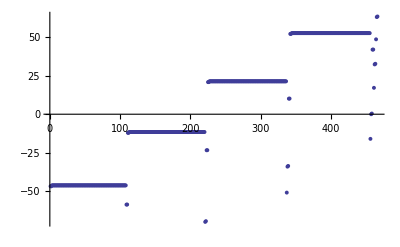

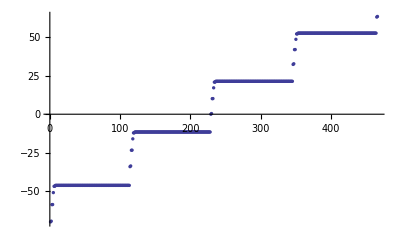

```mathematica
(*Find minimal Energydistance of found levels to initial levels*)

Clear[EDiff]
EDiff={};
For[i=1,i≤Length[NList],i++,EDiff=Join[EDiff,{(NList[[i,5]]-Subscript[E, 12])/10^9}]];
ListPlot[EDiff, PlotRange->{All,All},PlotStyle->PointSize[0.007]]
ListPlot[EDiff[[Ordering[EDiff]]], PlotRange->{All,All},PlotStyle->PointSize[0.006]]
```

```mathematica
NListTemp=NList[[Ordering[NList[[All,{5}]]]]] ;

(*Ordering NList beginning with highest Energy
LabelList is organized by energy also; it's an index for the NListTemp *)

LabelList={};
For[i=1,i≤Length[NList],i++,LabelList=Join[LabelList,{NListTemp[[i,1]]|NListTemp[[i,2]]|NListTemp[[i,3]]|NListTemp[[i,4]]}]]

(*Make List of Hilbert Space Basis level names for Plot of Energies*)

NList ;
LabelList

Clear[n,l,m,j,mj,np,lp,mp,jp,mjp,lj,ljp,Ξ,Ω,Ex,Ey,Ez,EField]
Clear[I0,E0,EFieldpi,EFieldsp,EFieldsm]

(*Calculation of r-Vector-Matrixelement <n,l,j,m|{x,y,z}|np,lp,jp,mp>(Vector) = RDip*ADip(Vector) for Angular and Radial Part (in atomic unit [Subscript[a, 0]]), ADip is a 3x1 Vector! *)
ADip[{n_,l_,j_,m_},{np_,lp_,jp_,mp_}]:=(√2)/2*(-1.)^(jp+l-1/2)*√(2.*jp+1)*SixJSymbol[{lp,1/2,jp},{j,1,l}]*(-1)^l*√((2*l+1)*(2*lp+1))*ThreeJSymbol[{l,0},{1,0},{lp,0}]*{ClebschGordan[{jp,mp},{1,-1},{j,m}]-ClebschGordan[{jp,mp},{1,1},{j,m}],I*ClebschGordan[{jp,mp},{1,-1},{j,m}]+I*ClebschGordan[{jp,mp},{1,1},{j,m}],√2*ClebschGordan[{jp,mp},{1,0},{j,m}]};
RDip[{n_,l_,lj_},{np_,lp_,ljp_}]:=RadIntE[ERadinte[lj,n],ERadinte[ljp,np],l,lp,1];

(*  Definition of Matrix Element Subscript[H, dipole]= RDip*ADip(Vector)(*.EField*) in unit [Subscript[a, 0]*Subscript[e, SI](*V/m*)]  *)
EMatrixelement[{n_,l_,j_,m_},{np_,lp_,jp_,mp_}]:=RDip[{n,l,Chooselj[l,j]},{np,lp,Chooselj[lp,jp]}]*ADip[{n,l,j,m},{np,lp,jp,mp}](*.EField*);

EMatrixelement[{60,1,3/2,3/2},{60,2,3/2,1/2}]


(*Fill up Matrix VMatrix with Sandwiched Efield Interaction <A|E*d|A'>*)
Clear[AI]
EMatrix=Array[E,{Length[NList],Length[NList]}];
EMatrix[[1,1]]
Timing[For[i=1,i≤Length[NList],i++,
		For[k=1,k≤Length[NList],k++,
If[((Abs[NList[[i,4]]-NList[[k,4]]]==1 ∨ Abs[NList[[i,4]]-NList[[k,4]]]==0))∧(Abs[NList[[i,2]]-NList[[k,2]]]==1),EMatrix[[i,k]]=EMatrixelement[{NList[[i,1]],NList[[i,2]],NList[[i,3]],NList[[i,4]]},{NList[[k,1]],NList[[k,2]],NList[[k,3]],NList[[k,4]]}],EMatrix[[i,k]]={0,0,0}] (*If m and l-parity*)
] 
] 
]
Clear[i,k,AI]

EMatrix[[1,1]]
```

{59|1|1/2|1/2,59|1|3/2|1/2,58|2|3/2|1/2,58|2|5/2|1/2,60|0|1/2|1/2,57|3|7/2|1/2,57|3|5/2|1/2,57|4|7/2|1/2,57|4|9/2|1/2,57|5|9/2|1/2,57|5|11/2|1/2,57|6|11/2|1/2,57|6|13/2|1/2,57|7|13/2|1/2,57|7|15/2|1/2,57|8|15/2|1/2,57|8|17/2|1/2,57|9|17/2|1/2,57|9|19/2|1/2,57|10|19/2|1/2,57|10|21/2|1/2,57|11|21/2|1/2,57|11|23/2|1/2,57|12|23/2|1/2,57|12|25/2|1/2,57|13|25/2|1/2,57|13|27/2|1/2,57|14|27/2|1/2,57|14|29/2|1/2,57|15|29/2|1/2,57|15|31/2|1/2,57|16|31/2|1/2,57|16|33/2|1/2,57|17|33/2|1/2,57|17|35/2|1/2,57|18|35/2|1/2,57|18|37/2|1/2,57|19|37/2|1/2,57|19|39/2|1/2,57|20|39/2|1/2,57|20|41/2|1/2,57|21|41/2|1/2,57|21|43/2|1/2,57|22|43/2|1/2,57|22|45/2|1/2,57|23|45/2|1/2,57|23|47/2|1/2,57|24|47/2|1/2,57|24|49/2|1/2,57|25|49/2|1/2,57|25|51/2|1/2,57|26|51/2|1/2,57|26|53/2|1/2,57|27|53/2|1/2,57|27|55/2|1/2,57|28|55/2|1/2,57|28|57/2|1/2,57|29|57/2|1/2,57|29|59/2|1/2,57|30|59/2|1/2,57|30|61/2|1/2,57|31|61/2|1/2,57|31|63/2|1/2,57|32|63/2|1/2,57|32|65/2|1/2,57|33|65/2|1/2,57|33|67/2|1/2,57|34|67/2|1/2,57|34|69/2|1/2,57|35|69/2|1/2,57|35|71/2|1/2,57|36|71/2|1/2,57|36|73/2|1/2,57|37|73/2|1/2,57|37|75/2|1/2,57|38|75/2|1/2,57|38|77/2|1/2,57|39|77/2|1/2,57|39|79/2|1/2,57|40|79/2|1/2,57|40|81/2|1/2,57|41|81/2|1/2,57|41|83/2|1/2,57|42|83/2|1/2,57|42|85/2|1/2,57|43|85/2|1/2,57|43|87/2|1/2,57|44|87/2|1/2,57|44|89/2|1/2,57|45|89/2|1/2,57|45|91/2|1/2,57|46|91/2|1/2,57|46|93/2|1/2,57|47|93/2|1/2,57|47|95/2|1/2,57|48|95/2|1/2,57|48|97/2|1/2,57|49|97/2|1/2,57|49|99/2|1/2,57|50|99/2|1/2,57|50|101/2|1/2,57|51|101/2|1/2,57|51|103/2|1/2,57|52|103/2|1/2,57|52|105/2|1/2,57|53|105/2|1/2,57|53|107/2|1/2,57|54|107/2|1/2,57|54|109/2|1/2,57|55|109/2|1/2,57|55|111/2|1/2,57|56|111/2|1/2,57|56|113/2|1/2,60|1|1/2|1/2,60|1|3/2|1/2,59|2|3/2|1/2,59|2|5/2|1/2,61|0|1/2|1/2,58|3|7/2|1/2,58|3|5/2|1/2,58|4|7/2|1/2,58|4|9/2|1/2,58|5|9/2|1/2,58|5|11/2|1/2,58|6|11/2|1/2,58|6|13/2|1/2,58|7|13/2|1/2,58|7|15/2|1/2,58|8|15/2|1/2,58|8|17/2|1/2,58|9|17/2|1/2,58|9|19/2|1/2,58|10|19/2|1/2,58|10|21/2|1/2,58|11|21/2|1/2,58|11|23/2|1/2,58|12|23/2|1/2,58|12|25/2|1/2,58|13|25/2|1/2,58|13|27/2|1/2,58|14|27/2|1/2,58|14|29/2|1/2,58|15|29/2|1/2,58|15|31/2|1/2,58|16|31/2|1/2,58|16|33/2|1/2,58|17|33/2|1/2,58|17|35/2|1/2,58|18|35/2|1/2,58|18|37/2|1/2,58|19|37/2|1/2,58|19|39/2|1/2,58|20|39/2|1/2,58|20|41/2|1/2,58|21|41/2|1/2,58|21|43/2|1/2,58|22|43/2|1/2,58|22|45/2|1/2,58|23|45/2|1/2,58|23|47/2|1/2,58|24|47/2|1/2,58|24|49/2|1/2,58|25|49/2|1/2,58|25|51/2|1/2,58|26|51/2|1/2,58|26|53/2|1/2,58|27|53/2|1/2,58|27|55/2|1/2,58|28|55/2|1/2,58|28|57/2|1/2,58|29|57/2|1/2,58|29|59/2|1/2,58|30|59/2|1/2,58|30|61/2|1/2,58|31|61/2|1/2,58|31|63/2|1/2,58|32|63/2|1/2,58|32|65/2|1/2,58|33|65/2|1/2,58|33|67/2|1/2,58|34|67/2|1/2,58|34|69/2|1/2,58|35|69/2|1/2,58|35|71/2|1/2,58|36|71/2|1/2,58|36|73/2|1/2,58|37|73/2|1/2,58|37|75/2|1/2,58|38|75/2|1/2,58|38|77/2|1/2,58|39|77/2|1/2,58|39|79/2|1/2,58|40|79/2|1/2,58|40|81/2|1/2,58|41|81/2|1/2,58|41|83/2|1/2,58|42|83/2|1/2,58|42|85/2|1/2,58|43|85/2|1/2,58|43|87/2|1/2,58|44|87/2|1/2,58|44|89/2|1/2,58|45|89/2|1/2,58|45|91/2|1/2,58|46|91/2|1/2,58|46|93/2|1/2,58|47|93/2|1/2,58|47|95/2|1/2,58|48|95/2|1/2,58|48|97/2|1/2,58|49|97/2|1/2,58|49|99/2|1/2,58|50|99/2|1/2,58|50|101/2|1/2,58|51|101/2|1/2,58|51|103/2|1/2,58|52|103/2|1/2,58|52|105/2|1/2,58|53|105/2|1/2,58|53|107/2|1/2,58|54|107/2|1/2,58|54|109/2|1/2,58|55|109/2|1/2,58|55|111/2|1/2,58|56|111/2|1/2,58|56|113/2|1/2,58|57|113/2|1/2,58|57|115/2|1/2,61|1|1/2|1/2,61|1|3/2|1/2,60|2|3/2|1/2,60|2|5/2|1/2,62|0|1/2|1/2,59|3|7/2|1/2,59|3|5/2|1/2,59|4|7/2|1/2,59|4|9/2|1/2,59|5|9/2|1/2,59|5|11/2|1/2,59|6|11/2|1/2,59|6|13/2|1/2,59|7|13/2|1/2,59|7|15/2|1/2,59|8|15/2|1/2,59|8|17/2|1/2,59|9|17/2|1/2,59|9|19/2|1/2,59|10|19/2|1/2,59|10|21/2|1/2,59|11|21/2|1/2,59|11|23/2|1/2,59|12|23/2|1/2,59|12|25/2|1/2,59|13|25/2|1/2,59|13|27/2|1/2,59|14|27/2|1/2,59|14|29/2|1/2,59|15|29/2|1/2,59|15|31/2|1/2,59|16|31/2|1/2,59|16|33/2|1/2,59|17|33/2|1/2,59|17|35/2|1/2,59|18|35/2|1/2,59|18|37/2|1/2,59|19|37/2|1/2,59|19|39/2|1/2,59|20|39/2|1/2,59|20|41/2|1/2,59|21|41/2|1/2,59|21|43/2|1/2,59|22|43/2|1/2,59|22|45/2|1/2,59|23|45/2|1/2,59|23|47/2|1/2,59|24|47/2|1/2,59|24|49/2|1/2,59|25|49/2|1/2,59|25|51/2|1/2,59|26|51/2|1/2,59|26|53/2|1/2,59|27|53/2|1/2,59|27|55/2|1/2,59|28|55/2|1/2,59|28|57/2|1/2,59|29|57/2|1/2,59|29|59/2|1/2,59|30|59/2|1/2,59|30|61/2|1/2,59|31|61/2|1/2,59|31|63/2|1/2,59|32|63/2|1/2,59|32|65/2|1/2,59|33|65/2|1/2,59|33|67/2|1/2,59|34|67/2|1/2,59|34|69/2|1/2,59|35|69/2|1/2,59|35|71/2|1/2,59|36|71/2|1/2,59|36|73/2|1/2,59|37|73/2|1/2,59|37|75/2|1/2,59|38|75/2|1/2,59|38|77/2|1/2,59|39|77/2|1/2,59|39|79/2|1/2,59|40|79/2|1/2,59|40|81/2|1/2,59|41|81/2|1/2,59|41|83/2|1/2,59|42|83/2|1/2,59|42|85/2|1/2,59|43|85/2|1/2,59|43|87/2|1/2,59|44|87/2|1/2,59|44|89/2|1/2,59|45|89/2|1/2,59|45|91/2|1/2,59|46|91/2|1/2,59|46|93/2|1/2,59|47|93/2|1/2,59|47|95/2|1/2,59|48|95/2|1/2,59|48|97/2|1/2,59|49|97/2|1/2,59|49|99/2|1/2,59|50|99/2|1/2,59|50|101/2|1/2,59|51|101/2|1/2,59|51|103/2|1/2,59|52|103/2|1/2,59|52|105/2|1/2,59|53|105/2|1/2,59|53|107/2|1/2,59|54|107/2|1/2,59|54|109/2|1/2,59|55|109/2|1/2,59|55|111/2|1/2,59|56|111/2|1/2,59|56|113/2|1/2,59|57|113/2|1/2,59|57|115/2|1/2,59|58|115/2|1/2,59|58|117/2|1/2,62|1|1/2|1/2,62|1|3/2|1/2,61|2|3/2|1/2,61|2|5/2|1/2,63|0|1/2|1/2,60|3|7/2|1/2,60|3|5/2|1/2,60|4|7/2|1/2,60|4|9/2|1/2,60|5|9/2|1/2,60|5|11/2|1/2,60|6|11/2|1/2,60|6|13/2|1/2,60|7|13/2|1/2,60|7|15/2|1/2,60|8|15/2|1/2,60|8|17/2|1/2,60|9|17/2|1/2,60|9|19/2|1/2,60|10|19/2|1/2,60|10|21/2|1/2,60|11|21/2|1/2,60|11|23/2|1/2,60|12|23/2|1/2,60|12|25/2|1/2,60|13|25/2|1/2,60|13|27/2|1/2,60|14|27/2|1/2,60|14|29/2|1/2,60|15|29/2|1/2,60|15|31/2|1/2,60|16|31/2|1/2,60|16|33/2|1/2,60|17|33/2|1/2,60|17|35/2|1/2,60|18|35/2|1/2,60|18|37/2|1/2,60|19|37/2|1/2,60|19|39/2|1/2,60|20|39/2|1/2,60|20|41/2|1/2,60|21|41/2|1/2,60|21|43/2|1/2,60|22|43/2|1/2,60|22|45/2|1/2,60|23|45/2|1/2,60|23|47/2|1/2,60|24|47/2|1/2,60|24|49/2|1/2,60|25|49/2|1/2,60|25|51/2|1/2,60|26|51/2|1/2,60|26|53/2|1/2,60|27|53/2|1/2,60|27|55/2|1/2,60|28|55/2|1/2,60|28|57/2|1/2,60|29|57/2|1/2,60|29|59/2|1/2,60|30|59/2|1/2,60|30|61/2|1/2,60|31|61/2|1/2,60|31|63/2|1/2,60|32|63/2|1/2,60|32|65/2|1/2,60|33|65/2|1/2,60|33|67/2|1/2,60|34|67/2|1/2,60|34|69/2|1/2,60|35|69/2|1/2,60|35|71/2|1/2,60|36|71/2|1/2,60|36|73/2|1/2,60|37|73/2|1/2,60|37|75/2|1/2,60|38|75/2|1/2,60|38|77/2|1/2,60|39|77/2|1/2,60|39|79/2|1/2,60|40|79/2|1/2,60|40|81/2|1/2,60|41|81/2|1/2,60|41|83/2|1/2,60|42|83/2|1/2,60|42|85/2|1/2,60|43|85/2|1/2,60|43|87/2|1/2,60|44|87/2|1/2,60|44|89/2|1/2,60|45|89/2|1/2,60|45|91/2|1/2,60|46|91/2|1/2,60|46|93/2|1/2,60|47|93/2|1/2,60|47|95/2|1/2,60|48|95/2|1/2,60|48|97/2|1/2,60|49|97/2|1/2,60|49|99/2|1/2,60|50|99/2|1/2,60|50|101/2|1/2,60|51|101/2|1/2,60|51|103/2|1/2,60|52|103/2|1/2,60|52|105/2|1/2,60|53|105/2|1/2,60|53|107/2|1/2,60|54|107/2|1/2,60|54|109/2|1/2,60|55|109/2|1/2,60|55|111/2|1/2,60|56|111/2|1/2,60|56|113/2|1/2,60|57|113/2|1/2,60|57|115/2|1/2,60|58|115/2|1/2,60|58|117/2|1/2,60|59|117/2|1/2,60|59|119/2|1/2,63|1|1/2|1/2,63|1|3/2|1/2}

ClebschGordan::phy: ThreeJSymbol[{3/2, 1/2}, {1, -1}, {3/2, -3/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, 1/2}, {1, 0}, {3/2, -3/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{4.27917,0.-4.27917 ⅈ,0.}

ⅇ[1,1]

ClebschGordan::phy: ThreeJSymbol[{7/2, 1/2}, {1, -1}, {5/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{7/2, 1/2}, {1, 1}, {5/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{7/2, 1/2}, {1, -1}, {5/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{4, 1/2, 9/2}, {5/2, 1, 3}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, 1/2}, {1, -1}, {5/2, -1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, 1/2}, {1, 1}, {5/2, -1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, 1/2}, {1, -1}, {5/2, -1/2}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{4, 1/2, 9/2}, {5/2, 1, 3}] is not triangular.

General::stop: Further output of SixJSymbol :: tri will be suppressed during this calculation.

{29.718,Null}

{0,0,0}

```mathematica
(*Absolute Energies of disturbed levels:*)

Clear[i,f,R]
EI={};
EI
NList;
For[i=1,i≤Length[NList],i++,EI=Join[EI,{NList[[i,5]]} ] ] ;
EIList = {} ;
EI
EIList=EI;
EI;
EI=DiagonalMatrix[EI];
MatrixPlot[EI]
```

{}

{-1.01315×10^12,-1.01315×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.02504×10^12,-1.02498×10^12,-9.78506×10^11,-9.78506×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-1.03624×10^12,-1.03576×10^12,-9.89788×10^11,-9.89732×10^11,-9.45608×10^11,-9.45609×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-1.01724×10^12,-1.00042×10^12,-9.99956×10^11,-9.56325×10^11,-9.56272×10^11,-9.14342×10^11,-9.14343×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.8239×10^11,-9.66417×10^11,-9.6598×10^11,-9.2453×10^11,-9.2448×10^11,-9.49298×10^11,-9.34122×10^11,-9.33706×10^11,-9.1785×10^11,-9.03419×10^11,-9.03024×10^11}

-Graphics-

```mathematica
EField={0,0,1} ;
MatrixPlot[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]
MatrixPlot[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]
Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]
```

-Graphics-

-Graphics-

{-1036.24,-1035.76,-1025.04,-1024.98,-1017.24,-1013.15,-1013.15,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.6,-1012.6,-1012.6,-1012.6,-1012.6,-1012.6,-1012.6,-1012.6,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.5,-1012.5,-1000.42,-999.956,-989.788,-989.732,-982.39,-978.508,-978.507,-978.012,-978.011,-978.009,-978.009,-978.007,-978.006,-978.004,-978.004,-978.002,-978.002,-977.999,-977.999,-977.997,-977.997,-977.995,-977.994,-977.992,-977.992,-977.99,-977.99,-977.988,-977.987,-977.985,-977.985,-977.983,-977.983,-977.981,-977.98,-977.978,-977.978,-977.976,-977.976,-977.974,-977.973,-977.971,-977.971,-977.969,-977.969,-977.967,-977.967,-977.964,-977.964,-977.962,-977.962,-977.96,-977.96,-977.957,-977.957,-977.955,-977.955,-977.953,-977.953,-977.95,-977.95,-977.948,-977.948,-977.946,-977.946,-977.943,-977.943,-977.941,-977.941,-977.939,-977.939,-977.936,-977.936,-977.934,-977.934,-977.932,-977.932,-977.93,-977.929,-977.927,-977.927,-977.925,-977.925,-977.923,-977.923,-977.92,-977.92,-977.918,-977.918,-977.916,-977.916,-977.913,-977.913,-977.911,-977.911,-977.909,-977.909,-977.906,-977.906,-977.904,-977.904,-977.902,-977.901,-977.899,-977.899,-977.897,-977.897,-977.894,-977.894,-977.892,-977.892,-977.89,-977.889,-977.887,-977.887,-966.417,-965.98,-956.325,-956.272,-949.298,-945.611,-945.61,-945.144,-945.144,-945.141,-945.141,-945.139,-945.139,-945.136,-945.136,-945.134,-945.134,-945.131,-945.131,-945.129,-945.129,-945.127,-945.127,-945.124,-945.124,-945.122,-945.122,-945.119,-945.119,-945.117,-945.117,-945.115,-945.115,-945.112,-945.112,-945.11,-945.11,-945.108,-945.108,-945.105,-945.105,-945.103,-945.103,-945.101,-945.1,-945.098,-945.098,-945.096,-945.096,-945.093,-945.093,-945.091,-945.091,-945.089,-945.089,-945.086,-945.086,-945.084,-945.084,-945.082,-945.082,-945.079,-945.079,-945.077,-945.077,-945.075,-945.075,-945.072,-945.072,-945.07,-945.07,-945.068,-945.068,-945.065,-945.065,-945.063,-945.063,-945.06,-945.06,-945.058,-945.058,-945.056,-945.056,-945.053,-945.053,-945.051,-945.051,-945.049,-945.049,-945.046,-945.046,-945.044,-945.044,-945.042,-945.042,-945.039,-945.039,-945.037,-945.037,-945.034,-945.034,-945.032,-945.032,-945.03,-945.03,-945.027,-945.027,-945.025,-945.025,-945.023,-945.022,-945.02,-945.02,-945.018,-945.017,-945.015,-945.015,-934.122,-933.706,-924.53,-924.48,-917.85,-914.345,-914.344,-913.906,-913.906,-913.903,-913.903,-913.901,-913.901,-913.898,-913.898,-913.896,-913.896,-913.893,-913.893,-913.891,-913.891,-913.888,-913.888,-913.886,-913.886,-913.884,-913.884,-913.881,-913.881,-913.879,-913.879,-913.876,-913.876,-913.874,-913.874,-913.872,-913.871,-913.869,-913.869,-913.867,-913.867,-913.864,-913.864,-913.862,-913.862,-913.86,-913.859,-913.857,-913.857,-913.855,-913.855,-913.852,-913.852,-913.85,-913.85,-913.848,-913.848,-913.845,-913.845,-913.843,-913.843,-913.84,-913.84,-913.838,-913.838,-913.836,-913.836,-913.833,-913.833,-913.831,-913.831,-913.828,-913.828,-913.826,-913.826,-913.824,-913.824,-913.821,-913.821,-913.819,-913.819,-913.816,-913.816,-913.814,-913.814,-913.812,-913.812,-913.809,-913.809,-913.807,-913.807,-913.804,-913.804,-913.802,-913.802,-913.8,-913.8,-913.797,-913.797,-913.795,-913.795,-913.792,-913.792,-913.79,-913.79,-913.788,-913.787,-913.785,-913.785,-913.783,-913.783,-913.78,-913.78,-913.778,-913.778,-913.775,-913.775,-913.773,-913.772,-903.419,-903.024}

{{300,-77.1313,59|1|1/2|1/2},{300,-74.1438,59|1|3/2|1/2},{300,-64.8703,58|2|3/2|1/2},{300,-64.6972,58|2|5/2|1/2},{300,-64.1935,60|0|1/2|1/2},{300,-64.0425,57|3|7/2|1/2},{300,-63.5293,57|3|5/2|1/2},{300,-63.3945,57|4|7/2|1/2},{300,-62.87,57|4|9/2|1/2},{300,-62.7507,57|5|9/2|1/2},{300,-62.2129,57|5|11/2|1/2},{300,-62.1091,57|6|11/2|1/2},{300,-61.5562,57|6|13/2|1/2},{300,-61.4675,57|7|13/2|1/2},{300,-60.8992,57|7|15/2|1/2},{300,-60.8244,57|8|15/2|1/2},{300,-60.2416,57|8|17/2|1/2},{300,-60.1789,57|9|17/2|1/2},{300,-59.5832,57|9|19/2|1/2},{300,-59.5306,57|10|19/2|1/2},{300,-58.924,57|10|21/2|1/2},{300,-58.8798,57|11|21/2|1/2},{300,-58.264,57|11|23/2|1/2},{300,-58.2266,57|12|23/2|1/2},{300,-57.6034,57|12|25/2|1/2},{300,-57.5714,57|13|25/2|1/2},{300,-56.9423,57|13|27/2|1/2},{300,-56.9145,57|14|27/2|1/2},{300,-56.2809,57|14|29/2|1/2},{300,-56.2563,57|15|29/2|1/2},{300,-55.6193,57|15|31/2|1/2},{300,-55.597,57|16|31/2|1/2},{300,-54.9579,57|16|33/2|1/2},{300,-54.9367,57|17|33/2|1/2},{300,-54.2975,57|17|35/2|1/2},{300,-54.2757,57|18|35/2|1/2},{300,-53.6404,57|18|37/2|1/2},{300,-53.614,57|19|37/2|1/2},{300,-53.,57|19|39/2|1/2},{300,-52.9517,57|20|39/2|1/2},{300,-52.5377,57|20|41/2|1/2},{300,-52.2888,57|21|41/2|1/2},{300,-52.2135,57|21|43/2|1/2},{300,-51.6253,57|22|43/2|1/2},{300,-51.6006,57|22|45/2|1/2},{300,-50.9613,57|23|45/2|1/2},{300,-50.9458,57|23|47/2|1/2},{300,-50.2967,57|24|47/2|1/2},{300,-50.2843,57|24|49/2|1/2},{300,-49.6317,57|25|49/2|1/2},{300,-49.6204,57|25|51/2|1/2},{300,-48.9662,57|26|51/2|1/2},{300,-48.9551,57|26|53/2|1/2},{300,-48.3002,57|27|53/2|1/2},{300,-48.289,57|27|55/2|1/2},{300,-47.6338,57|28|55/2|1/2},{300,-47.6221,57|28|57/2|1/2},{300,-46.9669,57|29|57/2|1/2},{300,-46.9546,57|29|59/2|1/2},{300,-46.2996,57|30|59/2|1/2},{300,-46.2865,57|30|61/2|1/2},{300,-45.6319,57|31|61/2|1/2},{300,-45.618,57|31|63/2|1/2},{300,-44.964,57|32|63/2|1/2},{300,-44.9491,57|32|65/2|1/2},{300,-44.2958,57|33|65/2|1/2},{300,-44.2798,57|33|67/2|1/2},{300,-43.6272,57|34|67/2|1/2},{300,-43.6101,57|34|69/2|1/2},{300,-42.9584,57|35|69/2|1/2},{300,-42.94,57|35|71/2|1/2},{300,-42.2893,57|36|71/2|1/2},{300,-42.2696,57|36|73/2|1/2},{300,-41.6201,57|37|73/2|1/2},{300,-41.5988,57|37|75/2|1/2},{300,-40.9509,57|38|75/2|1/2},{300,-40.9277,57|38|77/2|1/2},{300,-40.2822,57|39|77/2|1/2},{300,-40.2566,57|39|79/2|1/2},{300,-39.6154,57|40|79/2|1/2},{300,-39.5861,57|40|81/2|1/2},{300,-38.9557,57|41|81/2|1/2},{300,-38.9182,57|41|83/2|1/2},{300,-38.3478,57|42|83/2|1/2},{300,-38.2642,57|42|85/2|1/2},{300,-38.0238,57|43|85/2|1/2},{300,-37.7808,57|43|87/2|1/2},{300,-37.532,57|44|87/2|1/2},{300,-37.4726,57|44|89/2|1/2},{300,-36.8818,57|45|89/2|1/2},{300,-36.8505,57|45|91/2|1/2},{300,-36.2141,57|46|91/2|1/2},{300,-36.1833,57|46|93/2|1/2},{300,-35.5416,57|47|93/2|1/2},{300,-35.5091,57|47|95/2|1/2},{300,-34.8668,57|48|95/2|1/2},{300,-34.8319,57|48|97/2|1/2},{300,-34.1903,57|49|97/2|1/2},{300,-34.1527,57|49|99/2|1/2},{300,-33.5123,57|50|99/2|1/2},{300,-33.4716,57|50|101/2|1/2},{300,-32.8329,57|51|101/2|1/2},{300,-32.7887,57|51|103/2|1/2},{300,-32.1519,57|52|103/2|1/2},{300,-32.1036,57|52|105/2|1/2},{300,-31.4692,57|53|105/2|1/2},{300,-31.4161,57|53|107/2|1/2},{300,-30.7846,57|54|107/2|1/2},{300,-30.7263,57|54|109/2|1/2},{300,-30.4385,57|55|109/2|1/2},{300,-30.3192,57|55|111/2|1/2},{300,-30.0954,57|56|111/2|1/2},{300,-30.0283,57|56|113/2|1/2},{300,-29.7178,60|1|1/2|1/2},{300,-29.6287,60|1|3/2|1/2},{300,-29.4014,59|2|3/2|1/2},{300,-29.321,59|2|5/2|1/2},{300,-29.0167,61|0|1/2|1/2},{300,-28.9449,58|3|7/2|1/2},{300,-28.6997,58|3|5/2|1/2},{300,-28.5935,58|4|7/2|1/2},{300,-28.3246,58|4|9/2|1/2},{300,-28.2658,58|5|9/2|1/2},{300,-27.6469,58|5|11/2|1/2},{300,-27.595,58|6|11/2|1/2},{300,-26.9722,58|6|13/2|1/2},{300,-26.9278,58|7|13/2|1/2},{300,-26.3017,58|7|15/2|1/2},{300,-26.264,58|8|15/2|1/2},{300,-25.6348,58|8|17/2|1/2},{300,-25.603,58|9|17/2|1/2},{300,-24.9707,58|9|19/2|1/2},{300,-24.9439,58|10|19/2|1/2},{300,-24.3085,58|10|21/2|1/2},{300,-24.2858,58|11|21/2|1/2},{300,-23.6473,58|11|23/2|1/2},{300,-23.6277,58|12|23/2|1/2},{300,-22.9861,58|12|25/2|1/2},{300,-22.9686,58|13|25/2|1/2},{300,-22.3244,58|13|27/2|1/2},{300,-22.308,58|14|27/2|1/2},{300,-21.6617,58|14|29/2|1/2},{300,-21.6455,58|15|29/2|1/2},{300,-20.998,58|15|31/2|1/2},{300,-20.9809,58|16|31/2|1/2},{300,-20.3339,58|16|33/2|1/2},{300,-20.3142,58|17|33/2|1/2},{300,-19.6703,58|17|35/2|1/2},{300,-19.6455,58|18|35/2|1/2},{300,-19.0105,58|18|37/2|1/2},{300,-18.9751,58|19|37/2|1/2},{300,-18.3652,58|19|39/2|1/2},{300,-18.3031,58|20|39/2|1/2},{300,-17.7912,58|20|41/2|1/2},{300,-17.6297,58|21|41/2|1/2},{300,-17.3864,58|21|43/2|1/2},{300,-16.9552,58|22|43/2|1/2},{300,-16.8674,58|22|45/2|1/2},{300,-16.2797,58|23|45/2|1/2},{300,-16.2309,58|23|47/2|1/2},{300,-15.6034,58|24|47/2|1/2},{300,-15.5685,58|24|49/2|1/2},{300,-14.9262,58|25|49/2|1/2},{300,-14.8981,58|25|51/2|1/2},{300,-14.2484,58|26|51/2|1/2},{300,-14.2239,58|26|53/2|1/2},{300,-13.57,58|27|53/2|1/2},{300,-13.5476,58|27|55/2|1/2},{300,-12.891,58|28|55/2|1/2},{300,-12.8698,58|28|57/2|1/2},{300,-12.2116,58|29|57/2|1/2},{300,-12.1909,58|29|59/2|1/2},{300,-11.5317,58|30|59/2|1/2},{300,-11.5112,58|30|61/2|1/2},{300,-10.8515,58|31|61/2|1/2},{300,-10.8309,58|31|63/2|1/2},{300,-10.1711,58|32|63/2|1/2},{300,-10.15,58|32|65/2|1/2},{300,-9.49059,58|33|65/2|1/2},{300,-9.46887,58|33|67/2|1/2},{300,-8.81002,58|34|67/2|1/2},{300,-8.7874,58|34|69/2|1/2},{300,-8.12948,58|35|69/2|1/2},{300,-8.10566,58|35|71/2|1/2},{300,-7.44913,58|36|71/2|1/2},{300,-7.42371,58|36|73/2|1/2},{300,-6.76932,58|37|73/2|1/2},{300,-6.74165,58|37|75/2|1/2},{300,-6.0911,58|38|75/2|1/2},{300,-6.0597,58|38|77/2|1/2},{300,-5.41848,58|39|77/2|1/2},{300,-5.37851,58|39|79/2|1/2},{300,-4.78669,58|40|79/2|1/2},{300,-4.701,58|40|81/2|1/2},{300,-4.46502,58|41|81/2|1/2},{300,-4.06822,58|41|83/2|1/2},{300,-3.98836,58|42|83/2|1/2},{300,-3.84228,58|42|85/2|1/2},{300,-3.32721,58|43|85/2|1/2},{300,-3.29824,58|43|87/2|1/2},{300,-2.64971,58|44|87/2|1/2},{300,-2.62283,58|44|89/2|1/2},{300,-1.96831,58|45|89/2|1/2},{300,-1.93996,58|45|91/2|1/2},{300,-1.28516,58|46|91/2|1/2},{300,-1.25489,58|46|93/2|1/2},{300,-0.60089,58|47|93/2|1/2},{300,-0.568556,58|47|95/2|1/2},{300,0.084272,58|48|95/2|1/2},{300,0.118769,58|48|97/2|1/2},{300,0.770195,58|49|97/2|1/2},{300,0.806916,58|49|99/2|1/2},{300,1.45659,58|50|99/2|1/2},{300,1.49506,58|50|101/2|1/2},{300,1.83154,58|51|101/2|1/2},{300,1.94629,58|51|103/2|1/2},{300,2.14555,58|52|103/2|1/2},{300,2.18686,58|52|105/2|1/2},{300,2.56856,58|53|105/2|1/2},{300,2.65362,58|53|107/2|1/2},{300,2.83647,58|54|107/2|1/2},{300,2.88086,58|54|109/2|1/2},{300,3.28387,58|55|109/2|1/2},{300,3.3526,58|55|111/2|1/2},{300,3.52939,58|56|111/2|1/2},{300,3.57742,58|56|113/2|1/2},{300,3.98879,58|57|113/2|1/2},{300,4.04624,58|57|115/2|1/2},{300,4.22438,61|1|1/2|1/2},{300,4.27705,61|1|3/2|1/2},{300,4.68743,60|2|3/2|1/2},{300,4.73621,60|2|5/2|1/2},{300,4.92165,62|0|1/2|1/2},{300,4.98056,59|3|7/2|1/2},{300,5.3819,59|3|5/2|1/2},{300,5.42356,59|4|7/2|1/2},{300,5.62169,59|4|9/2|1/2},{300,5.68953,59|5|9/2|1/2},{300,6.07348,59|5|11/2|1/2},{300,6.10896,59|6|11/2|1/2},{300,6.32563,59|6|13/2|1/2},{300,6.40747,59|7|13/2|1/2},{300,6.76305,59|7|15/2|1/2},{300,6.79268,59|8|15/2|1/2},{300,7.03616,59|8|17/2|1/2},{300,7.14497,59|9|17/2|1/2},{300,7.45124,59|9|19/2|1/2},{300,7.47417,59|10|19/2|1/2},{300,8.12005,59|10|21/2|1/2},{300,8.14418,59|11|21/2|1/2},{300,8.79188,59|11|23/2|1/2},{300,8.81416,59|12|23/2|1/2},{300,9.4627,59|12|25/2|1/2},{300,9.48333,59|13|25/2|1/2},{300,10.1326,59|13|27/2|1/2},{300,10.1522,59|14|27/2|1/2},{300,10.8021,59|14|29/2|1/2},{300,10.8215,59|15|29/2|1/2},{300,11.4715,59|15|31/2|1/2},{300,11.4919,59|16|31/2|1/2},{300,12.141,59|16|33/2|1/2},{300,12.1638,59|17|33/2|1/2},{300,12.8099,59|17|35/2|1/2},{300,12.8376,59|18|35/2|1/2},{300,13.4761,59|18|37/2|1/2},{300,13.5134,59|19|37/2|1/2},{300,14.1324,59|19|39/2|1/2},{300,14.1912,59|20|39/2|1/2},{300,14.7485,59|20|41/2|1/2},{300,14.8709,59|21|41/2|1/2},{300,15.2264,59|21|43/2|1/2},{300,15.5524,59|22|43/2|1/2},{300,15.6924,59|22|45/2|1/2},{300,16.2354,59|23|45/2|1/2},{300,16.3046,59|23|47/2|1/2},{300,16.9198,59|24|47/2|1/2},{300,16.9657,59|24|49/2|1/2},{300,17.6055,59|25|49/2|1/2},{300,17.6409,59|25|51/2|1/2},{300,18.2923,59|26|51/2|1/2},{300,18.3221,59|26|53/2|1/2},{300,18.9802,59|27|53/2|1/2},{300,19.0067,59|27|55/2|1/2},{300,19.669,59|28|55/2|1/2},{300,19.6935,59|28|57/2|1/2},{300,20.3587,59|29|57/2|1/2},{300,20.382,59|29|59/2|1/2},{300,21.0491,59|30|59/2|1/2},{300,21.0719,59|30|61/2|1/2},{300,21.7401,59|31|61/2|1/2},{300,21.7628,59|31|63/2|1/2},{300,22.4315,59|32|63/2|1/2},{300,22.4545,59|32|65/2|1/2},{300,23.1233,59|33|65/2|1/2},{300,23.1468,59|33|67/2|1/2},{300,23.8152,59|34|67/2|1/2},{300,23.8397,59|34|69/2|1/2},{300,24.5071,59|35|69/2|1/2},{300,24.5331,59|35|71/2|1/2},{300,25.1986,59|36|71/2|1/2},{300,25.2269,59|36|73/2|1/2},{300,25.8884,59|37|73/2|1/2},{300,25.9209,59|37|75/2|1/2},{300,26.572,59|38|75/2|1/2},{300,26.6148,59|38|77/2|1/2},{300,27.2009,59|39|77/2|1/2},{300,27.3077,59|39|79/2|1/2},{300,27.4906,59|40|79/2|1/2},{300,27.9943,59|40|81/2|1/2},{300,28.0205,59|41|81/2|1/2},{300,28.5029,59|41|83/2|1/2},{300,28.6979,59|42|83/2|1/2},{300,28.7498,59|42|85/2|1/2},{300,29.388,59|43|85/2|1/2},{300,29.4154,59|43|87/2|1/2},{300,30.0815,59|44|87/2|1/2},{300,30.1082,59|44|89/2|1/2},{300,30.7764,59|45|89/2|1/2},{300,30.8042,59|45|91/2|1/2},{300,31.4721,59|46|91/2|1/2},{300,31.5013,59|46|93/2|1/2},{300,32.1684,59|47|93/2|1/2},{300,32.1989,59|47|95/2|1/2},{300,32.8647,59|48|95/2|1/2},{300,32.8958,59|48|97/2|1/2},{300,33.1982,59|49|97/2|1/2},{300,33.3069,59|49|99/2|1/2},{300,33.5629,59|50|99/2|1/2},{300,33.5959,59|50|101/2|1/2},{300,33.9551,59|51|101/2|1/2},{300,34.0365,59|51|103/2|1/2},{300,34.2625,59|52|103/2|1/2},{300,34.2974,59|52|105/2|1/2},{300,34.6885,59|53|105/2|1/2},{300,34.7563,59|53|107/2|1/2},{300,34.9636,59|54|107/2|1/2},{300,35.0007,59|54|109/2|1/2},{300,35.4107,59|55|109/2|1/2},{300,35.47,59|55|111/2|1/2},{300,35.6661,59|56|111/2|1/2},{300,35.7058,59|56|113/2|1/2},{300,36.126,59|57|113/2|1/2},{300,36.1793,59|57|115/2|1/2},{300,36.3703,59|58|115/2|1/2},{300,36.4129,59|58|117/2|1/2},{300,36.8365,62|1|1/2|1/2},{300,36.8854,62|1|3/2|1/2},{300,37.076,61|2|3/2|1/2},{300,37.1223,61|2|5/2|1/2},{300,37.5434,63|0|1/2|1/2},{300,37.5888,60|3|7/2|1/2},{300,37.7834,60|3|5/2|1/2},{300,37.8345,60|4|7/2|1/2},{300,38.2474,60|4|9/2|1/2},{300,38.2903,60|5|9/2|1/2},{300,38.4928,60|5|11/2|1/2},{300,38.5502,60|6|11/2|1/2},{300,38.9491,60|6|13/2|1/2},{300,38.9902,60|7|13/2|1/2},{300,39.2045,60|7|15/2|1/2},{300,39.2709,60|8|15/2|1/2},{300,39.6489,60|8|17/2|1/2},{300,39.6885,60|9|17/2|1/2},{300,39.9199,60|9|19/2|1/2},{300,40.0001,60|10|19/2|1/2},{300,40.3471,60|10|21/2|1/2},{300,40.3853,60|11|21/2|1/2},{300,40.6415,60|11|23/2|1/2},{300,40.7483,60|12|23/2|1/2},{300,41.0437,60|12|25/2|1/2},{300,41.079,60|13|25/2|1/2},{300,41.7049,60|13|27/2|1/2},{300,41.7545,60|14|27/2|1/2},{300,42.3749,60|14|29/2|1/2},{300,42.4304,60|15|29/2|1/2},{300,43.0457,60|15|31/2|1/2},{300,43.1052,60|16|31/2|1/2},{300,43.7177,60|16|33/2|1/2},{300,43.7797,60|17|33/2|1/2},{300,44.3916,60|17|35/2|1/2},{300,44.4553,60|18|35/2|1/2},{300,45.0679,60|18|37/2|1/2},{300,45.1329,60|19|37/2|1/2},{300,45.746,60|19|39/2|1/2},{300,45.8132,60|20|39/2|1/2},{300,46.4247,60|20|41/2|1/2},{300,46.4963,60|21|41/2|1/2},{300,47.1014,60|21|43/2|1/2},{300,47.1821,60|22|43/2|1/2},{300,47.77,60|22|45/2|1/2},{300,47.8704,60|23|45/2|1/2},{300,48.4139,60|23|47/2|1/2},{300,48.5608,60|24|47/2|1/2},{300,48.9894,60|24|49/2|1/2},{300,49.253,60|25|49/2|1/2},{300,49.4957,60|25|51/2|1/2},{300,49.9467,60|26|51/2|1/2},{300,50.0679,60|26|53/2|1/2},{300,50.6417,60|27|53/2|1/2},{300,50.7136,60|27|55/2|1/2},{300,51.3376,60|28|55/2|1/2},{300,51.3881,60|28|57/2|1/2},{300,52.0345,60|29|57/2|1/2},{300,52.0742,60|29|59/2|1/2},{300,52.732,60|30|59/2|1/2},{300,52.766,60|30|61/2|1/2},{300,53.4301,60|31|61/2|1/2},{300,53.4608,60|31|63/2|1/2},{300,54.1286,60|32|63/2|1/2},{300,54.1576,60|32|65/2|1/2},{300,54.8273,60|33|65/2|1/2},{300,54.8557,60|33|67/2|1/2},{300,55.5262,60|34|67/2|1/2},{300,55.5547,60|34|69/2|1/2},{300,56.2251,60|35|69/2|1/2},{300,56.2542,60|35|71/2|1/2},{300,56.9241,60|36|71/2|1/2},{300,56.9543,60|36|73/2|1/2},{300,57.6229,60|37|73/2|1/2},{300,57.6547,60|37|75/2|1/2},{300,58.3217,60|38|75/2|1/2},{300,58.3555,60|38|77/2|1/2},{300,59.0202,60|39|77/2|1/2},{300,59.0566,60|39|79/2|1/2},{300,59.7183,60|40|79/2|1/2},{300,59.7581,60|40|81/2|1/2},{300,60.4156,60|41|81/2|1/2},{300,60.4598,60|41|83/2|1/2},{300,61.1116,60|42|83/2|1/2},{300,61.1618,60|42|85/2|1/2},{300,61.805,60|43|85/2|1/2},{300,61.8641,60|43|87/2|1/2},{300,62.4933,60|44|87/2|1/2},{300,62.5666,60|44|89/2|1/2},{300,63.1692,60|45|89/2|1/2},{300,63.2693,60|45|91/2|1/2},{300,63.8096,60|46|91/2|1/2},{300,63.9723,60|46|93/2|1/2},{300,64.3575,60|47|93/2|1/2},{300,64.6753,60|47|95/2|1/2},{300,64.8626,60|48|95/2|1/2},{300,65.3783,60|48|97/2|1/2},{300,65.4669,60|49|97/2|1/2},{300,66.0808,60|49|99/2|1/2},{300,66.1323,60|50|99/2|1/2},{300,66.7823,60|50|101/2|1/2},{300,66.8187,60|51|101/2|1/2},{300,67.4812,60|51|103/2|1/2},{300,67.5139,60|52|103/2|1/2},{300,68.1735,60|52|105/2|1/2},{300,68.2137,60|53|105/2|1/2},{300,68.8468,60|53|107/2|1/2},{300,68.9166,60|54|107/2|1/2},{300,69.4565,60|54|109/2|1/2},{300,69.6219,60|55|109/2|1/2},{300,69.9565,60|55|111/2|1/2},{300,70.3293,60|56|111/2|1/2},{300,70.5128,60|56|113/2|1/2},{300,71.039,60|57|113/2|1/2},{300,71.1723,60|57|115/2|1/2},{300,71.7512,60|58|115/2|1/2},{300,71.8716,60|58|117/2|1/2},{300,72.4668,60|59|117/2|1/2},{300,72.5908,60|59|119/2|1/2},{300,73.1872,63|1|1/2|1/2},{300,73.3324,63|1|3/2|1/2}}

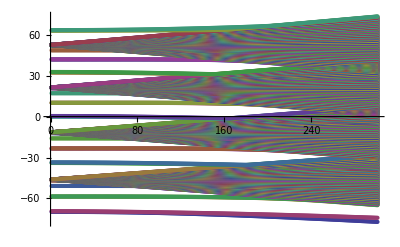

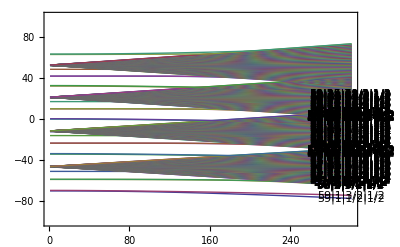

```mathematica
(*MultiListPlot: Generate Plot of Energies as a Function of EField*)
Clear[i,k,L,MPList,R]
MPList=Array[L,{Length[NList],2}];
Temp={};
EMIN=0;
EMAX=301;
ELabel=300;
(*Electric Field in [V/m], Efield perpend. to BEC, so E={Ex,0,Ez=0}, parasitic Fields typ. 1V/cm, Const. Field typ. 5V/cm*)
(*Subscript[EStark, 12]=2*EMatrixelement[{44,0,1/2,1/2},{44,0,1/2,1/2}]*Subscript[e, SI]*Subscript[a, 0]*)(*Calculate shift of 44s44s-44s44s for R->∞ for Offset substraction in Plot, [J]*)

E0=EMIN;
EStep=1;

For[i=1,i≤Length[NList],i++,MPList[[i]]={}];
Clear[i];
While[E0<EMAX,E0=E0+EStep;EField={0,0,E0};Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]-Subscript[E, 12]/10^9;For[i=1,i≤Length[NList],i++,MPList[[i]]=Join[MPList[[i]],{{E0,Temp[[i]]}}]  ]] ;
E0=EMIN;

Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.{0,0,ELabel}/h/10^9]-Subscript[E, 12]/10^9;(*Generate Labels for Levels*)
TempList=Array[T,Length[NList]];
For[i=1,i≤Length[NList],i++,TempList[[i]]={ELabel,Temp[[i]],LabelList[[i]]} ];
TempList

ListPlot[MPList]

Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-100,100}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

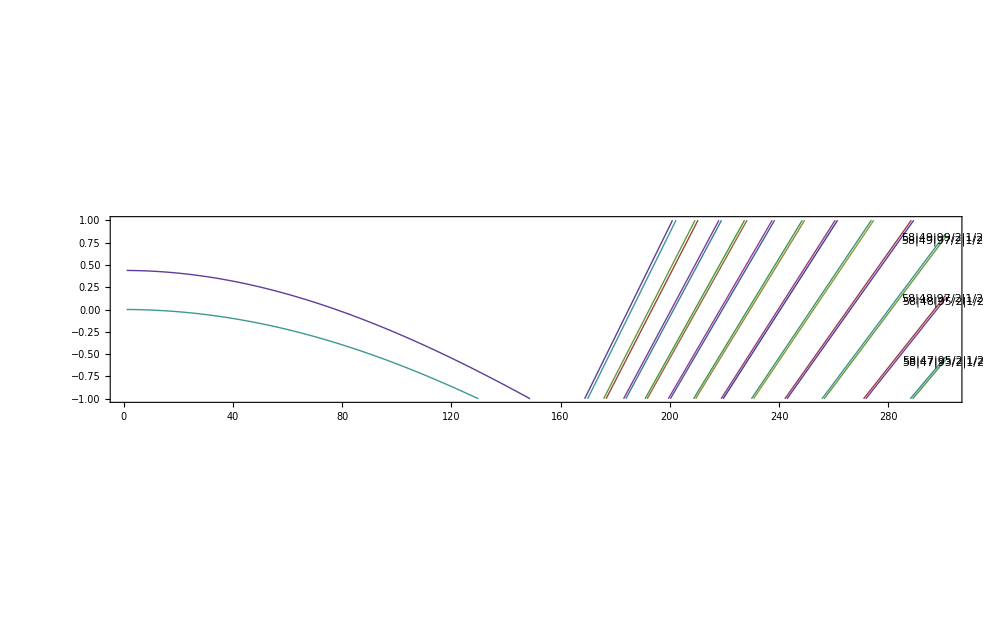

```mathematica
Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-1,1}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

```mathematica
LabelList[[218]]

MPList[[218]]

(*MPListExport: Generate list to be read by Origin *)

Efieldlist = {};

E0=EMIN;


While[E0<EMAX,E0=E0+EStep;Efieldlist=Join[Efieldlist,{E0}]] ;
E0=EMIN;

Efieldlist


Clear[i,k,L,MPListExport,R]
NE0=(EMAX-EMIN)/EStep;
MPListExport=Array[0,{Length[NList],NE0}];
(*Electric Field in [V/m], Efield perpend. to BEC, so E={Ex,0,Ez=0}, parasitic Fields typ. 1V/cm, Const. Field typ. 5V/cm*)
(*Subscript[EStark, 12]=2*EMatrixelement[{44,0,1/2,1/2},{44,0,1/2,1/2}]*Subscript[e, SI]*Subscript[a, 0]*)(*Calculate shift of 44s44s-44s44s for R->∞ for Offset substraction in Plot, [J]*)



Clear[i];
j=0;
While[j<NE0,
j++;
For[i=1,i≤Length[NList],i++,
MPListExport[[i,j]]=MPList[[i,j,2]] 
 ]
] ;

MPListExport



Export["Stark_Shifts_around_60p3_2_mj3_2.dat",MPListExport]
Export["Electric_fields_for_Stark_Shifts_around_60p3_2_mj3_2.dat",Efieldlist]

(*Export["60p_j3_2_mj3_2_stark_Shift.dat",MPList[[218]]]*)
```

55|6|13/2|3/2

{{1,-87.639},{2,-87.6895},{3,-87.7398},{4,-87.7902},{5,-87.8406},{6,-87.8909},{7,-87.9412},{8,-87.9914},{9,-88.0415},{10,-88.0916},{11,-88.1416},{12,-88.1915},{13,-88.2413},{14,-88.2908},{15,-88.3401},{16,-88.3892},{17,-88.4378},{18,-88.486},{19,-88.5338},{20,-88.5813},{21,-88.6284},{22,-88.6755},{23,-88.7225},{24,-88.7696},{25,-88.8168},{26,-88.8642},{27,-88.9117},{28,-88.9594},{29,-89.0071},{30,-89.055},{31,-89.1029},{32,-89.1509},{33,-89.1989},{34,-89.247},{35,-89.2951},{36,-89.3433},{37,-89.3915},{38,-89.4397},{39,-89.488},{40,-89.5363},{41,-89.5846},{42,-89.6329},{43,-89.6812},{44,-89.7295},{45,-89.7779},{46,-89.8262},{47,-89.8746},{48,-89.923},{49,-89.9714},{50,-90.0198},{51,-90.0682},{52,-90.1166},{53,-90.165},{54,-90.2134},{55,-90.2619},{56,-90.3103},{57,-90.3587},{58,-90.4072},{59,-90.4556},{60,-90.504},{61,-90.5525},{62,-90.601},{63,-90.6494},{64,-90.6979},{65,-90.7463},{66,-90.7948},{67,-90.8433},{68,-90.8917},{69,-90.9402},{70,-90.9887},{71,-91.0371},{72,-91.0856},{73,-91.1341},{74,-91.1826},{75,-91.2311},{76,-91.2796},{77,-91.328},{78,-91.3765},{79,-91.425},{80,-91.4735},{81,-91.522},{82,-91.5705},{83,-91.619},{84,-91.6675},{85,-91.716},{86,-91.7645},{87,-91.813},{88,-91.8615},{89,-91.91},{90,-91.9585},{91,-92.007},{92,-92.0555},{93,-92.104},{94,-92.1525},{95,-92.201},{96,-92.2495},{97,-92.298},{98,-92.3466},{99,-92.3951},{100,-92.4436},{101,-92.4921},{102,-92.5406},{103,-92.5891},{104,-92.6376},{105,-92.6862},{106,-92.7347},{107,-92.7832},{108,-92.8317},{109,-92.8802},{110,-92.9288},{111,-92.9773},{112,-93.0258},{113,-93.0743},{114,-93.1228},{115,-93.1714},{116,-93.2199},{117,-93.2684},{118,-93.3169},{119,-93.3655},{120,-93.414},{121,-93.4625},{122,-93.511},{123,-93.5596},{124,-93.6081},{125,-93.6566},{126,-93.7051},{127,-93.7537},{128,-93.8022},{129,-93.8507},{130,-93.8992},{131,-93.9478},{132,-93.9963},{133,-94.0448},{134,-94.0934},{135,-94.1419},{136,-94.1904},{137,-94.2389},{138,-94.2875},{139,-94.336},{140,-94.3845},{141,-94.433},{142,-94.4816},{143,-94.5301},{144,-94.5786},{145,-94.6272},{146,-94.6757},{147,-94.7242},{148,-94.7727},{149,-94.8213},{150,-94.8698},{151,-94.9183},{152,-94.9668},{153,-95.0154},{154,-95.0639},{155,-95.1124},{156,-95.1609},{157,-95.2095},{158,-95.258},{159,-95.3065},{160,-95.355},{161,-95.4035},{162,-95.4521},{163,-95.5006},{164,-95.5491},{165,-95.5976},{166,-95.6461},{167,-95.6946},{168,-95.7432},{169,-95.7917},{170,-95.8402},{171,-95.8887},{172,-95.9372},{173,-95.9857},{174,-96.0342},{175,-96.0827},{176,-96.1313},{177,-96.1798},{178,-96.2283},{179,-96.2768},{180,-96.3253},{181,-96.3738},{182,-96.4223},{183,-96.4708},{184,-96.5193},{185,-96.5678},{186,-96.6162},{187,-96.6647},{188,-96.7132},{189,-96.7617},{190,-96.8102},{191,-96.8587},{192,-96.9072},{193,-96.9556},{194,-97.0041},{195,-97.0526},{196,-97.1011},{197,-97.1495},{198,-97.198},{199,-97.2465},{200,-97.2949},{201,-97.3434},{202,-97.3919},{203,-97.4403},{204,-97.4888},{205,-97.5372},{206,-97.5857},{207,-97.6341},{208,-97.6826},{209,-97.731},{210,-97.7794},{211,-97.8279},{212,-97.8763},{213,-97.9247},{214,-97.9731},{215,-98.0216},{216,-98.07},{217,-98.1184},{218,-98.1668},{219,-98.2152},{220,-98.2636},{221,-98.312},{222,-98.3604},{223,-98.4088},{224,-98.4571},{225,-98.5055},{226,-98.5539},{227,-98.6023},{228,-98.6506},{229,-98.699},{230,-98.7473},{231,-98.7957},{232,-98.844},{233,-98.8923},{234,-98.9407},{235,-98.989},{236,-99.0373},{237,-99.0856},{238,-99.1339},{239,-99.1822},{240,-99.2305},{241,-99.2787},{242,-99.327},{243,-99.3753},{244,-99.4235},{245,-99.4718},{246,-99.52},{247,-99.5683},{248,-99.6165},{249,-99.6647},{250,-99.7129},{251,-99.7611},{252,-99.8093},{253,-99.8574},{254,-99.9056},{255,-99.9538},{256,-100.002},{257,-100.05},{258,-100.098},{259,-100.146},{260,-100.194},{261,-100.242},{262,-100.291},{263,-100.339},{264,-100.387},{265,-100.435},{266,-100.483},{267,-100.531},{268,-100.579},{269,-100.627},{270,-100.675},{271,-100.722},{272,-100.77},{273,-100.818},{274,-100.866},{275,-100.914},{276,-100.962},{277,-101.01},{278,-101.058},{279,-101.105},{280,-101.153},{281,-101.201},{282,-101.249},{283,-101.296},{284,-101.344},{285,-101.392},{286,-101.439},{287,-101.487},{288,-101.534},{289,-101.582},{290,-101.629},{291,-101.677},{292,-101.722},{293,-101.767},{294,-101.811},{295,-101.856},{296,-101.9},{297,-101.944},{298,-101.988},{299,-102.033},{300,-102.077},{301,-102.121}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301}

{{-186.743,-186.743,-186.743,-186.744,-186.744,-186.744,-186.744,-186.745,-186.745,-186.746,-186.746,-186.747,-186.747,-186.748,-186.749,-186.75,-186.751,-186.752,-186.752,-186.754,-186.755,«259»,-190.038,-190.063,-190.088,-190.113,-190.139,-190.164,-190.19,-190.216,-190.242,-190.267,-190.294,-190.32,-190.346,-190.372,-190.399,-190.425,-190.452,-190.479,-190.506,-190.533,-190.56},«1365»,{«19»,«299»,«19»}}

Stark_Shifts_around_60p3_2_mj3_2.dat

Electric_fields_for_Stark_Shifts_around_60p3_2_mj3_2.dat

```mathematica
LabelList[[112]]
LabelList[[113]]

MPList[[112]]

Export["59p1_2_stark_Shift.dat",MPList[[112]]] 
Export["59p3_2_stark_Shift.dat",MPList[[113]]]
```

59|1|1/2|1/2

59|1|3/2|1/2

{{1,-18.999},{2,-18.9992},{3,-18.9994},{4,-18.9998},{5,-19.0002},{6,-19.0008},{7,-19.0014},{8,-19.0022},{9,-19.003},{10,-19.004},{11,-19.005},{12,-19.0062},{13,-19.0074},{14,-19.0088},{15,-19.0102},{16,-19.0117},{17,-19.0134},{18,-19.0151},{19,-19.017},{20,-19.0189},{21,-19.021},{22,-19.0231},{23,-19.0253},{24,-19.0277},{25,-19.0301},{26,-19.0326},{27,-19.0353},{28,-19.038},{29,-19.0408},{30,-19.0438},{31,-19.0468},{32,-19.0499},{33,-19.0532},{34,-19.0565},{35,-19.0599},{36,-19.0634},{37,-19.067},{38,-19.0707},{39,-19.0746},{40,-19.0785},{41,-19.0825},{42,-19.0866},{43,-19.0908},{44,-19.0951},{45,-19.0995},{46,-19.104},{47,-19.1086},{48,-19.1133},{49,-19.118},{50,-19.1229},{51,-19.1279},{52,-19.133},{53,-19.1381},{54,-19.1434},{55,-19.1488},{56,-19.1542},{57,-19.1598},{58,-19.1654},{59,-19.1712},{60,-19.177},{61,-19.1829},{62,-19.189},{63,-19.1951},{64,-19.2013},{65,-19.2076},{66,-19.214},{67,-19.2205},{68,-19.2271},{69,-19.2338},{70,-19.2405},{71,-19.2474},{72,-19.2544},{73,-19.2614},{74,-19.2685},{75,-19.2758},{76,-19.2831},{77,-19.2905},{78,-19.298},{79,-19.3056},{80,-19.3133},{81,-19.3211},{82,-19.329},{83,-19.3369},{84,-19.345},{85,-19.3531},{86,-19.3613},{87,-19.3697},{88,-19.3781},{89,-19.3866},{90,-19.3951},{91,-19.4038},{92,-19.4126},{93,-19.4214},{94,-19.4303},{95,-19.4394},{96,-19.4485},{97,-19.4577},{98,-19.4669},{99,-19.4763},{100,-19.4857},{101,-19.4953},{102,-19.5049},{103,-19.5146},{104,-19.5243},{105,-19.5342},{106,-19.5441},{107,-19.5542},{108,-19.5643},{109,-19.5745},{110,-19.5847},{111,-19.5951},{112,-19.6055},{113,-19.616},{114,-19.6266},{115,-19.6373},{116,-19.648},{117,-19.6589},{118,-19.6698},{119,-19.6807},{120,-19.6918},{121,-19.7029},{122,-19.7141},{123,-19.7254},{124,-19.7368},{125,-19.7482},{126,-19.7597},{127,-19.7713},{128,-19.783},{129,-19.7947},{130,-19.8065},{131,-19.8184},{132,-19.8303},{133,-19.8423},{134,-19.8544},{135,-19.8665},{136,-19.8788},{137,-19.891},{138,-19.9034},{139,-19.9158},{140,-19.9283},{141,-19.9409},{142,-19.9535},{143,-19.9662},{144,-19.9789},{145,-19.9917},{146,-20.0046},{147,-20.0175},{148,-20.0305},{149,-20.0436},{150,-20.0567},{151,-20.0698},{152,-20.0831},{153,-20.0964},{154,-20.1097},{155,-20.1231},{156,-20.1366},{157,-20.1501},{158,-20.1636},{159,-20.1772},{160,-20.1909},{161,-20.2046},{162,-20.2184},{163,-20.2322},{164,-20.2461},{165,-20.26},{166,-20.2739},{167,-20.2879},{168,-20.3019},{169,-20.316},{170,-20.3301},{171,-20.3443},{172,-20.3585},{173,-20.3727},{174,-20.387},{175,-20.4012},{176,-20.4155},{177,-20.4299},{178,-20.4442},{179,-20.4586},{180,-20.473},{181,-20.4874},{182,-20.5017},{183,-20.5161},{184,-20.5304},{185,-20.5448},{186,-20.559},{187,-20.5732},{188,-20.5872},{189,-20.601},{190,-20.6146},{191,-20.6275},{192,-20.6395},{193,-20.649},{194,-20.6514},{195,-20.6326},{196,-20.5911},{197,-20.5428},{198,-20.4972},{199,-20.466},{200,-20.4319},{201,-20.3832},{202,-20.3301},{203,-20.2757},{204,-20.2208},{205,-20.1657},{206,-20.1104},{207,-20.055},{208,-19.9996},{209,-19.9441},{210,-19.8886},{211,-19.8331},{212,-19.7775},{213,-19.722},{214,-19.6665},{215,-19.6109},{216,-19.5554},{217,-19.4999},{218,-19.4443},{219,-19.3888},{220,-19.3333},{221,-19.2778},{222,-19.2223},{223,-19.1668},{224,-19.1113},{225,-19.0559},{226,-19.0004},{227,-18.9449},{228,-18.8895},{229,-18.8341},{230,-18.7786},{231,-18.7232},{232,-18.6678},{233,-18.6124},{234,-18.557},{235,-18.5016},{236,-18.4463},{237,-18.3909},{238,-18.3356},{239,-18.2802},{240,-18.2249},{241,-18.1696},{242,-18.1143},{243,-18.059},{244,-18.0037},{245,-17.9484},{246,-17.8932},{247,-17.8379},{248,-17.7827},{249,-17.7274},{250,-17.6722},{251,-17.617},{252,-17.5618},{253,-17.5066},{254,-17.4514},{255,-17.3963},{256,-17.3411},{257,-17.286},{258,-17.2308},{259,-17.1757},{260,-17.1206},{261,-17.0655},{262,-17.0104},{263,-16.9553},{264,-16.9003},{265,-16.8452},{266,-16.7902},{267,-16.7352},{268,-16.6801},{269,-16.6251},{270,-16.5701},{271,-16.5151},{272,-16.4602},{273,-16.4052},{274,-16.3502},{275,-16.2953},{276,-16.2404},{277,-16.1855},{278,-16.1305},{279,-16.0757},{280,-16.0208},{281,-15.9659},{282,-15.911},{283,-15.8562},{284,-15.8014},{285,-15.7465},{286,-15.6917},{287,-15.6369},{288,-15.5821},{289,-15.5274},{290,-15.4726},{291,-15.4179},{292,-15.3631},{293,-15.3084},{294,-15.2537},{295,-15.199},{296,-15.1443},{297,-15.0896},{298,-15.035},{299,-14.9803},{300,-14.9257},{301,-14.8711}}

59p1_2_stark_Shift.dat

59p3_2_stark_Shift.dat

```mathematica
LabelList[[225]]
LabelList[[226]]

MPList[[225]]

Export["60p1_2_stark_Shift.dat",MPList[[225]]] 
Export["60p3_2_stark_Shift.dat",MPList[[226]]]
```

60|1|1/2|1/2

60|1|3/2|1/2

{{1,16.8265},{2,16.8263},{3,16.8261},{4,16.8257},{5,16.8252},{6,16.8245},{7,16.8238},{8,16.823},{9,16.822},{10,16.821},{11,16.8198},{12,16.8185},{13,16.8171},{14,16.8156},{15,16.814},{16,16.8122},{17,16.8104},{18,16.8084},{19,16.8064},{20,16.8042},{21,16.8019},{22,16.7995},{23,16.797},{24,16.7944},{25,16.7916},{26,16.7888},{27,16.7858},{28,16.7828},{29,16.7796},{30,16.7763},{31,16.7729},{32,16.7694},{33,16.7658},{34,16.762},{35,16.7582},{36,16.7543},{37,16.7502},{38,16.746},{39,16.7418},{40,16.7374},{41,16.7329},{42,16.7283},{43,16.7236},{44,16.7188},{45,16.7138},{46,16.7088},{47,16.7036},{48,16.6984},{49,16.693},{50,16.6876},{51,16.682},{52,16.6763},{53,16.6705},{54,16.6646},{55,16.6586},{56,16.6525},{57,16.6463},{58,16.64},{59,16.6336},{60,16.6271},{61,16.6204},{62,16.6137},{63,16.6069},{64,16.5999},{65,16.5929},{66,16.5857},{67,16.5785},{68,16.5711},{69,16.5636},{70,16.5561},{71,16.5484},{72,16.5406},{73,16.5328},{74,16.5248},{75,16.5167},{76,16.5086},{77,16.5003},{78,16.4919},{79,16.4835},{80,16.4749},{81,16.4662},{82,16.4575},{83,16.4486},{84,16.4396},{85,16.4306},{86,16.4214},{87,16.4122},{88,16.4028},{89,16.3934},{90,16.3838},{91,16.3742},{92,16.3645},{93,16.3547},{94,16.3447},{95,16.3347},{96,16.3246},{97,16.3144},{98,16.3042},{99,16.2938},{100,16.2833},{101,16.2728},{102,16.2621},{103,16.2514},{104,16.2406},{105,16.2297},{106,16.2187},{107,16.2076},{108,16.1964},{109,16.1852},{110,16.1738},{111,16.1624},{112,16.1509},{113,16.1393},{114,16.1277},{115,16.1159},{116,16.1041},{117,16.0922},{118,16.0802},{119,16.0681},{120,16.0559},{121,16.0437},{122,16.0314},{123,16.019},{124,16.0066},{125,15.994},{126,15.9814},{127,15.9687},{128,15.956},{129,15.9432},{130,15.9303},{131,15.9173},{132,15.9043},{133,15.8912},{134,15.878},{135,15.8648},{136,15.8515},{137,15.8381},{138,15.8247},{139,15.8112},{140,15.7976},{141,15.784},{142,15.7704},{143,15.7566},{144,15.7428},{145,15.729},{146,15.7151},{147,15.7011},{148,15.6871},{149,15.6731},{150,15.659},{151,15.6448},{152,15.6306},{153,15.6164},{154,15.6021},{155,15.5877},{156,15.5734},{157,15.559},{158,15.5445},{159,15.5301},{160,15.5156},{161,15.501},{162,15.4865},{163,15.4719},{164,15.4574},{165,15.4428},{166,15.4283},{167,15.4137},{168,15.3992},{169,15.3848},{170,15.3705},{171,15.3564},{172,15.3426},{173,15.3293},{174,15.3173},{175,15.3089},{176,15.316},{177,15.356},{178,15.4087},{179,15.4596},{180,15.4925},{181,15.5313},{182,15.5862},{183,15.6443},{184,15.7033},{185,15.7626},{186,15.8222},{187,15.8818},{188,15.9415},{189,16.0012},{190,16.061},{191,16.1208},{192,16.1806},{193,16.2404},{194,16.3002},{195,16.36},{196,16.4199},{197,16.4797},{198,16.5396},{199,16.5995},{200,16.6593},{201,16.7192},{202,16.779},{203,16.8389},{204,16.8988},{205,16.9587},{206,17.0185},{207,17.0784},{208,17.1383},{209,17.1982},{210,17.258},{211,17.3179},{212,17.3778},{213,17.4377},{214,17.4976},{215,17.5574},{216,17.6173},{217,17.6772},{218,17.7371},{219,17.797},{220,17.8569},{221,17.9167},{222,17.9766},{223,18.0365},{224,18.0964},{225,18.1563},{226,18.2162},{227,18.2761},{228,18.3359},{229,18.3958},{230,18.4557},{231,18.5156},{232,18.5755},{233,18.6354},{234,18.6953},{235,18.7552},{236,18.815},{237,18.8749},{238,18.9348},{239,18.9947},{240,19.0546},{241,19.1145},{242,19.1743},{243,19.2342},{244,19.2941},{245,19.354},{246,19.4139},{247,19.4738},{248,19.5337},{249,19.5935},{250,19.6534},{251,19.7133},{252,19.7732},{253,19.8331},{254,19.8929},{255,19.9528},{256,20.0127},{257,20.0726},{258,20.1324},{259,20.1923},{260,20.2522},{261,20.3121},{262,20.3719},{263,20.4318},{264,20.4917},{265,20.5515},{266,20.6114},{267,20.6713},{268,20.7311},{269,20.791},{270,20.8508},{271,20.9107},{272,20.9705},{273,21.0304},{274,21.0902},{275,21.15},{276,21.2099},{277,21.2697},{278,21.3295},{279,21.3893},{280,21.4491},{281,21.5089},{282,21.5686},{283,21.6284},{284,21.688},{285,21.7476},{286,21.8069},{287,21.8154},{288,21.7591},{289,21.7022},{290,21.6457},{291,21.5927},{292,21.5809},{293,21.591},{294,21.6045},{295,21.6594},{296,21.7158},{297,21.7722},{298,21.8278},{299,21.8333},{300,21.782},{301,21.729}}

60p1_2_stark_Shift.dat

60p3_2_stark_Shift.dat

## | 60 p3/2, mj = 1/2 >

#### Calculation of Interaction Matrix Elements <A,B|V_vdW|A',B'> centered at |60s1/2>

text

```mathematica
(*Define Initial levels*)
(*Atom1, |n_(1,)Subscript[l, 1],Subscript[s, 1],Subscript[j, 1],Subscript[m, 1]>*)
Subscript[n, 1]=60;Subscript[l, 1]=1;Subscript[j, 1]=3/2;Subscript[m, 1]=1/2;

(*Define Function Choose to choose lj for quantum defect as a function of l and j*)
Chooselj[l_,j_]:=If[j==1/2,lj=1]/;l==0  (*s states*)
Chooselj[l_,j_]:=If[j==1/2,lj=2,lj=3]/;l==1 (*p states*)
Chooselj[l_,j_]:=If[j==3/2,lj=4,lj=5]/;l==2 (*d states*)
Chooselj[l_,j_]:=If[j==5/2,lj=6,lj=7]/;l==3 (*f states*)
Chooselj[l_,j_]:=If[j==7/2,lj=8,lj=8]/;l>3 (*higher than f states*)
lj1=Chooselj[Subscript[l, 1],Subscript[j, 1]];
Subscript[E, 12]=En[lj1,Subscript[n, 1]]

(*Set up Basis for Hilbertspace*)
Subscript[n, min]=56; Subscript[n, max]=67;

δf=60*10^9; 

Clear[NList,i,k,n,l,ljA,ljB,EA,EB,EAB,t]
t=0;
NList={};
Timing[For[i=Subscript[n, min],i≤Subscript[n, max],i++, 
	For[Subscript[l, A]=0,Subscript[l, A]≤i-1,Subscript[l, A]++,
	For[ Subscript[j, A]=Abs[Subscript[l, A]-1/2],Subscript[j, A]≤Subscript[l, A]+1/2,Subscript[j, A]++, 
			ljA=Chooselj[Subscript[l, A],Subscript[j, A]];
				EA=En[ljA,i];
				If[(Subscript[E, 12]-δf)<EA<(Subscript[E, 12]+δf),For[Subscript[m, A]=-Subscript[j, A],Subscript[m, A]≤Subscript[j, A],Subscript[m, A]++,If[Subscript[m, A]==Subscript[m, 1],t++;NList=Join[NList,{{i,Subscript[l, A],Subscript[j, A],Subscript[m, A],EA,(-1)^Subscript[l, A]}}]]]]]
]]
]
Length[NList]

NList

(* NList is organized by the principal number n *)
NList[[Ordering[NList[[All,{1}]]]]];
```

-9.99955×10^11

{0.171,Null}

452

{{56,3,5/2,1/2,-1.04967×10^12,-1},{56,3,7/2,1/2,-1.04967×10^12,-1},{56,4,7/2,1/2,-1.04905×10^12,1},{56,4,9/2,1/2,-1.04905×10^12,1},{56,5,9/2,1/2,-1.04905×10^12,-1},{56,5,11/2,1/2,-1.04905×10^12,-1},{56,6,11/2,1/2,-1.04905×10^12,1},{56,6,13/2,1/2,-1.04905×10^12,1},{56,7,13/2,1/2,-1.04905×10^12,-1},{56,7,15/2,1/2,-1.04905×10^12,-1},{56,8,15/2,1/2,-1.04905×10^12,1},{56,8,17/2,1/2,-1.04905×10^12,1},{56,9,17/2,1/2,-1.04905×10^12,-1},{56,9,19/2,1/2,-1.04905×10^12,-1},{56,10,19/2,1/2,-1.04905×10^12,1},{56,10,21/2,1/2,-1.04905×10^12,1},{56,11,21/2,1/2,-1.04905×10^12,-1},{56,11,23/2,1/2,-1.04905×10^12,-1},{56,12,23/2,1/2,-1.04905×10^12,1},{56,12,25/2,1/2,-1.04905×10^12,1},{56,13,25/2,1/2,-1.04905×10^12,-1},{56,13,27/2,1/2,-1.04905×10^12,-1},{56,14,27/2,1/2,-1.04905×10^12,1},{56,14,29/2,1/2,-1.04905×10^12,1},{56,15,29/2,1/2,-1.04905×10^12,-1},{56,15,31/2,1/2,-1.04905×10^12,-1},{56,16,31/2,1/2,-1.04905×10^12,1},{56,16,33/2,1/2,-1.04905×10^12,1},{56,17,33/2,1/2,-1.04905×10^12,-1},{56,17,35/2,1/2,-1.04905×10^12,-1},{56,18,35/2,1/2,-1.04905×10^12,1},{56,18,37/2,1/2,-1.04905×10^12,1},{56,19,37/2,1/2,-1.04905×10^12,-1},{56,19,39/2,1/2,-1.04905×10^12,-1},{56,20,39/2,1/2,-1.04905×10^12,1},{56,20,41/2,1/2,-1.04905×10^12,1},{56,21,41/2,1/2,-1.04905×10^12,-1},{56,21,43/2,1/2,-1.04905×10^12,-1},{56,22,43/2,1/2,-1.04905×10^12,1},{56,22,45/2,1/2,-1.04905×10^12,1},{56,23,45/2,1/2,-1.04905×10^12,-1},{56,23,47/2,1/2,-1.04905×10^12,-1},{56,24,47/2,1/2,-1.04905×10^12,1},{56,24,49/2,1/2,-1.04905×10^12,1},{56,25,49/2,1/2,-1.04905×10^12,-1},{56,25,51/2,1/2,-1.04905×10^12,-1},{56,26,51/2,1/2,-1.04905×10^12,1},{56,26,53/2,1/2,-1.04905×10^12,1},{56,27,53/2,1/2,-1.04905×10^12,-1},{56,27,55/2,1/2,-1.04905×10^12,-1},{56,28,55/2,1/2,-1.04905×10^12,1},{56,28,57/2,1/2,-1.04905×10^12,1},{56,29,57/2,1/2,-1.04905×10^12,-1},{56,29,59/2,1/2,-1.04905×10^12,-1},{56,30,59/2,1/2,-1.04905×10^12,1},{56,30,61/2,1/2,-1.04905×10^12,1},{56,31,61/2,1/2,-1.04905×10^12,-1},{56,31,63/2,1/2,-1.04905×10^12,-1},{56,32,63/2,1/2,-1.04905×10^12,1},{56,32,65/2,1/2,-1.04905×10^12,1},{56,33,65/2,1/2,-1.04905×10^12,-1},{56,33,67/2,1/2,-1.04905×10^12,-1},{56,34,67/2,1/2,-1.04905×10^12,1},{56,34,69/2,1/2,-1.04905×10^12,1},{56,35,69/2,1/2,-1.04905×10^12,-1},{56,35,71/2,1/2,-1.04905×10^12,-1},{56,36,71/2,1/2,-1.04905×10^12,1},{56,36,73/2,1/2,-1.04905×10^12,1},{56,37,73/2,1/2,-1.04905×10^12,-1},{56,37,75/2,1/2,-1.04905×10^12,-1},{56,38,75/2,1/2,-1.04905×10^12,1},{56,38,77/2,1/2,-1.04905×10^12,1},{56,39,77/2,1/2,-1.04905×10^12,-1},{56,39,79/2,1/2,-1.04905×10^12,-1},{56,40,79/2,1/2,-1.04905×10^12,1},{56,40,81/2,1/2,-1.04905×10^12,1},{56,41,81/2,1/2,-1.04905×10^12,-1},{56,41,83/2,1/2,-1.04905×10^12,-1},{56,42,83/2,1/2,-1.04905×10^12,1},{56,42,85/2,1/2,-1.04905×10^12,1},{56,43,85/2,1/2,-1.04905×10^12,-1},{56,43,87/2,1/2,-1.04905×10^12,-1},{56,44,87/2,1/2,-1.04905×10^12,1},{56,44,89/2,1/2,-1.04905×10^12,1},{56,45,89/2,1/2,-1.04905×10^12,-1},{56,45,91/2,1/2,-1.04905×10^12,-1},{56,46,91/2,1/2,-1.04905×10^12,1},{56,46,93/2,1/2,-1.04905×10^12,1},{56,47,93/2,1/2,-1.04905×10^12,-1},{56,47,95/2,1/2,-1.04905×10^12,-1},{56,48,95/2,1/2,-1.04905×10^12,1},{56,48,97/2,1/2,-1.04905×10^12,1},{56,49,97/2,1/2,-1.04905×10^12,-1},{56,49,99/2,1/2,-1.04905×10^12,-1},{56,50,99/2,1/2,-1.04905×10^12,1},{56,50,101/2,1/2,-1.04905×10^12,1},{56,51,101/2,1/2,-1.04905×10^12,-1},{56,51,103/2,1/2,-1.04905×10^12,-1},{56,52,103/2,1/2,-1.04905×10^12,1},{56,52,105/2,1/2,-1.04905×10^12,1},{56,53,105/2,1/2,-1.04905×10^12,-1},{56,53,107/2,1/2,-1.04905×10^12,-1},{56,54,107/2,1/2,-1.04905×10^12,1},{56,54,109/2,1/2,-1.04905×10^12,1},{56,55,109/2,1/2,-1.04905×10^12,-1},{56,55,111/2,1/2,-1.04905×10^12,-1},{57,3,5/2,1/2,-1.01315×10^12,-1},{57,3,7/2,1/2,-1.01315×10^12,-1},{57,4,7/2,1/2,-1.01256×10^12,1},{57,4,9/2,1/2,-1.01256×10^12,1},{57,5,9/2,1/2,-1.01256×10^12,-1},{57,5,11/2,1/2,-1.01256×10^12,-1},{57,6,11/2,1/2,-1.01256×10^12,1},{57,6,13/2,1/2,-1.01256×10^12,1},{57,7,13/2,1/2,-1.01256×10^12,-1},{57,7,15/2,1/2,-1.01256×10^12,-1},{57,8,15/2,1/2,-1.01256×10^12,1},{57,8,17/2,1/2,-1.01256×10^12,1},{57,9,17/2,1/2,-1.01256×10^12,-1},{57,9,19/2,1/2,-1.01256×10^12,-1},{57,10,19/2,1/2,-1.01256×10^12,1},{57,10,21/2,1/2,-1.01256×10^12,1},{57,11,21/2,1/2,-1.01256×10^12,-1},{57,11,23/2,1/2,-1.01256×10^12,-1},{57,12,23/2,1/2,-1.01256×10^12,1},{57,12,25/2,1/2,-1.01256×10^12,1},{57,13,25/2,1/2,-1.01256×10^12,-1},{57,13,27/2,1/2,-1.01256×10^12,-1},{57,14,27/2,1/2,-1.01256×10^12,1},{57,14,29/2,1/2,-1.01256×10^12,1},{57,15,29/2,1/2,-1.01256×10^12,-1},{57,15,31/2,1/2,-1.01256×10^12,-1},{57,16,31/2,1/2,-1.01256×10^12,1},{57,16,33/2,1/2,-1.01256×10^12,1},{57,17,33/2,1/2,-1.01256×10^12,-1},{57,17,35/2,1/2,-1.01256×10^12,-1},{57,18,35/2,1/2,-1.01256×10^12,1},{57,18,37/2,1/2,-1.01256×10^12,1},{57,19,37/2,1/2,-1.01256×10^12,-1},{57,19,39/2,1/2,-1.01256×10^12,-1},{57,20,39/2,1/2,-1.01256×10^12,1},{57,20,41/2,1/2,-1.01256×10^12,1},{57,21,41/2,1/2,-1.01256×10^12,-1},{57,21,43/2,1/2,-1.01256×10^12,-1},{57,22,43/2,1/2,-1.01256×10^12,1},{57,22,45/2,1/2,-1.01256×10^12,1},{57,23,45/2,1/2,-1.01256×10^12,-1},{57,23,47/2,1/2,-1.01256×10^12,-1},{57,24,47/2,1/2,-1.01256×10^12,1},{57,24,49/2,1/2,-1.01256×10^12,1},{57,25,49/2,1/2,-1.01256×10^12,-1},{57,25,51/2,1/2,-1.01256×10^12,-1},{57,26,51/2,1/2,-1.01256×10^12,1},{57,26,53/2,1/2,-1.01256×10^12,1},{57,27,53/2,1/2,-1.01256×10^12,-1},{57,27,55/2,1/2,-1.01256×10^12,-1},{57,28,55/2,1/2,-1.01256×10^12,1},{57,28,57/2,1/2,-1.01256×10^12,1},{57,29,57/2,1/2,-1.01256×10^12,-1},{57,29,59/2,1/2,-1.01256×10^12,-1},{57,30,59/2,1/2,-1.01256×10^12,1},{57,30,61/2,1/2,-1.01256×10^12,1},{57,31,61/2,1/2,-1.01256×10^12,-1},{57,31,63/2,1/2,-1.01256×10^12,-1},{57,32,63/2,1/2,-1.01256×10^12,1},{57,32,65/2,1/2,-1.01256×10^12,1},{57,33,65/2,1/2,-1.01256×10^12,-1},{57,33,67/2,1/2,-1.01256×10^12,-1},{57,34,67/2,1/2,-1.01256×10^12,1},{57,34,69/2,1/2,-1.01256×10^12,1},{57,35,69/2,1/2,-1.01256×10^12,-1},{57,35,71/2,1/2,-1.01256×10^12,-1},{57,36,71/2,1/2,-1.01256×10^12,1},{57,36,73/2,1/2,-1.01256×10^12,1},{57,37,73/2,1/2,-1.01256×10^12,-1},{57,37,75/2,1/2,-1.01256×10^12,-1},{57,38,75/2,1/2,-1.01256×10^12,1},{57,38,77/2,1/2,-1.01256×10^12,1},{57,39,77/2,1/2,-1.01256×10^12,-1},{57,39,79/2,1/2,-1.01256×10^12,-1},{57,40,79/2,1/2,-1.01256×10^12,1},{57,40,81/2,1/2,-1.01256×10^12,1},{57,41,81/2,1/2,-1.01256×10^12,-1},{57,41,83/2,1/2,-1.01256×10^12,-1},{57,42,83/2,1/2,-1.01256×10^12,1},{57,42,85/2,1/2,-1.01256×10^12,1},{57,43,85/2,1/2,-1.01256×10^12,-1},{57,43,87/2,1/2,-1.01256×10^12,-1},{57,44,87/2,1/2,-1.01256×10^12,1},{57,44,89/2,1/2,-1.01256×10^12,1},{57,45,89/2,1/2,-1.01256×10^12,-1},{57,45,91/2,1/2,-1.01256×10^12,-1},{57,46,91/2,1/2,-1.01256×10^12,1},{57,46,93/2,1/2,-1.01256×10^12,1},{57,47,93/2,1/2,-1.01256×10^12,-1},{57,47,95/2,1/2,-1.01256×10^12,-1},{57,48,95/2,1/2,-1.01256×10^12,1},{57,48,97/2,1/2,-1.01256×10^12,1},{57,49,97/2,1/2,-1.01256×10^12,-1},{57,49,99/2,1/2,-1.01256×10^12,-1},{57,50,99/2,1/2,-1.01256×10^12,1},{57,50,101/2,1/2,-1.01256×10^12,1},{57,51,101/2,1/2,-1.01256×10^12,-1},{57,51,103/2,1/2,-1.01256×10^12,-1},{57,52,103/2,1/2,-1.01256×10^12,1},{57,52,105/2,1/2,-1.01256×10^12,1},{57,53,105/2,1/2,-1.01256×10^12,-1},{57,53,107/2,1/2,-1.01256×10^12,-1},{57,54,107/2,1/2,-1.01256×10^12,1},{57,54,109/2,1/2,-1.01256×10^12,1},{57,55,109/2,1/2,-1.01256×10^12,-1},{57,55,111/2,1/2,-1.01256×10^12,-1},{57,56,111/2,1/2,-1.01256×10^12,1},{57,56,113/2,1/2,-1.01256×10^12,1},{58,2,3/2,1/2,-1.02504×10^12,1},{58,2,5/2,1/2,-1.02498×10^12,1},{58,3,5/2,1/2,-9.78506×10^11,-1},{58,3,7/2,1/2,-9.78506×10^11,-1},{58,4,7/2,1/2,-9.77949×10^11,1},{58,4,9/2,1/2,-9.77949×10^11,1},{58,5,9/2,1/2,-9.77949×10^11,-1},{58,5,11/2,1/2,-9.77949×10^11,-1},{58,6,11/2,1/2,-9.77949×10^11,1},{58,6,13/2,1/2,-9.77949×10^11,1},{58,7,13/2,1/2,-9.77949×10^11,-1},{58,7,15/2,1/2,-9.77949×10^11,-1},{58,8,15/2,1/2,-9.77949×10^11,1},{58,8,17/2,1/2,-9.77949×10^11,1},{58,9,17/2,1/2,-9.77949×10^11,-1},{58,9,19/2,1/2,-9.77949×10^11,-1},{58,10,19/2,1/2,-9.77949×10^11,1},{58,10,21/2,1/2,-9.77949×10^11,1},{58,11,21/2,1/2,-9.77949×10^11,-1},{58,11,23/2,1/2,-9.77949×10^11,-1},{58,12,23/2,1/2,-9.77949×10^11,1},{58,12,25/2,1/2,-9.77949×10^11,1},{58,13,25/2,1/2,-9.77949×10^11,-1},{58,13,27/2,1/2,-9.77949×10^11,-1},{58,14,27/2,1/2,-9.77949×10^11,1},{58,14,29/2,1/2,-9.77949×10^11,1},{58,15,29/2,1/2,-9.77949×10^11,-1},{58,15,31/2,1/2,-9.77949×10^11,-1},{58,16,31/2,1/2,-9.77949×10^11,1},{58,16,33/2,1/2,-9.77949×10^11,1},{58,17,33/2,1/2,-9.77949×10^11,-1},{58,17,35/2,1/2,-9.77949×10^11,-1},{58,18,35/2,1/2,-9.77949×10^11,1},{58,18,37/2,1/2,-9.77949×10^11,1},{58,19,37/2,1/2,-9.77949×10^11,-1},{58,19,39/2,1/2,-9.77949×10^11,-1},{58,20,39/2,1/2,-9.77949×10^11,1},{58,20,41/2,1/2,-9.77949×10^11,1},{58,21,41/2,1/2,-9.77949×10^11,-1},{58,21,43/2,1/2,-9.77949×10^11,-1},{58,22,43/2,1/2,-9.77949×10^11,1},{58,22,45/2,1/2,-9.77949×10^11,1},{58,23,45/2,1/2,-9.77949×10^11,-1},{58,23,47/2,1/2,-9.77949×10^11,-1},{58,24,47/2,1/2,-9.77949×10^11,1},{58,24,49/2,1/2,-9.77949×10^11,1},{58,25,49/2,1/2,-9.77949×10^11,-1},{58,25,51/2,1/2,-9.77949×10^11,-1},{58,26,51/2,1/2,-9.77949×10^11,1},{58,26,53/2,1/2,-9.77949×10^11,1},{58,27,53/2,1/2,-9.77949×10^11,-1},{58,27,55/2,1/2,-9.77949×10^11,-1},{58,28,55/2,1/2,-9.77949×10^11,1},{58,28,57/2,1/2,-9.77949×10^11,1},{58,29,57/2,1/2,-9.77949×10^11,-1},{58,29,59/2,1/2,-9.77949×10^11,-1},{58,30,59/2,1/2,-9.77949×10^11,1},{58,30,61/2,1/2,-9.77949×10^11,1},{58,31,61/2,1/2,-9.77949×10^11,-1},{58,31,63/2,1/2,-9.77949×10^11,-1},{58,32,63/2,1/2,-9.77949×10^11,1},{58,32,65/2,1/2,-9.77949×10^11,1},{58,33,65/2,1/2,-9.77949×10^11,-1},{58,33,67/2,1/2,-9.77949×10^11,-1},{58,34,67/2,1/2,-9.77949×10^11,1},{58,34,69/2,1/2,-9.77949×10^11,1},{58,35,69/2,1/2,-9.77949×10^11,-1},{58,35,71/2,1/2,-9.77949×10^11,-1},{58,36,71/2,1/2,-9.77949×10^11,1},{58,36,73/2,1/2,-9.77949×10^11,1},{58,37,73/2,1/2,-9.77949×10^11,-1},{58,37,75/2,1/2,-9.77949×10^11,-1},{58,38,75/2,1/2,-9.77949×10^11,1},{58,38,77/2,1/2,-9.77949×10^11,1},{58,39,77/2,1/2,-9.77949×10^11,-1},{58,39,79/2,1/2,-9.77949×10^11,-1},{58,40,79/2,1/2,-9.77949×10^11,1},{58,40,81/2,1/2,-9.77949×10^11,1},{58,41,81/2,1/2,-9.77949×10^11,-1},{58,41,83/2,1/2,-9.77949×10^11,-1},{58,42,83/2,1/2,-9.77949×10^11,1},{58,42,85/2,1/2,-9.77949×10^11,1},{58,43,85/2,1/2,-9.77949×10^11,-1},{58,43,87/2,1/2,-9.77949×10^11,-1},{58,44,87/2,1/2,-9.77949×10^11,1},{58,44,89/2,1/2,-9.77949×10^11,1},{58,45,89/2,1/2,-9.77949×10^11,-1},{58,45,91/2,1/2,-9.77949×10^11,-1},{58,46,91/2,1/2,-9.77949×10^11,1},{58,46,93/2,1/2,-9.77949×10^11,1},{58,47,93/2,1/2,-9.77949×10^11,-1},{58,47,95/2,1/2,-9.77949×10^11,-1},{58,48,95/2,1/2,-9.77949×10^11,1},{58,48,97/2,1/2,-9.77949×10^11,1},{58,49,97/2,1/2,-9.77949×10^11,-1},{58,49,99/2,1/2,-9.77949×10^11,-1},{58,50,99/2,1/2,-9.77949×10^11,1},{58,50,101/2,1/2,-9.77949×10^11,1},{58,51,101/2,1/2,-9.77949×10^11,-1},{58,51,103/2,1/2,-9.77949×10^11,-1},{58,52,103/2,1/2,-9.77949×10^11,1},{58,52,105/2,1/2,-9.77949×10^11,1},{58,53,105/2,1/2,-9.77949×10^11,-1},{58,53,107/2,1/2,-9.77949×10^11,-1},{58,54,107/2,1/2,-9.77949×10^11,1},{58,54,109/2,1/2,-9.77949×10^11,1},{58,55,109/2,1/2,-9.77949×10^11,-1},{58,55,111/2,1/2,-9.77949×10^11,-1},{58,56,111/2,1/2,-9.77949×10^11,1},{58,56,113/2,1/2,-9.77949×10^11,1},{58,57,113/2,1/2,-9.77949×10^11,-1},{58,57,115/2,1/2,-9.77949×10^11,-1},{59,0,1/2,1/2,-1.05398×10^12,1},{59,1,1/2,1/2,-1.03624×10^12,-1},{59,1,3/2,1/2,-1.03576×10^12,-1},{59,2,3/2,1/2,-9.89787×10^11,1},{59,2,5/2,1/2,-9.89731×10^11,1},{59,3,5/2,1/2,-9.45608×10^11,-1},{59,3,7/2,1/2,-9.45609×10^11,-1},{59,4,7/2,1/2,-9.45079×10^11,1},{59,4,9/2,1/2,-9.45079×10^11,1},{59,5,9/2,1/2,-9.45079×10^11,-1},{59,5,11/2,1/2,-9.45079×10^11,-1},{59,6,11/2,1/2,-9.45079×10^11,1},{59,6,13/2,1/2,-9.45079×10^11,1},{59,7,13/2,1/2,-9.45079×10^11,-1},{59,7,15/2,1/2,-9.45079×10^11,-1},{59,8,15/2,1/2,-9.45079×10^11,1},{59,8,17/2,1/2,-9.45079×10^11,1},{59,9,17/2,1/2,-9.45079×10^11,-1},{59,9,19/2,1/2,-9.45079×10^11,-1},{59,10,19/2,1/2,-9.45079×10^11,1},{59,10,21/2,1/2,-9.45079×10^11,1},{59,11,21/2,1/2,-9.45079×10^11,-1},{59,11,23/2,1/2,-9.45079×10^11,-1},{59,12,23/2,1/2,-9.45079×10^11,1},{59,12,25/2,1/2,-9.45079×10^11,1},{59,13,25/2,1/2,-9.45079×10^11,-1},{59,13,27/2,1/2,-9.45079×10^11,-1},{59,14,27/2,1/2,-9.45079×10^11,1},{59,14,29/2,1/2,-9.45079×10^11,1},{59,15,29/2,1/2,-9.45079×10^11,-1},{59,15,31/2,1/2,-9.45079×10^11,-1},{59,16,31/2,1/2,-9.45079×10^11,1},{59,16,33/2,1/2,-9.45079×10^11,1},{59,17,33/2,1/2,-9.45079×10^11,-1},{59,17,35/2,1/2,-9.45079×10^11,-1},{59,18,35/2,1/2,-9.45079×10^11,1},{59,18,37/2,1/2,-9.45079×10^11,1},{59,19,37/2,1/2,-9.45079×10^11,-1},{59,19,39/2,1/2,-9.45079×10^11,-1},{59,20,39/2,1/2,-9.45079×10^11,1},{59,20,41/2,1/2,-9.45079×10^11,1},{59,21,41/2,1/2,-9.45079×10^11,-1},{59,21,43/2,1/2,-9.45079×10^11,-1},{59,22,43/2,1/2,-9.45079×10^11,1},{59,22,45/2,1/2,-9.45079×10^11,1},{59,23,45/2,1/2,-9.45079×10^11,-1},{59,23,47/2,1/2,-9.45079×10^11,-1},{59,24,47/2,1/2,-9.45079×10^11,1},{59,24,49/2,1/2,-9.45079×10^11,1},{59,25,49/2,1/2,-9.45079×10^11,-1},{59,25,51/2,1/2,-9.45079×10^11,-1},{59,26,51/2,1/2,-9.45079×10^11,1},{59,26,53/2,1/2,-9.45079×10^11,1},{59,27,53/2,1/2,-9.45079×10^11,-1},{59,27,55/2,1/2,-9.45079×10^11,-1},{59,28,55/2,1/2,-9.45079×10^11,1},{59,28,57/2,1/2,-9.45079×10^11,1},{59,29,57/2,1/2,-9.45079×10^11,-1},{59,29,59/2,1/2,-9.45079×10^11,-1},{59,30,59/2,1/2,-9.45079×10^11,1},{59,30,61/2,1/2,-9.45079×10^11,1},{59,31,61/2,1/2,-9.45079×10^11,-1},{59,31,63/2,1/2,-9.45079×10^11,-1},{59,32,63/2,1/2,-9.45079×10^11,1},{59,32,65/2,1/2,-9.45079×10^11,1},{59,33,65/2,1/2,-9.45079×10^11,-1},{59,33,67/2,1/2,-9.45079×10^11,-1},{59,34,67/2,1/2,-9.45079×10^11,1},{59,34,69/2,1/2,-9.45079×10^11,1},{59,35,69/2,1/2,-9.45079×10^11,-1},{59,35,71/2,1/2,-9.45079×10^11,-1},{59,36,71/2,1/2,-9.45079×10^11,1},{59,36,73/2,1/2,-9.45079×10^11,1},{59,37,73/2,1/2,-9.45079×10^11,-1},{59,37,75/2,1/2,-9.45079×10^11,-1},{59,38,75/2,1/2,-9.45079×10^11,1},{59,38,77/2,1/2,-9.45079×10^11,1},{59,39,77/2,1/2,-9.45079×10^11,-1},{59,39,79/2,1/2,-9.45079×10^11,-1},{59,40,79/2,1/2,-9.45079×10^11,1},{59,40,81/2,1/2,-9.45079×10^11,1},{59,41,81/2,1/2,-9.45079×10^11,-1},{59,41,83/2,1/2,-9.45079×10^11,-1},{59,42,83/2,1/2,-9.45079×10^11,1},{59,42,85/2,1/2,-9.45079×10^11,1},{59,43,85/2,1/2,-9.45079×10^11,-1},{59,43,87/2,1/2,-9.45079×10^11,-1},{59,44,87/2,1/2,-9.45079×10^11,1},{59,44,89/2,1/2,-9.45079×10^11,1},{59,45,89/2,1/2,-9.45079×10^11,-1},{59,45,91/2,1/2,-9.45079×10^11,-1},{59,46,91/2,1/2,-9.45079×10^11,1},{59,46,93/2,1/2,-9.45079×10^11,1},{59,47,93/2,1/2,-9.45079×10^11,-1},{59,47,95/2,1/2,-9.45079×10^11,-1},{59,48,95/2,1/2,-9.45079×10^11,1},{59,48,97/2,1/2,-9.45079×10^11,1},{59,49,97/2,1/2,-9.45079×10^11,-1},{59,49,99/2,1/2,-9.45079×10^11,-1},{59,50,99/2,1/2,-9.45079×10^11,1},{59,50,101/2,1/2,-9.45079×10^11,1},{59,51,101/2,1/2,-9.45079×10^11,-1},{59,51,103/2,1/2,-9.45079×10^11,-1},{59,52,103/2,1/2,-9.45079×10^11,1},{59,52,105/2,1/2,-9.45079×10^11,1},{59,53,105/2,1/2,-9.45079×10^11,-1},{59,53,107/2,1/2,-9.45079×10^11,-1},{59,54,107/2,1/2,-9.45079×10^11,1},{59,54,109/2,1/2,-9.45079×10^11,1},{59,55,109/2,1/2,-9.45079×10^11,-1},{59,55,111/2,1/2,-9.45079×10^11,-1},{59,56,111/2,1/2,-9.45079×10^11,1},{59,56,113/2,1/2,-9.45079×10^11,1},{59,57,113/2,1/2,-9.45079×10^11,-1},{59,57,115/2,1/2,-9.45079×10^11,-1},{59,58,115/2,1/2,-9.45079×10^11,1},{59,58,117/2,1/2,-9.45079×10^11,1},{60,0,1/2,1/2,-1.01724×10^12,1},{60,1,1/2,1/2,-1.00042×10^12,-1},{60,1,3/2,1/2,-9.99955×10^11,-1},{60,2,3/2,1/2,-9.56324×10^11,1},{60,2,5/2,1/2,-9.56271×10^11,1},{61,0,1/2,1/2,-9.82389×10^11,1},{61,1,1/2,1/2,-9.66416×10^11,-1},{61,1,3/2,1/2,-9.65979×10^11,-1},{62,0,1/2,1/2,-9.49297×10^11,1}}

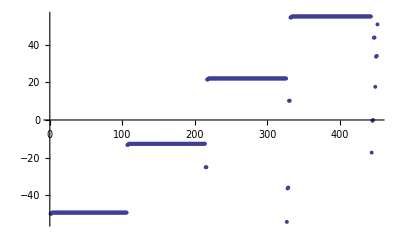

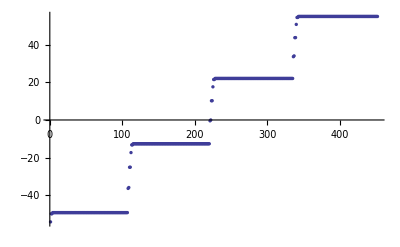

```mathematica
(*Find minimal Energydistance of found levels to initial levels*)

Clear[EDiff]
EDiff={};
For[i=1,i≤Length[NList],i++,EDiff=Join[EDiff,{(NList[[i,5]]-Subscript[E, 12])/10^9}]];
ListPlot[EDiff, PlotRange->{All,All},PlotStyle->PointSize[0.007]]
ListPlot[EDiff[[Ordering[EDiff]]], PlotRange->{All,All},PlotStyle->PointSize[0.006]]
```

```mathematica
NListTemp=NList[[Ordering[NList[[All,{5}]]]]] ;

(*Ordering NList beginning with highest Energy
LabelList is organized by energy also; it's an index for the NListTemp *)

LabelList={};
For[i=1,i≤Length[NList],i++,LabelList=Join[LabelList,{NListTemp[[i,1]]|NListTemp[[i,2]]|NListTemp[[i,3]]|NListTemp[[i,4]]}]]

(*Make List of Hilbert Space Basis level names for Plot of Energies*)

NList ;
LabelList

Clear[n,l,m,j,mj,np,lp,mp,jp,mjp,lj,ljp,Ξ,Ω,Ex,Ey,Ez,EField]
Clear[I0,E0,EFieldpi,EFieldsp,EFieldsm]

(*Calculation of r-Vector-Matrixelement <n,l,j,m|{x,y,z}|np,lp,jp,mp>(Vector) = RDip*ADip(Vector) for Angular and Radial Part (in atomic unit [Subscript[a, 0]]), ADip is a 3x1 Vector! *)
ADip[{n_,l_,j_,m_},{np_,lp_,jp_,mp_}]:=(√2)/2*(-1.)^(jp+l-1/2)*√(2.*jp+1)*SixJSymbol[{lp,1/2,jp},{j,1,l}]*(-1)^l*√((2*l+1)*(2*lp+1))*ThreeJSymbol[{l,0},{1,0},{lp,0}]*{ClebschGordan[{jp,mp},{1,-1},{j,m}]-ClebschGordan[{jp,mp},{1,1},{j,m}],I*ClebschGordan[{jp,mp},{1,-1},{j,m}]+I*ClebschGordan[{jp,mp},{1,1},{j,m}],√2*ClebschGordan[{jp,mp},{1,0},{j,m}]};
RDip[{n_,l_,lj_},{np_,lp_,ljp_}]:=RadIntE[ERadinte[lj,n],ERadinte[ljp,np],l,lp,1];

(*  Definition of Matrix Element Subscript[H, dipole]= RDip*ADip(Vector)(*.EField*) in unit [Subscript[a, 0]*Subscript[e, SI](*V/m*)]  *)
EMatrixelement[{n_,l_,j_,m_},{np_,lp_,jp_,mp_}]:=RDip[{n,l,Chooselj[l,j]},{np,lp,Chooselj[lp,jp]}]*ADip[{n,l,j,m},{np,lp,jp,mp}](*.EField*);

EMatrixelement[{60,1,3/2,3/2},{60,2,3/2,1/2}]


(*Fill up Matrix VMatrix with Sandwiched Efield Interaction <A|E*d|A'>*)
Clear[AI]
EMatrix=Array[E,{Length[NList],Length[NList]}];
EMatrix[[1,1]]
Timing[For[i=1,i≤Length[NList],i++,
		For[k=1,k≤Length[NList],k++,
If[((Abs[NList[[i,4]]-NList[[k,4]]]==1 ∨ Abs[NList[[i,4]]-NList[[k,4]]]==0))∧(Abs[NList[[i,2]]-NList[[k,2]]]==1),EMatrix[[i,k]]=EMatrixelement[{NList[[i,1]],NList[[i,2]],NList[[i,3]],NList[[i,4]]},{NList[[k,1]],NList[[k,2]],NList[[k,3]],NList[[k,4]]}],EMatrix[[i,k]]={0,0,0}] (*If m and l-parity*)
] 
] 
]
Clear[i,k,AI]

EMatrix[[1,1]]
```

{59|0|1/2|1/2,56|3|7/2|1/2,56|3|5/2|1/2,56|4|7/2|1/2,56|4|9/2|1/2,56|5|9/2|1/2,56|5|11/2|1/2,56|6|11/2|1/2,56|6|13/2|1/2,56|7|13/2|1/2,56|7|15/2|1/2,56|8|15/2|1/2,56|8|17/2|1/2,56|9|17/2|1/2,56|9|19/2|1/2,56|10|19/2|1/2,56|10|21/2|1/2,56|11|21/2|1/2,56|11|23/2|1/2,56|12|23/2|1/2,56|12|25/2|1/2,56|13|25/2|1/2,56|13|27/2|1/2,56|14|27/2|1/2,56|14|29/2|1/2,56|15|29/2|1/2,56|15|31/2|1/2,56|16|31/2|1/2,56|16|33/2|1/2,56|17|33/2|1/2,56|17|35/2|1/2,56|18|35/2|1/2,56|18|37/2|1/2,56|19|37/2|1/2,56|19|39/2|1/2,56|20|39/2|1/2,56|20|41/2|1/2,56|21|41/2|1/2,56|21|43/2|1/2,56|22|43/2|1/2,56|22|45/2|1/2,56|23|45/2|1/2,56|23|47/2|1/2,56|24|47/2|1/2,56|24|49/2|1/2,56|25|49/2|1/2,56|25|51/2|1/2,56|26|51/2|1/2,56|26|53/2|1/2,56|27|53/2|1/2,56|27|55/2|1/2,56|28|55/2|1/2,56|28|57/2|1/2,56|29|57/2|1/2,56|29|59/2|1/2,56|30|59/2|1/2,56|30|61/2|1/2,56|31|61/2|1/2,56|31|63/2|1/2,56|32|63/2|1/2,56|32|65/2|1/2,56|33|65/2|1/2,56|33|67/2|1/2,56|34|67/2|1/2,56|34|69/2|1/2,56|35|69/2|1/2,56|35|71/2|1/2,56|36|71/2|1/2,56|36|73/2|1/2,56|37|73/2|1/2,56|37|75/2|1/2,56|38|75/2|1/2,56|38|77/2|1/2,56|39|77/2|1/2,56|39|79/2|1/2,56|40|79/2|1/2,56|40|81/2|1/2,56|41|81/2|1/2,56|41|83/2|1/2,56|42|83/2|1/2,56|42|85/2|1/2,56|43|85/2|1/2,56|43|87/2|1/2,56|44|87/2|1/2,56|44|89/2|1/2,56|45|89/2|1/2,56|45|91/2|1/2,56|46|91/2|1/2,56|46|93/2|1/2,56|47|93/2|1/2,56|47|95/2|1/2,56|48|95/2|1/2,56|48|97/2|1/2,56|49|97/2|1/2,56|49|99/2|1/2,56|50|99/2|1/2,56|50|101/2|1/2,56|51|101/2|1/2,56|51|103/2|1/2,56|52|103/2|1/2,56|52|105/2|1/2,56|53|105/2|1/2,56|53|107/2|1/2,56|54|107/2|1/2,56|54|109/2|1/2,56|55|109/2|1/2,56|55|111/2|1/2,59|1|1/2|1/2,59|1|3/2|1/2,58|2|3/2|1/2,58|2|5/2|1/2,60|0|1/2|1/2,57|3|7/2|1/2,57|3|5/2|1/2,57|4|7/2|1/2,57|4|9/2|1/2,57|5|9/2|1/2,57|5|11/2|1/2,57|6|11/2|1/2,57|6|13/2|1/2,57|7|13/2|1/2,57|7|15/2|1/2,57|8|15/2|1/2,57|8|17/2|1/2,57|9|17/2|1/2,57|9|19/2|1/2,57|10|19/2|1/2,57|10|21/2|1/2,57|11|21/2|1/2,57|11|23/2|1/2,57|12|23/2|1/2,57|12|25/2|1/2,57|13|25/2|1/2,57|13|27/2|1/2,57|14|27/2|1/2,57|14|29/2|1/2,57|15|29/2|1/2,57|15|31/2|1/2,57|16|31/2|1/2,57|16|33/2|1/2,57|17|33/2|1/2,57|17|35/2|1/2,57|18|35/2|1/2,57|18|37/2|1/2,57|19|37/2|1/2,57|19|39/2|1/2,57|20|39/2|1/2,57|20|41/2|1/2,57|21|41/2|1/2,57|21|43/2|1/2,57|22|43/2|1/2,57|22|45/2|1/2,57|23|45/2|1/2,57|23|47/2|1/2,57|24|47/2|1/2,57|24|49/2|1/2,57|25|49/2|1/2,57|25|51/2|1/2,57|26|51/2|1/2,57|26|53/2|1/2,57|27|53/2|1/2,57|27|55/2|1/2,57|28|55/2|1/2,57|28|57/2|1/2,57|29|57/2|1/2,57|29|59/2|1/2,57|30|59/2|1/2,57|30|61/2|1/2,57|31|61/2|1/2,57|31|63/2|1/2,57|32|63/2|1/2,57|32|65/2|1/2,57|33|65/2|1/2,57|33|67/2|1/2,57|34|67/2|1/2,57|34|69/2|1/2,57|35|69/2|1/2,57|35|71/2|1/2,57|36|71/2|1/2,57|36|73/2|1/2,57|37|73/2|1/2,57|37|75/2|1/2,57|38|75/2|1/2,57|38|77/2|1/2,57|39|77/2|1/2,57|39|79/2|1/2,57|40|79/2|1/2,57|40|81/2|1/2,57|41|81/2|1/2,57|41|83/2|1/2,57|42|83/2|1/2,57|42|85/2|1/2,57|43|85/2|1/2,57|43|87/2|1/2,57|44|87/2|1/2,57|44|89/2|1/2,57|45|89/2|1/2,57|45|91/2|1/2,57|46|91/2|1/2,57|46|93/2|1/2,57|47|93/2|1/2,57|47|95/2|1/2,57|48|95/2|1/2,57|48|97/2|1/2,57|49|97/2|1/2,57|49|99/2|1/2,57|50|99/2|1/2,57|50|101/2|1/2,57|51|101/2|1/2,57|51|103/2|1/2,57|52|103/2|1/2,57|52|105/2|1/2,57|53|105/2|1/2,57|53|107/2|1/2,57|54|107/2|1/2,57|54|109/2|1/2,57|55|109/2|1/2,57|55|111/2|1/2,57|56|111/2|1/2,57|56|113/2|1/2,60|1|1/2|1/2,60|1|3/2|1/2,59|2|3/2|1/2,59|2|5/2|1/2,61|0|1/2|1/2,58|3|7/2|1/2,58|3|5/2|1/2,58|4|7/2|1/2,58|4|9/2|1/2,58|5|9/2|1/2,58|5|11/2|1/2,58|6|11/2|1/2,58|6|13/2|1/2,58|7|13/2|1/2,58|7|15/2|1/2,58|8|15/2|1/2,58|8|17/2|1/2,58|9|17/2|1/2,58|9|19/2|1/2,58|10|19/2|1/2,58|10|21/2|1/2,58|11|21/2|1/2,58|11|23/2|1/2,58|12|23/2|1/2,58|12|25/2|1/2,58|13|25/2|1/2,58|13|27/2|1/2,58|14|27/2|1/2,58|14|29/2|1/2,58|15|29/2|1/2,58|15|31/2|1/2,58|16|31/2|1/2,58|16|33/2|1/2,58|17|33/2|1/2,58|17|35/2|1/2,58|18|35/2|1/2,58|18|37/2|1/2,58|19|37/2|1/2,58|19|39/2|1/2,58|20|39/2|1/2,58|20|41/2|1/2,58|21|41/2|1/2,58|21|43/2|1/2,58|22|43/2|1/2,58|22|45/2|1/2,58|23|45/2|1/2,58|23|47/2|1/2,58|24|47/2|1/2,58|24|49/2|1/2,58|25|49/2|1/2,58|25|51/2|1/2,58|26|51/2|1/2,58|26|53/2|1/2,58|27|53/2|1/2,58|27|55/2|1/2,58|28|55/2|1/2,58|28|57/2|1/2,58|29|57/2|1/2,58|29|59/2|1/2,58|30|59/2|1/2,58|30|61/2|1/2,58|31|61/2|1/2,58|31|63/2|1/2,58|32|63/2|1/2,58|32|65/2|1/2,58|33|65/2|1/2,58|33|67/2|1/2,58|34|67/2|1/2,58|34|69/2|1/2,58|35|69/2|1/2,58|35|71/2|1/2,58|36|71/2|1/2,58|36|73/2|1/2,58|37|73/2|1/2,58|37|75/2|1/2,58|38|75/2|1/2,58|38|77/2|1/2,58|39|77/2|1/2,58|39|79/2|1/2,58|40|79/2|1/2,58|40|81/2|1/2,58|41|81/2|1/2,58|41|83/2|1/2,58|42|83/2|1/2,58|42|85/2|1/2,58|43|85/2|1/2,58|43|87/2|1/2,58|44|87/2|1/2,58|44|89/2|1/2,58|45|89/2|1/2,58|45|91/2|1/2,58|46|91/2|1/2,58|46|93/2|1/2,58|47|93/2|1/2,58|47|95/2|1/2,58|48|95/2|1/2,58|48|97/2|1/2,58|49|97/2|1/2,58|49|99/2|1/2,58|50|99/2|1/2,58|50|101/2|1/2,58|51|101/2|1/2,58|51|103/2|1/2,58|52|103/2|1/2,58|52|105/2|1/2,58|53|105/2|1/2,58|53|107/2|1/2,58|54|107/2|1/2,58|54|109/2|1/2,58|55|109/2|1/2,58|55|111/2|1/2,58|56|111/2|1/2,58|56|113/2|1/2,58|57|113/2|1/2,58|57|115/2|1/2,61|1|1/2|1/2,61|1|3/2|1/2,60|2|3/2|1/2,60|2|5/2|1/2,62|0|1/2|1/2,59|3|7/2|1/2,59|3|5/2|1/2,59|4|7/2|1/2,59|4|9/2|1/2,59|5|9/2|1/2,59|5|11/2|1/2,59|6|11/2|1/2,59|6|13/2|1/2,59|7|13/2|1/2,59|7|15/2|1/2,59|8|15/2|1/2,59|8|17/2|1/2,59|9|17/2|1/2,59|9|19/2|1/2,59|10|19/2|1/2,59|10|21/2|1/2,59|11|21/2|1/2,59|11|23/2|1/2,59|12|23/2|1/2,59|12|25/2|1/2,59|13|25/2|1/2,59|13|27/2|1/2,59|14|27/2|1/2,59|14|29/2|1/2,59|15|29/2|1/2,59|15|31/2|1/2,59|16|31/2|1/2,59|16|33/2|1/2,59|17|33/2|1/2,59|17|35/2|1/2,59|18|35/2|1/2,59|18|37/2|1/2,59|19|37/2|1/2,59|19|39/2|1/2,59|20|39/2|1/2,59|20|41/2|1/2,59|21|41/2|1/2,59|21|43/2|1/2,59|22|43/2|1/2,59|22|45/2|1/2,59|23|45/2|1/2,59|23|47/2|1/2,59|24|47/2|1/2,59|24|49/2|1/2,59|25|49/2|1/2,59|25|51/2|1/2,59|26|51/2|1/2,59|26|53/2|1/2,59|27|53/2|1/2,59|27|55/2|1/2,59|28|55/2|1/2,59|28|57/2|1/2,59|29|57/2|1/2,59|29|59/2|1/2,59|30|59/2|1/2,59|30|61/2|1/2,59|31|61/2|1/2,59|31|63/2|1/2,59|32|63/2|1/2,59|32|65/2|1/2,59|33|65/2|1/2,59|33|67/2|1/2,59|34|67/2|1/2,59|34|69/2|1/2,59|35|69/2|1/2,59|35|71/2|1/2,59|36|71/2|1/2,59|36|73/2|1/2,59|37|73/2|1/2,59|37|75/2|1/2,59|38|75/2|1/2,59|38|77/2|1/2,59|39|77/2|1/2,59|39|79/2|1/2,59|40|79/2|1/2,59|40|81/2|1/2,59|41|81/2|1/2,59|41|83/2|1/2,59|42|83/2|1/2,59|42|85/2|1/2,59|43|85/2|1/2,59|43|87/2|1/2,59|44|87/2|1/2,59|44|89/2|1/2,59|45|89/2|1/2,59|45|91/2|1/2,59|46|91/2|1/2,59|46|93/2|1/2,59|47|93/2|1/2,59|47|95/2|1/2,59|48|95/2|1/2,59|48|97/2|1/2,59|49|97/2|1/2,59|49|99/2|1/2,59|50|99/2|1/2,59|50|101/2|1/2,59|51|101/2|1/2,59|51|103/2|1/2,59|52|103/2|1/2,59|52|105/2|1/2,59|53|105/2|1/2,59|53|107/2|1/2,59|54|107/2|1/2,59|54|109/2|1/2,59|55|109/2|1/2,59|55|111/2|1/2,59|56|111/2|1/2,59|56|113/2|1/2,59|57|113/2|1/2,59|57|115/2|1/2,59|58|115/2|1/2,59|58|117/2|1/2}

ClebschGordan::phy: ThreeJSymbol[{3/2, 1/2}, {1, -1}, {3/2, -3/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, 1/2}, {1, 0}, {3/2, -3/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{4.28091,0.-4.28091 ⅈ,0.}

ⅇ[1,1]

ClebschGordan::phy: ThreeJSymbol[{7/2, 1/2}, {1, -1}, {5/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{7/2, 1/2}, {1, 1}, {5/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{7/2, 1/2}, {1, -1}, {5/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{4, 1/2, 9/2}, {5/2, 1, 3}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, 1/2}, {1, -1}, {5/2, -1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, 1/2}, {1, 1}, {5/2, -1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, 1/2}, {1, -1}, {5/2, -1/2}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{4, 1/2, 9/2}, {5/2, 1, 3}] is not triangular.

General::stop: Further output of SixJSymbol :: tri will be suppressed during this calculation.

{28.485,Null}

{0,0,0}

```mathematica
(*Absolute Energies of disturbed levels:*)

Clear[i,f,R]
EI={};
EI
NList;
For[i=1,i≤Length[NList],i++,EI=Join[EI,{NList[[i,5]]} ] ] ;
EIList = {} ;
EI
EIList=EI;
EI;
EI=DiagonalMatrix[EI];
MatrixPlot[EI]
```

{}

{-1.04967×10^12,-1.04967×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.01315×10^12,-1.01315×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.02504×10^12,-1.02498×10^12,-9.78506×10^11,-9.78506×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-1.05398×10^12,-1.03624×10^12,-1.03576×10^12,-9.89787×10^11,-9.89731×10^11,-9.45608×10^11,-9.45609×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-1.01724×10^12,-1.00042×10^12,-9.99955×10^11,-9.56324×10^11,-9.56271×10^11,-9.82389×10^11,-9.66416×10^11,-9.65979×10^11,-9.49297×10^11}

-Graphics-

```mathematica
EField={0,0,1} ;
MatrixPlot[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]
MatrixPlot[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]
Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]
```

-Graphics-

-Graphics-

{-1053.98,-1049.67,-1049.67,-1049.11,-1049.11,-1049.11,-1049.11,-1049.1,-1049.1,-1049.1,-1049.1,-1049.1,-1049.1,-1049.1,-1049.1,-1049.09,-1049.09,-1049.09,-1049.09,-1049.09,-1049.09,-1049.09,-1049.09,-1049.08,-1049.08,-1049.08,-1049.08,-1049.08,-1049.08,-1049.08,-1049.08,-1049.08,-1049.08,-1049.07,-1049.07,-1049.07,-1049.07,-1049.07,-1049.07,-1049.07,-1049.07,-1049.06,-1049.06,-1049.06,-1049.06,-1049.06,-1049.06,-1049.06,-1049.06,-1049.06,-1049.06,-1049.05,-1049.05,-1049.05,-1049.05,-1049.05,-1049.05,-1049.05,-1049.05,-1049.04,-1049.04,-1049.04,-1049.04,-1049.04,-1049.04,-1049.04,-1049.04,-1049.04,-1049.04,-1049.03,-1049.03,-1049.03,-1049.03,-1049.03,-1049.03,-1049.03,-1049.03,-1049.02,-1049.02,-1049.02,-1049.02,-1049.02,-1049.02,-1049.02,-1049.02,-1049.02,-1049.02,-1049.01,-1049.01,-1049.01,-1049.01,-1049.01,-1049.01,-1049.01,-1049.01,-1049.,-1049.,-1049.,-1049.,-1049.,-1049.,-1049.,-1049.,-1048.99,-1048.99,-1048.99,-1048.99,-1036.24,-1035.76,-1025.04,-1024.98,-1017.24,-1013.15,-1013.15,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.6,-1012.6,-1012.6,-1012.6,-1012.6,-1012.6,-1012.6,-1012.6,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.5,-1012.5,-1000.42,-999.955,-989.787,-989.731,-982.389,-978.508,-978.507,-978.012,-978.011,-978.009,-978.009,-978.007,-978.006,-978.004,-978.004,-978.002,-978.002,-977.999,-977.999,-977.997,-977.997,-977.995,-977.994,-977.992,-977.992,-977.99,-977.99,-977.988,-977.987,-977.985,-977.985,-977.983,-977.983,-977.981,-977.98,-977.978,-977.978,-977.976,-977.976,-977.974,-977.973,-977.971,-977.971,-977.969,-977.969,-977.967,-977.967,-977.964,-977.964,-977.962,-977.962,-977.96,-977.96,-977.957,-977.957,-977.955,-977.955,-977.953,-977.953,-977.95,-977.95,-977.948,-977.948,-977.946,-977.946,-977.943,-977.943,-977.941,-977.941,-977.939,-977.939,-977.936,-977.936,-977.934,-977.934,-977.932,-977.932,-977.93,-977.929,-977.927,-977.927,-977.925,-977.925,-977.923,-977.923,-977.92,-977.92,-977.918,-977.918,-977.916,-977.916,-977.913,-977.913,-977.911,-977.911,-977.909,-977.909,-977.906,-977.906,-977.904,-977.904,-977.902,-977.901,-977.899,-977.899,-977.897,-977.897,-977.894,-977.894,-977.892,-977.892,-977.89,-977.889,-977.887,-977.887,-966.416,-965.979,-956.324,-956.271,-949.297,-945.611,-945.61,-945.144,-945.144,-945.141,-945.141,-945.139,-945.139,-945.136,-945.136,-945.134,-945.134,-945.131,-945.131,-945.129,-945.129,-945.127,-945.127,-945.124,-945.124,-945.122,-945.122,-945.119,-945.119,-945.117,-945.117,-945.115,-945.115,-945.112,-945.112,-945.11,-945.11,-945.108,-945.108,-945.105,-945.105,-945.103,-945.103,-945.101,-945.1,-945.098,-945.098,-945.096,-945.096,-945.093,-945.093,-945.091,-945.091,-945.089,-945.089,-945.086,-945.086,-945.084,-945.084,-945.082,-945.082,-945.079,-945.079,-945.077,-945.077,-945.075,-945.075,-945.072,-945.072,-945.07,-945.07,-945.068,-945.068,-945.065,-945.065,-945.063,-945.063,-945.06,-945.06,-945.058,-945.058,-945.056,-945.056,-945.053,-945.053,-945.051,-945.051,-945.049,-945.049,-945.046,-945.046,-945.044,-945.044,-945.042,-945.042,-945.039,-945.039,-945.037,-945.037,-945.034,-945.034,-945.032,-945.032,-945.03,-945.03,-945.027,-945.027,-945.025,-945.025,-945.023,-945.022,-945.02,-945.02,-945.018,-945.017,-945.015,-945.015}

{{300,-67.029,59|0|1/2|1/2},{300,-66.9115,56|3|7/2|1/2},{300,-66.3222,56|3|5/2|1/2},{300,-66.2322,56|4|7/2|1/2},{300,-65.6332,56|4|9/2|1/2},{300,-65.558,56|5|9/2|1/2},{300,-64.9523,56|5|11/2|1/2},{300,-64.887,56|6|11/2|1/2},{300,-64.2761,56|6|13/2|1/2},{300,-64.2183,56|7|13/2|1/2},{300,-63.6033,56|7|15/2|1/2},{300,-63.5512,56|8|15/2|1/2},{300,-62.9328,56|8|17/2|1/2},{300,-62.8855,56|9|17/2|1/2},{300,-62.2641,56|9|19/2|1/2},{300,-62.2208,56|10|19/2|1/2},{300,-61.5969,56|10|21/2|1/2},{300,-61.5569,56|11|21/2|1/2},{300,-60.9308,56|11|23/2|1/2},{300,-60.8937,56|12|23/2|1/2},{300,-60.2659,56|12|25/2|1/2},{300,-60.231,56|13|25/2|1/2},{300,-59.6022,56|13|27/2|1/2},{300,-59.5689,56|14|27/2|1/2},{300,-58.94,56|14|29/2|1/2},{300,-58.9071,56|15|29/2|1/2},{300,-58.2821,56|15|31/2|1/2},{300,-58.2456,56|16|31/2|1/2},{300,-57.6831,56|16|33/2|1/2},{300,-57.5844,56|17|33/2|1/2},{300,-57.5016,56|17|35/2|1/2},{300,-56.9305,56|18|35/2|1/2},{300,-56.9234,56|18|37/2|1/2},{300,-56.2744,56|19|37/2|1/2},{300,-56.2625,56|19|39/2|1/2},{300,-55.614,56|20|39/2|1/2},{300,-55.6017,56|20|41/2|1/2},{300,-54.9527,56|21|41/2|1/2},{300,-54.941,56|21|43/2|1/2},{300,-54.2911,56|22|43/2|1/2},{300,-54.2804,56|22|45/2|1/2},{300,-53.6292,56|23|45/2|1/2},{300,-53.6197,56|23|47/2|1/2},{300,-52.9673,56|24|47/2|1/2},{300,-52.9589,56|24|49/2|1/2},{300,-52.3052,56|25|49/2|1/2},{300,-52.2981,56|25|51/2|1/2},{300,-51.6429,56|26|51/2|1/2},{300,-51.6371,56|26|53/2|1/2},{300,-50.9805,56|27|53/2|1/2},{300,-50.9759,56|27|55/2|1/2},{300,-50.3178,56|28|55/2|1/2},{300,-50.3145,56|28|57/2|1/2},{300,-49.655,56|29|57/2|1/2},{300,-49.653,56|29|59/2|1/2},{300,-48.9921,56|30|59/2|1/2},{300,-48.9913,56|30|61/2|1/2},{300,-48.3296,56|31|61/2|1/2},{300,-48.329,56|31|63/2|1/2},{300,-47.6678,56|32|63/2|1/2},{300,-47.666,56|32|65/2|1/2},{300,-47.0059,56|33|65/2|1/2},{300,-47.0029,56|33|67/2|1/2},{300,-46.344,56|34|67/2|1/2},{300,-46.3398,56|34|69/2|1/2},{300,-45.6821,56|35|69/2|1/2},{300,-45.6767,56|35|71/2|1/2},{300,-45.0202,56|36|71/2|1/2},{300,-45.0138,56|36|73/2|1/2},{300,-44.3586,56|37|73/2|1/2},{300,-44.3512,56|37|75/2|1/2},{300,-43.6976,56|38|75/2|1/2},{300,-43.6894,56|38|77/2|1/2},{300,-43.0377,56|39|77/2|1/2},{300,-43.0292,56|39|79/2|1/2},{300,-42.3804,56|40|79/2|1/2},{300,-42.3725,56|40|81/2|1/2},{300,-41.7303,56|41|81/2|1/2},{300,-41.7232,56|41|83/2|1/2},{300,-41.109,56|42|83/2|1/2},{300,-41.0894,56|42|85/2|1/2},{300,-40.5801,56|43|85/2|1/2},{300,-40.5104,56|43|87/2|1/2},{300,-40.1248,56|44|87/2|1/2},{300,-40.0545,56|44|89/2|1/2},{300,-39.5679,56|45|89/2|1/2},{300,-39.5463,56|45|91/2|1/2},{300,-38.9464,56|46|91/2|1/2},{300,-38.9223,56|46|93/2|1/2},{300,-38.2975,56|47|93/2|1/2},{300,-38.2686,56|47|95/2|1/2},{300,-37.6377,56|48|95/2|1/2},{300,-37.6052,56|48|97/2|1/2},{300,-36.9726,56|49|97/2|1/2},{300,-36.9366,56|49|99/2|1/2},{300,-36.3043,56|50|99/2|1/2},{300,-36.2645,56|50|101/2|1/2},{300,-35.6333,56|51|101/2|1/2},{300,-35.5891,56|51|103/2|1/2},{300,-34.9598,56|52|103/2|1/2},{300,-34.9104,56|52|105/2|1/2},{300,-34.2835,56|53|105/2|1/2},{300,-34.2274,56|53|107/2|1/2},{300,-33.6038,56|54|107/2|1/2},{300,-33.5387,56|54|109/2|1/2},{300,-32.9194,56|55|109/2|1/2},{300,-32.8406,56|55|111/2|1/2},{300,-32.227,59|1|1/2|1/2},{300,-32.1221,59|1|3/2|1/2},{300,-30.8931,58|2|3/2|1/2},{300,-30.7553,58|2|5/2|1/2},{300,-30.2028,60|0|1/2|1/2},{300,-30.0965,57|3|7/2|1/2},{300,-29.5297,57|3|5/2|1/2},{300,-29.4435,57|4|7/2|1/2},{300,-28.865,57|4|9/2|1/2},{300,-28.7948,57|5|9/2|1/2},{300,-28.2054,57|5|11/2|1/2},{300,-28.1484,57|6|11/2|1/2},{300,-27.5488,57|6|13/2|1/2},{300,-27.503,57|7|13/2|1/2},{300,-26.8936,57|7|15/2|1/2},{300,-26.8569,57|8|15/2|1/2},{300,-26.2387,57|8|17/2|1/2},{300,-26.2092,57|9|17/2|1/2},{300,-25.5834,57|9|19/2|1/2},{300,-25.5593,57|10|19/2|1/2},{300,-24.9271,57|10|21/2|1/2},{300,-24.907,57|11|21/2|1/2},{300,-24.2697,57|11|23/2|1/2},{300,-24.2524,57|12|23/2|1/2},{300,-23.611,57|12|25/2|1/2},{300,-23.5957,57|13|25/2|1/2},{300,-22.9513,57|13|27/2|1/2},{300,-22.9372,57|14|27/2|1/2},{300,-22.2907,57|14|29/2|1/2},{300,-22.277,57|15|29/2|1/2},{300,-21.6296,57|15|31/2|1/2},{300,-21.6155,57|16|31/2|1/2},{300,-20.9687,57|16|33/2|1/2},{300,-20.9528,57|17|33/2|1/2},{300,-20.3097,57|17|35/2|1/2},{300,-20.289,57|18|35/2|1/2},{300,-19.6575,57|18|37/2|1/2},{300,-19.6243,57|19|37/2|1/2},{300,-19.0429,57|19|39/2|1/2},{300,-18.9589,57|20|39/2|1/2},{300,-18.6468,57|20|41/2|1/2},{300,-18.2928,57|21|41/2|1/2},{300,-18.2156,57|21|43/2|1/2},{300,-17.6261,57|22|43/2|1/2},{300,-17.59,57|22|45/2|1/2},{300,-16.9589,57|23|45/2|1/2},{300,-16.934,57|23|47/2|1/2},{300,-16.2913,57|24|47/2|1/2},{300,-16.2711,57|24|49/2|1/2},{300,-15.6233,57|25|49/2|1/2},{300,-15.6054,57|25|51/2|1/2},{300,-14.9549,57|26|51/2|1/2},{300,-14.9381,57|26|53/2|1/2},{300,-14.2861,57|27|53/2|1/2},{300,-14.2699,57|27|55/2|1/2},{300,-13.617,57|28|55/2|1/2},{300,-13.6008,57|28|57/2|1/2},{300,-12.9476,57|29|57/2|1/2},{300,-12.9312,57|29|59/2|1/2},{300,-12.278,57|30|59/2|1/2},{300,-12.2612,57|30|61/2|1/2},{300,-11.6082,57|31|61/2|1/2},{300,-11.5908,57|31|63/2|1/2},{300,-10.9383,57|32|63/2|1/2},{300,-10.9202,57|32|65/2|1/2},{300,-10.2683,57|33|65/2|1/2},{300,-10.2493,57|33|67/2|1/2},{300,-9.59825,57|34|67/2|1/2},{300,-9.57827,57|34|69/2|1/2},{300,-8.92815,57|35|69/2|1/2},{300,-8.90704,57|35|71/2|1/2},{300,-8.25805,57|36|71/2|1/2},{300,-8.23562,57|36|73/2|1/2},{300,-7.58806,57|37|73/2|1/2},{300,-7.56405,57|37|75/2|1/2},{300,-6.91843,57|38|75/2|1/2},{300,-6.89245,57|38|77/2|1/2},{300,-6.24988,57|39|77/2|1/2},{300,-6.22109,57|39|79/2|1/2},{300,-5.58485,57|40|79/2|1/2},{300,-5.55079,57|40|81/2|1/2},{300,-4.93907,57|41|81/2|1/2},{300,-4.88527,57|41|83/2|1/2},{300,-4.51704,57|42|83/2|1/2},{300,-4.27432,57|42|85/2|1/2},{300,-4.16272,57|43|85/2|1/2},{300,-4.03521,57|43|87/2|1/2},{300,-3.52691,57|44|87/2|1/2},{300,-3.49494,57|44|89/2|1/2},{300,-2.86152,57|45|89/2|1/2},{300,-2.83133,57|45|91/2|1/2},{300,-2.19077,57|46|91/2|1/2},{300,-2.15887,57|46|93/2|1/2},{300,-1.51778,57|47|93/2|1/2},{300,-1.48364,57|47|95/2|1/2},{300,-0.843357,57|48|95/2|1/2},{300,-0.806715,57|48|97/2|1/2},{300,-0.167726,57|49|97/2|1/2},{300,-0.128321,57|49|99/2|1/2},{300,0.50908,57|50|99/2|1/2},{300,0.551574,57|50|101/2|1/2},{300,1.18713,57|51|101/2|1/2},{300,1.23313,57|51|103/2|1/2},{300,1.86658,57|52|103/2|1/2},{300,1.91661,57|52|105/2|1/2},{300,2.54755,57|53|105/2|1/2},{300,2.60208,57|53|107/2|1/2},{300,3.15225,57|54|107/2|1/2},{300,3.22471,57|54|109/2|1/2},{300,3.28308,57|55|109/2|1/2},{300,3.29675,57|55|111/2|1/2},{300,3.8693,57|56|111/2|1/2},{300,3.90852,57|56|113/2|1/2},{300,3.97727,60|1|1/2|1/2},{300,3.99695,60|1|3/2|1/2},{300,4.56839,59|2|3/2|1/2},{300,4.59703,59|2|5/2|1/2},{300,4.66454,61|0|1/2|1/2},{300,4.7047,58|3|7/2|1/2},{300,5.26077,58|3|5/2|1/2},{300,5.29222,58|4|7/2|1/2},{300,5.34749,58|4|9/2|1/2},{300,5.4297,58|5|9/2|1/2},{300,5.95045,58|5|11/2|1/2},{300,5.99996,58|6|11/2|1/2},{300,6.62318,58|6|13/2|1/2},{300,6.66598,58|7|13/2|1/2},{300,7.2925,58|7|15/2|1/2},{300,7.32878,58|8|15/2|1/2},{300,7.95833,58|8|17/2|1/2},{300,7.98881,58|9|17/2|1/2},{300,8.62135,58|9|19/2|1/2},{300,8.64695,58|10|19/2|1/2},{300,9.28246,58|10|21/2|1/2},{300,9.30418,58|11|21/2|1/2},{300,9.94261,58|11|23/2|1/2},{300,9.96151,58|12|23/2|1/2},{300,10.6027,58|12|25/2|1/2},{300,10.6198,58|13|25/2|1/2},{300,11.2635,58|13|27/2|1/2},{300,11.2796,58|14|27/2|1/2},{300,11.9252,58|14|29/2|1/2},{300,11.9414,58|15|29/2|1/2},{300,12.5879,58|15|31/2|1/2},{300,12.6053,58|16|31/2|1/2},{300,13.2513,58|16|33/2|1/2},{300,13.2713,58|17|33/2|1/2},{300,13.9141,58|17|35/2|1/2},{300,13.9392,58|18|35/2|1/2},{300,14.5734,58|18|37/2|1/2},{300,14.609,58|19|37/2|1/2},{300,15.2193,58|19|39/2|1/2},{300,15.2804,58|20|39/2|1/2},{300,15.7993,58|20|41/2|1/2},{300,15.9532,58|21|41/2|1/2},{300,16.2089,58|21|43/2|1/2},{300,16.6273,58|22|43/2|1/2},{300,16.7183,58|22|45/2|1/2},{300,17.3024,58|23|45/2|1/2},{300,17.3518,58|23|47/2|1/2},{300,17.9786,58|24|47/2|1/2},{300,18.0132,58|24|49/2|1/2},{300,18.6556,58|25|49/2|1/2},{300,18.6832,58|25|51/2|1/2},{300,19.3334,58|26|51/2|1/2},{300,19.3573,58|26|53/2|1/2},{300,20.012,58|27|53/2|1/2},{300,20.0336,58|27|55/2|1/2},{300,20.6912,58|28|55/2|1/2},{300,20.7117,58|28|57/2|1/2},{300,21.3711,58|29|57/2|1/2},{300,21.3909,58|29|59/2|1/2},{300,22.0516,58|30|59/2|1/2},{300,22.0712,58|30|61/2|1/2},{300,22.7325,58|31|61/2|1/2},{300,22.7522,58|31|63/2|1/2},{300,23.4138,58|32|63/2|1/2},{300,23.4338,58|32|65/2|1/2},{300,24.0954,58|33|65/2|1/2},{300,24.116,58|33|67/2|1/2},{300,24.7772,58|34|67/2|1/2},{300,24.7986,58|34|69/2|1/2},{300,25.4591,58|35|69/2|1/2},{300,25.4816,58|35|71/2|1/2},{300,26.1411,58|36|71/2|1/2},{300,26.165,58|36|73/2|1/2},{300,26.823,58|37|73/2|1/2},{300,26.8488,58|37|75/2|1/2},{300,27.5041,58|38|75/2|1/2},{300,27.5328,58|38|77/2|1/2},{300,28.1825,58|39|77/2|1/2},{300,28.217,58|39|79/2|1/2},{300,28.8461,58|40|79/2|1/2},{300,28.901,58|40|81/2|1/2},{300,29.2982,58|41|81/2|1/2},{300,29.5837,58|41|83/2|1/2},{300,29.6243,58|42|83/2|1/2},{300,30.2588,58|42|85/2|1/2},{300,30.2705,58|43|85/2|1/2},{300,30.746,58|43|87/2|1/2},{300,30.9482,58|44|87/2|1/2},{300,31.01,58|44|89/2|1/2},{300,31.6309,58|45|89/2|1/2},{300,31.6651,58|45|91/2|1/2},{300,32.3156,58|46|91/2|1/2},{300,32.3479,58|46|93/2|1/2},{300,33.0013,58|47|93/2|1/2},{300,33.0344,58|47|95/2|1/2},{300,33.6878,58|48|95/2|1/2},{300,33.7225,58|48|97/2|1/2},{300,34.375,58|49|97/2|1/2},{300,34.4116,58|49|99/2|1/2},{300,35.0629,58|50|99/2|1/2},{300,35.1014,58|50|101/2|1/2},{300,35.751,58|51|101/2|1/2},{300,35.7907,58|51|103/2|1/2},{300,36.0809,58|52|103/2|1/2},{300,36.1886,58|52|105/2|1/2},{300,36.4419,58|53|105/2|1/2},{300,36.4846,58|53|107/2|1/2},{300,36.8229,58|54|107/2|1/2},{300,36.9021,58|54|109/2|1/2},{300,37.1348,58|55|109/2|1/2},{300,37.1811,58|55|111/2|1/2},{300,37.5427,58|56|111/2|1/2},{300,37.6073,58|56|113/2|1/2},{300,37.8298,58|57|113/2|1/2},{300,37.8807,58|57|115/2|1/2},{300,38.2518,61|1|1/2|1/2},{300,38.3073,61|1|3/2|1/2},{300,38.5271,60|2|3/2|1/2},{300,38.5841,60|2|5/2|1/2},{300,38.9545,62|0|1/2|1/2},{300,39.0036,59|3|7/2|1/2},{300,39.2274,59|3|5/2|1/2},{300,39.2931,59|4|7/2|1/2},{300,39.6528,59|4|9/2|1/2},{300,39.6973,59|5|9/2|1/2},{300,39.9317,59|5|11/2|1/2},{300,40.0111,59|6|11/2|1/2},{300,40.3479,59|6|13/2|1/2},{300,40.3887,59|7|13/2|1/2},{300,40.6427,59|7|15/2|1/2},{300,40.7487,59|8|15/2|1/2},{300,41.0407,59|8|17/2|1/2},{300,41.0775,59|9|17/2|1/2},{300,41.7094,59|9|19/2|1/2},{300,41.755,59|10|19/2|1/2},{300,42.3803,59|10|21/2|1/2},{300,42.4309,59|11|21/2|1/2},{300,43.0483,59|11|23/2|1/2},{300,43.1042,59|12|23/2|1/2},{300,43.7141,59|12|25/2|1/2},{300,43.7752,59|13|25/2|1/2},{300,44.379,59|13|27/2|1/2},{300,44.4447,59|14|27/2|1/2},{300,45.0445,59|14|29/2|1/2},{300,45.1137,59|15|29/2|1/2},{300,45.7118,59|15|31/2|1/2},{300,45.7831,59|16|31/2|1/2},{300,46.3817,59|16|33/2|1/2},{300,46.4538,59|17|33/2|1/2},{300,47.0542,59|17|35/2|1/2},{300,47.1261,59|18|35/2|1/2},{300,47.7293,59|18|37/2|1/2},{300,47.8005,59|19|37/2|1/2},{300,48.4064,59|19|39/2|1/2},{300,48.4769,59|20|39/2|1/2},{300,49.0851,59|20|41/2|1/2},{300,49.1553,59|21|41/2|1/2},{300,49.7649,59|21|43/2|1/2},{300,49.8355,59|22|43/2|1/2},{300,50.4451,59|22|45/2|1/2},{300,50.5172,59|23|45/2|1/2},{300,51.125,59|23|47/2|1/2},{300,51.2002,59|24|47/2|1/2},{300,51.8036,59|24|49/2|1/2},{300,51.8843,59|25|49/2|1/2},{300,52.4794,59|25|51/2|1/2},{300,52.5694,59|26|51/2|1/2},{300,53.1497,59|26|53/2|1/2},{300,53.2553,59|27|53/2|1/2},{300,53.8092,59|27|55/2|1/2},{300,53.942,59|28|55/2|1/2},{300,54.4469,59|28|57/2|1/2},{300,54.6292,59|29|57/2|1/2},{300,55.0466,59|29|59/2|1/2},{300,55.3171,59|30|59/2|1/2},{300,55.6135,59|30|61/2|1/2},{300,56.0053,59|31|61/2|1/2},{300,56.1974,59|31|63/2|1/2},{300,56.6939,59|32|63/2|1/2},{300,56.8232,59|32|65/2|1/2},{300,57.3827,59|33|65/2|1/2},{300,57.4775,59|33|67/2|1/2},{300,58.0717,59|34|67/2|1/2},{300,58.1466,59|34|69/2|1/2},{300,58.7609,59|35|69/2|1/2},{300,58.8237,59|35|71/2|1/2},{300,59.4503,59|36|71/2|1/2},{300,59.5052,59|36|73/2|1/2},{300,60.1398,59|37|73/2|1/2},{300,60.1896,59|37|75/2|1/2},{300,60.8296,59|38|75/2|1/2},{300,60.876,59|38|77/2|1/2},{300,61.5196,59|39|77/2|1/2},{300,61.5638,59|39|79/2|1/2},{300,62.2098,59|40|79/2|1/2},{300,62.2527,59|40|81/2|1/2},{300,62.9003,59|41|81/2|1/2},{300,62.9426,59|41|83/2|1/2},{300,63.5912,59|42|83/2|1/2},{300,63.6332,59|42|85/2|1/2},{300,64.2823,59|43|85/2|1/2},{300,64.3246,59|43|87/2|1/2},{300,64.9738,59|44|87/2|1/2},{300,65.0167,59|44|89/2|1/2},{300,65.6657,59|45|89/2|1/2},{300,65.7096,59|45|91/2|1/2},{300,66.358,59|46|91/2|1/2},{300,66.4032,59|46|93/2|1/2},{300,67.0509,59|47|93/2|1/2},{300,67.0976,59|47|95/2|1/2},{300,67.7443,59|48|95/2|1/2},{300,67.7929,59|48|97/2|1/2},{300,68.4383,59|49|97/2|1/2},{300,68.4893,59|49|99/2|1/2},{300,69.1331,59|50|99/2|1/2},{300,69.1867,59|50|101/2|1/2},{300,69.8287,59|51|101/2|1/2},{300,69.8855,59|51|103/2|1/2},{300,70.5253,59|52|103/2|1/2},{300,70.5859,59|52|105/2|1/2},{300,71.223,59|53|105/2|1/2},{300,71.2882,59|53|107/2|1/2},{300,71.9222,59|54|107/2|1/2},{300,71.9931,59|54|109/2|1/2},{300,72.6231,59|55|109/2|1/2},{300,72.7013,59|55|111/2|1/2},{300,73.3262,59|56|111/2|1/2},{300,73.4145,59|56|113/2|1/2},{300,74.0326,59|57|113/2|1/2},{300,74.136,59|57|115/2|1/2},{300,74.7438,59|58|115/2|1/2},{300,74.8753,59|58|117/2|1/2}}

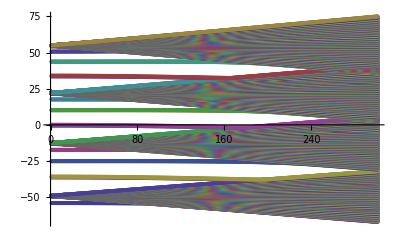

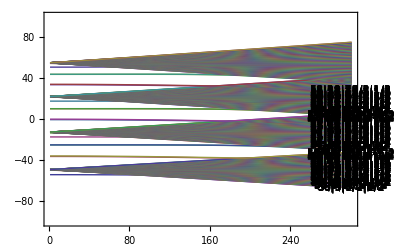

```mathematica
(*MultiListPlot: Generate Plot of Energies as a Function of EField*)
Clear[i,k,L,MPList,R]
MPList=Array[L,{Length[NList],2}];
Temp={};
EMIN=0;
EMAX=301;
ELabel=300;
(*Electric Field in [V/m], Efield perpend. to BEC, so E={Ex,0,Ez=0}, parasitic Fields typ. 1V/cm, Const. Field typ. 5V/cm*)
(*Subscript[EStark, 12]=2*EMatrixelement[{44,0,1/2,1/2},{44,0,1/2,1/2}]*Subscript[e, SI]*Subscript[a, 0]*)(*Calculate shift of 44s44s-44s44s for R->∞ for Offset substraction in Plot, [J]*)

E0=EMIN;
EStep=1;

For[i=1,i≤Length[NList],i++,MPList[[i]]={}];
Clear[i];
While[E0<EMAX,E0=E0+EStep;EField={0,0,E0};Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]-Subscript[E, 12]/10^9;For[i=1,i≤Length[NList],i++,MPList[[i]]=Join[MPList[[i]],{{E0,Temp[[i]]}}]  ]] ;
E0=EMIN;

Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.{0,0,ELabel}/h/10^9]-Subscript[E, 12]/10^9;(*Generate Labels for Levels*)
TempList=Array[T,Length[NList]];
For[i=1,i≤Length[NList],i++,TempList[[i]]={ELabel,Temp[[i]],LabelList[[i]]} ];
TempList

ListPlot[MPList]

Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-100,100}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

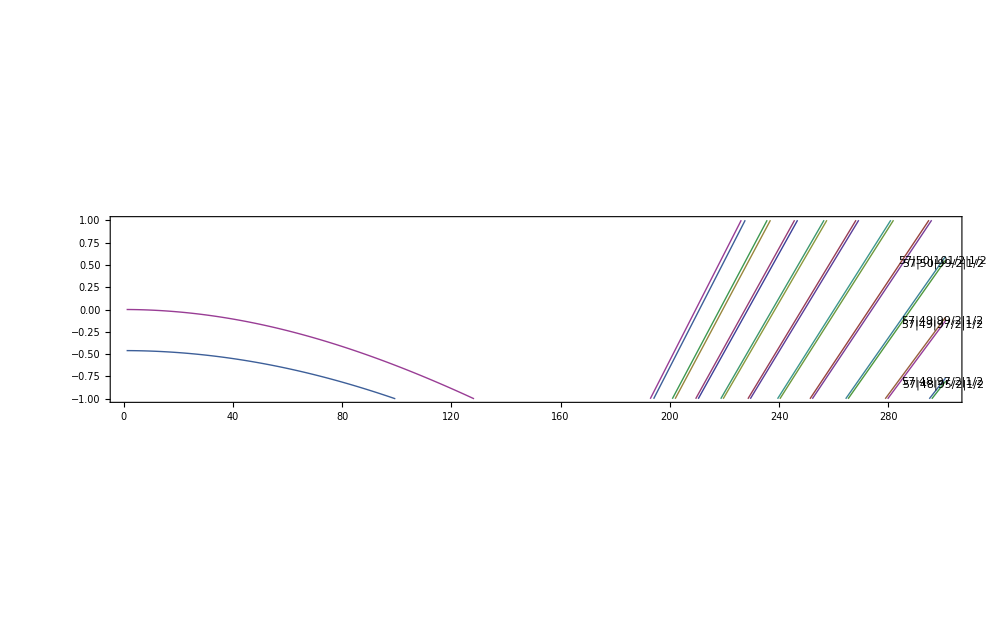

```mathematica
Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-1,1}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

```mathematica
LabelList[[222]]

MPList[[222]]

(*MPListExport: Generate list to be read by Origin *)

Efieldlist = {};

E0=EMIN;


While[E0<EMAX,E0=E0+EStep;Efieldlist=Join[Efieldlist,{E0}]] ;
E0=EMIN;

Efieldlist


Clear[i,k,L,MPListExport,R]
NE0=(EMAX-EMIN)/EStep;
MPListExport=Array[0,{Length[NList],NE0}];
(*Electric Field in [V/m], Efield perpend. to BEC, so E={Ex,0,Ez=0}, parasitic Fields typ. 1V/cm, Const. Field typ. 5V/cm*)
(*Subscript[EStark, 12]=2*EMatrixelement[{44,0,1/2,1/2},{44,0,1/2,1/2}]*Subscript[e, SI]*Subscript[a, 0]*)(*Calculate shift of 44s44s-44s44s for R->∞ for Offset substraction in Plot, [J]*)



Clear[i];
j=0;
While[j<NE0,
j++;
For[i=1,i≤Length[NList],i++,
MPListExport[[i,j]]=MPList[[i,j,2]] 
 ]
] ;

MPListExport


(*
Export["Stark_Shifts_around_60s.dat",MPListExport]
Export["Electric_fields_for_Stark_Shifts_around_60s.dat",Efieldlist]
*)
Export["60p_j3_2_mj1_2_stark_Shift.dat",MPList[[222]]]
```

60|1|3/2|1/2

{{1,-0.0000678712},{2,-0.000271479},{3,-0.000610803},{4,-0.00108581},{5,-0.00169646},{6,-0.0024427},{7,-0.00332445},{8,-0.00434163},{9,-0.00549414},{10,-0.00678189},{11,-0.00820474},{12,-0.00976258},{13,-0.0114552},{14,-0.0132826},{15,-0.0152444},{16,-0.0173406},{17,-0.0195709},{18,-0.0219351},{19,-0.024433},{20,-0.0270644},{21,-0.0298291},{22,-0.0327267},{23,-0.035757},{24,-0.0389198},{25,-0.0422147},{26,-0.0456415},{27,-0.0491998},{28,-0.0528893},{29,-0.0567098},{30,-0.0606607},{31,-0.0647419},{32,-0.0689529},{33,-0.0732933},{34,-0.0777628},{35,-0.082361},{36,-0.0870875},{37,-0.0919418},{38,-0.0969235},{39,-0.102032},{40,-0.107267},{41,-0.112629},{42,-0.118116},{43,-0.123728},{44,-0.129465},{45,-0.135326},{46,-0.141311},{47,-0.147419},{48,-0.153649},{49,-0.160002},{50,-0.166477},{51,-0.173072},{52,-0.179788},{53,-0.186625},{54,-0.19358},{55,-0.200655},{56,-0.207848},{57,-0.215158},{58,-0.222586},{59,-0.230131},{60,-0.237791},{61,-0.245567},{62,-0.253458},{63,-0.261463},{64,-0.269581},{65,-0.277813},{66,-0.286157},{67,-0.294612},{68,-0.303179},{69,-0.311856},{70,-0.320643},{71,-0.32954},{72,-0.338544},{73,-0.347657},{74,-0.356877},{75,-0.366204},{76,-0.375637},{77,-0.385175},{78,-0.394818},{79,-0.404565},{80,-0.414415},{81,-0.424368},{82,-0.434423},{83,-0.444579},{84,-0.454836},{85,-0.465194},{86,-0.47565},{87,-0.486206},{88,-0.496859},{89,-0.50761},{90,-0.518458},{91,-0.529402},{92,-0.540442},{93,-0.551576},{94,-0.562805},{95,-0.574127},{96,-0.585542},{97,-0.597049},{98,-0.608648},{99,-0.620337},{100,-0.632117},{101,-0.643987},{102,-0.655945},{103,-0.667992},{104,-0.680127},{105,-0.692349},{106,-0.704657},{107,-0.717051},{108,-0.72953},{109,-0.742094},{110,-0.754742},{111,-0.767473},{112,-0.780287},{113,-0.793183},{114,-0.80616},{115,-0.819218},{116,-0.832357},{117,-0.845575},{118,-0.858872},{119,-0.872248},{120,-0.885702},{121,-0.899232},{122,-0.91284},{123,-0.926523},{124,-0.940282},{125,-0.954116},{126,-0.968024},{127,-0.982006},{128,-0.99606},{129,-1.01019},{130,-1.02439},{131,-1.03866},{132,-1.053},{133,-1.06741},{134,-1.08189},{135,-1.09644},{136,-1.11105},{137,-1.12574},{138,-1.14049},{139,-1.15531},{140,-1.17019},{141,-1.18514},{142,-1.20015},{143,-1.21522},{144,-1.23036},{145,-1.24556},{146,-1.26082},{147,-1.27615},{148,-1.29153},{149,-1.30697},{150,-1.32246},{151,-1.33802},{152,-1.35363},{153,-1.36929},{154,-1.38501},{155,-1.40078},{156,-1.4166},{157,-1.43247},{158,-1.44839},{159,-1.46435},{160,-1.48036},{161,-1.49641},{162,-1.5125},{163,-1.52863},{164,-1.54479},{165,-1.56098},{166,-1.57719},{167,-1.59343},{168,-1.60967},{169,-1.62592},{170,-1.64217},{171,-1.65839},{172,-1.67456},{173,-1.69066},{174,-1.70664},{175,-1.72241},{176,-1.73781},{177,-1.7525},{178,-1.76548},{179,-1.77242},{180,-1.75287},{181,-1.7029},{182,-1.64593},{183,-1.58734},{184,-1.52814},{185,-1.46866},{186,-1.40901},{187,-1.34925},{188,-1.28943},{189,-1.22956},{190,-1.16966},{191,-1.10973},{192,-1.04978},{193,-0.989809},{194,-0.929831},{195,-0.869843},{196,-0.809847},{197,-0.749845},{198,-0.689837},{199,-0.629826},{200,-0.569812},{201,-0.509795},{202,-0.449776},{203,-0.389756},{204,-0.329734},{205,-0.269711},{206,-0.209688},{207,-0.149665},{208,-0.0896418},{209,-0.0296186},{210,0.0304043},{211,0.0904267},{212,0.150449},{213,0.21047},{214,0.27049},{215,0.330509},{216,0.390528},{217,0.450545},{218,0.510561},{219,0.570575},{220,0.630588},{221,0.6906},{222,0.750611},{223,0.810619},{224,0.870627},{225,0.930632},{226,0.990636},{227,1.05064},{228,1.11064},{229,1.17064},{230,1.23063},{231,1.29063},{232,1.35062},{233,1.41061},{234,1.4706},{235,1.53058},{236,1.59057},{237,1.65055},{238,1.71052},{239,1.7705},{240,1.83047},{241,1.89044},{242,1.95041},{243,2.01038},{244,2.07034},{245,2.1303},{246,2.19026},{247,2.25021},{248,2.31016},{249,2.37011},{250,2.43005},{251,2.48999},{252,2.54992},{253,2.60985},{254,2.66978},{255,2.72971},{256,2.78963},{257,2.84954},{258,2.90945},{259,2.96935},{260,3.02925},{261,3.08915},{262,3.14903},{263,3.20891},{264,3.26879},{265,3.32865},{266,3.38851},{267,3.44836},{268,3.50819},{269,3.56802},{270,3.62783},{271,3.68763},{272,3.74741},{273,3.80717},{274,3.8669},{275,3.9266},{276,3.98625},{277,4.04584},{278,4.1053},{279,4.16454},{280,4.22314},{281,4.27799},{282,4.27329},{283,4.29481},{284,4.27124},{285,4.21043},{286,4.14884},{287,4.0873},{288,4.02667},{289,4.06572},{290,4.12133},{291,4.17676},{292,4.23012},{293,4.26486},{294,4.26033},{295,4.25852},{296,4.20406},{297,4.14607},{298,4.08773},{299,4.03},{300,3.99695},{301,4.04712}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301}

{{-54.0283,-54.0284,-54.0286,-54.0289,-54.0293,-54.0297,-54.0302,-54.0308,-54.0314,-54.0322,-54.033,-54.0339,-54.0348,-54.0359,-54.037,-54.0382,-54.0395,-54.0409,-54.0423,-54.0438,-54.0454,-54.0471,«257»,-65.8059,-65.8669,-65.928,-65.9891,-66.0502,-66.1113,-66.1724,-66.2335,-66.2947,-66.3558,-66.417,-66.4781,-66.5393,-66.6005,-66.6617,-66.7229,-66.7841,-66.8453,-66.9065,-66.9678,-67.029,-67.0903},«450»,{«1»}}

60p_j3_2_mj1_2_stark_Shift.dat

## | 60 p3/2, mj = -1/2 >

#### Calculation of Interaction Matrix Elements <A,B|V_vdW|A',B'> centered at |60s1/2>

text

```mathematica
(*Define Initial levels*)
(*Atom1, |n_(1,)Subscript[l, 1],Subscript[s, 1],Subscript[j, 1],Subscript[m, 1]>*)
Subscript[n, 1]=60;Subscript[l, 1]=1;Subscript[j, 1]=3/2;Subscript[m, 1]=-1/2;

(*Define Function Choose to choose lj for quantum defect as a function of l and j*)
Chooselj[l_,j_]:=If[j==1/2,lj=1]/;l==0  (*s states*)
Chooselj[l_,j_]:=If[j==1/2,lj=2,lj=3]/;l==1 (*p states*)
Chooselj[l_,j_]:=If[j==3/2,lj=4,lj=5]/;l==2 (*d states*)
Chooselj[l_,j_]:=If[j==5/2,lj=6,lj=7]/;l==3 (*f states*)
Chooselj[l_,j_]:=If[j==7/2,lj=8,lj=8]/;l>3 (*higher than f states*)
lj1=Chooselj[Subscript[l, 1],Subscript[j, 1]];
Subscript[E, 12]=En[lj1,Subscript[n, 1]]

(*Set up Basis for Hilbertspace*)
Subscript[n, min]=48; Subscript[n, max]=72;

δf=200*10^9; 

Clear[NList,i,k,n,l,ljA,ljB,EA,EB,EAB,t]
t=0;
NList={};
Timing[For[i=Subscript[n, min],i≤Subscript[n, max],i++, 
	For[Subscript[l, A]=0,Subscript[l, A]≤i-1,Subscript[l, A]++,
	For[ Subscript[j, A]=Abs[Subscript[l, A]-1/2],Subscript[j, A]≤Subscript[l, A]+1/2,Subscript[j, A]++, 
			ljA=Chooselj[Subscript[l, A],Subscript[j, A]];
				EA=En[ljA,i];
				If[(Subscript[E, 12]-δf)<EA<(Subscript[E, 12]+δf),For[Subscript[m, A]=-Subscript[j, A],Subscript[m, A]≤Subscript[j, A],Subscript[m, A]++,If[Subscript[m, A]==Subscript[m, 1],t++;NList=Join[NList,{{i,Subscript[l, A],Subscript[j, A],Subscript[m, A],EA,(-1)^Subscript[l, A]}}]]]]]
]]
]
Length[NList]

NList

(* NList is organized by the principal number n *)
NList[[Ordering[NList[[All,{1}]]]]];
```

-9.99955×10^11

{0.468,Null}

1390

{{53,3,5/2,-1/2,-1.1719×10^12,-1},{53,3,7/2,-1/2,-1.1719×10^12,-1},{53,4,7/2,-1/2,-1.17117×10^12,1},{53,4,9/2,-1/2,-1.17117×10^12,1},{53,5,9/2,-1/2,-1.17117×10^12,-1},{53,5,11/2,-1/2,-1.17117×10^12,-1},{53,6,11/2,-1/2,-1.17117×10^12,1},{53,6,13/2,-1/2,-1.17117×10^12,1},{53,7,13/2,-1/2,-1.17117×10^12,-1},{53,7,15/2,-1/2,-1.17117×10^12,-1},{53,8,15/2,-1/2,-1.17117×10^12,1},{53,8,17/2,-1/2,-1.17117×10^12,1},{53,9,17/2,-1/2,-1.17117×10^12,-1},{53,9,19/2,-1/2,-1.17117×10^12,-1},{53,10,19/2,-1/2,-1.17117×10^12,1},{53,10,21/2,-1/2,-1.17117×10^12,1},{53,11,21/2,-1/2,-1.17117×10^12,-1},{53,11,23/2,-1/2,-1.17117×10^12,-1},{53,12,23/2,-1/2,-1.17117×10^12,1},{53,12,25/2,-1/2,-1.17117×10^12,1},{53,13,25/2,-1/2,-1.17117×10^12,-1},{53,13,27/2,-1/2,-1.17117×10^12,-1},{53,14,27/2,-1/2,-1.17117×10^12,1},{53,14,29/2,-1/2,-1.17117×10^12,1},{53,15,29/2,-1/2,-1.17117×10^12,-1},{53,15,31/2,-1/2,-1.17117×10^12,-1},{53,16,31/2,-1/2,-1.17117×10^12,1},{53,16,33/2,-1/2,-1.17117×10^12,1},{53,17,33/2,-1/2,-1.17117×10^12,-1},{53,17,35/2,-1/2,-1.17117×10^12,-1},{53,18,35/2,-1/2,-1.17117×10^12,1},{53,18,37/2,-1/2,-1.17117×10^12,1},{53,19,37/2,-1/2,-1.17117×10^12,-1},{53,19,39/2,-1/2,-1.17117×10^12,-1},{53,20,39/2,-1/2,-1.17117×10^12,1},{53,20,41/2,-1/2,-1.17117×10^12,1},{53,21,41/2,-1/2,-1.17117×10^12,-1},{53,21,43/2,-1/2,-1.17117×10^12,-1},{53,22,43/2,-1/2,-1.17117×10^12,1},{53,22,45/2,-1/2,-1.17117×10^12,1},{53,23,45/2,-1/2,-1.17117×10^12,-1},{53,23,47/2,-1/2,-1.17117×10^12,-1},{53,24,47/2,-1/2,-1.17117×10^12,1},{53,24,49/2,-1/2,-1.17117×10^12,1},{53,25,49/2,-1/2,-1.17117×10^12,-1},{53,25,51/2,-1/2,-1.17117×10^12,-1},{53,26,51/2,-1/2,-1.17117×10^12,1},{53,26,53/2,-1/2,-1.17117×10^12,1},{53,27,53/2,-1/2,-1.17117×10^12,-1},{53,27,55/2,-1/2,-1.17117×10^12,-1},{53,28,55/2,-1/2,-1.17117×10^12,1},{53,28,57/2,-1/2,-1.17117×10^12,1},{53,29,57/2,-1/2,-1.17117×10^12,-1},{53,29,59/2,-1/2,-1.17117×10^12,-1},{53,30,59/2,-1/2,-1.17117×10^12,1},{53,30,61/2,-1/2,-1.17117×10^12,1},{53,31,61/2,-1/2,-1.17117×10^12,-1},{53,31,63/2,-1/2,-1.17117×10^12,-1},{53,32,63/2,-1/2,-1.17117×10^12,1},{53,32,65/2,-1/2,-1.17117×10^12,1},{53,33,65/2,-1/2,-1.17117×10^12,-1},{53,33,67/2,-1/2,-1.17117×10^12,-1},{53,34,67/2,-1/2,-1.17117×10^12,1},{53,34,69/2,-1/2,-1.17117×10^12,1},{53,35,69/2,-1/2,-1.17117×10^12,-1},{53,35,71/2,-1/2,-1.17117×10^12,-1},{53,36,71/2,-1/2,-1.17117×10^12,1},{53,36,73/2,-1/2,-1.17117×10^12,1},{53,37,73/2,-1/2,-1.17117×10^12,-1},{53,37,75/2,-1/2,-1.17117×10^12,-1},{53,38,75/2,-1/2,-1.17117×10^12,1},{53,38,77/2,-1/2,-1.17117×10^12,1},{53,39,77/2,-1/2,-1.17117×10^12,-1},{53,39,79/2,-1/2,-1.17117×10^12,-1},{53,40,79/2,-1/2,-1.17117×10^12,1},{53,40,81/2,-1/2,-1.17117×10^12,1},{53,41,81/2,-1/2,-1.17117×10^12,-1},{53,41,83/2,-1/2,-1.17117×10^12,-1},{53,42,83/2,-1/2,-1.17117×10^12,1},{53,42,85/2,-1/2,-1.17117×10^12,1},{53,43,85/2,-1/2,-1.17117×10^12,-1},{53,43,87/2,-1/2,-1.17117×10^12,-1},{53,44,87/2,-1/2,-1.17117×10^12,1},{53,44,89/2,-1/2,-1.17117×10^12,1},{53,45,89/2,-1/2,-1.17117×10^12,-1},{53,45,91/2,-1/2,-1.17117×10^12,-1},{53,46,91/2,-1/2,-1.17117×10^12,1},{53,46,93/2,-1/2,-1.17117×10^12,1},{53,47,93/2,-1/2,-1.17117×10^12,-1},{53,47,95/2,-1/2,-1.17117×10^12,-1},{53,48,95/2,-1/2,-1.17117×10^12,1},{53,48,97/2,-1/2,-1.17117×10^12,1},{53,49,97/2,-1/2,-1.17117×10^12,-1},{53,49,99/2,-1/2,-1.17117×10^12,-1},{53,50,99/2,-1/2,-1.17117×10^12,1},{53,50,101/2,-1/2,-1.17117×10^12,1},{53,51,101/2,-1/2,-1.17117×10^12,-1},{53,51,103/2,-1/2,-1.17117×10^12,-1},{53,52,103/2,-1/2,-1.17117×10^12,1},{53,52,105/2,-1/2,-1.17117×10^12,1},{54,2,3/2,-1/2,-1.1867×10^12,1},{54,2,5/2,-1/2,-1.18662×10^12,1},{54,3,5/2,-1/2,-1.12889×10^12,-1},{54,3,7/2,-1/2,-1.12889×10^12,-1},{54,4,7/2,-1/2,-1.1282×10^12,1},{54,4,9/2,-1/2,-1.1282×10^12,1},{54,5,9/2,-1/2,-1.1282×10^12,-1},{54,5,11/2,-1/2,-1.1282×10^12,-1},{54,6,11/2,-1/2,-1.1282×10^12,1},{54,6,13/2,-1/2,-1.1282×10^12,1},{54,7,13/2,-1/2,-1.1282×10^12,-1},{54,7,15/2,-1/2,-1.1282×10^12,-1},{54,8,15/2,-1/2,-1.1282×10^12,1},{54,8,17/2,-1/2,-1.1282×10^12,1},{54,9,17/2,-1/2,-1.1282×10^12,-1},{54,9,19/2,-1/2,-1.1282×10^12,-1},{54,10,19/2,-1/2,-1.1282×10^12,1},{54,10,21/2,-1/2,-1.1282×10^12,1},{54,11,21/2,-1/2,-1.1282×10^12,-1},{54,11,23/2,-1/2,-1.1282×10^12,-1},{54,12,23/2,-1/2,-1.1282×10^12,1},{54,12,25/2,-1/2,-1.1282×10^12,1},{54,13,25/2,-1/2,-1.1282×10^12,-1},{54,13,27/2,-1/2,-1.1282×10^12,-1},{54,14,27/2,-1/2,-1.1282×10^12,1},{54,14,29/2,-1/2,-1.1282×10^12,1},{54,15,29/2,-1/2,-1.1282×10^12,-1},{54,15,31/2,-1/2,-1.1282×10^12,-1},{54,16,31/2,-1/2,-1.1282×10^12,1},{54,16,33/2,-1/2,-1.1282×10^12,1},{54,17,33/2,-1/2,-1.1282×10^12,-1},{54,17,35/2,-1/2,-1.1282×10^12,-1},{54,18,35/2,-1/2,-1.1282×10^12,1},{54,18,37/2,-1/2,-1.1282×10^12,1},{54,19,37/2,-1/2,-1.1282×10^12,-1},{54,19,39/2,-1/2,-1.1282×10^12,-1},{54,20,39/2,-1/2,-1.1282×10^12,1},{54,20,41/2,-1/2,-1.1282×10^12,1},{54,21,41/2,-1/2,-1.1282×10^12,-1},{54,21,43/2,-1/2,-1.1282×10^12,-1},{54,22,43/2,-1/2,-1.1282×10^12,1},{54,22,45/2,-1/2,-1.1282×10^12,1},{54,23,45/2,-1/2,-1.1282×10^12,-1},{54,23,47/2,-1/2,-1.1282×10^12,-1},{54,24,47/2,-1/2,-1.1282×10^12,1},{54,24,49/2,-1/2,-1.1282×10^12,1},{54,25,49/2,-1/2,-1.1282×10^12,-1},{54,25,51/2,-1/2,-1.1282×10^12,-1},{54,26,51/2,-1/2,-1.1282×10^12,1},{54,26,53/2,-1/2,-1.1282×10^12,1},{54,27,53/2,-1/2,-1.1282×10^12,-1},{54,27,55/2,-1/2,-1.1282×10^12,-1},{54,28,55/2,-1/2,-1.1282×10^12,1},{54,28,57/2,-1/2,-1.1282×10^12,1},{54,29,57/2,-1/2,-1.1282×10^12,-1},{54,29,59/2,-1/2,-1.1282×10^12,-1},{54,30,59/2,-1/2,-1.1282×10^12,1},{54,30,61/2,-1/2,-1.1282×10^12,1},{54,31,61/2,-1/2,-1.1282×10^12,-1},{54,31,63/2,-1/2,-1.1282×10^12,-1},{54,32,63/2,-1/2,-1.1282×10^12,1},{54,32,65/2,-1/2,-1.1282×10^12,1},{54,33,65/2,-1/2,-1.1282×10^12,-1},{54,33,67/2,-1/2,-1.1282×10^12,-1},{54,34,67/2,-1/2,-1.1282×10^12,1},{54,34,69/2,-1/2,-1.1282×10^12,1},{54,35,69/2,-1/2,-1.1282×10^12,-1},{54,35,71/2,-1/2,-1.1282×10^12,-1},{54,36,71/2,-1/2,-1.1282×10^12,1},{54,36,73/2,-1/2,-1.1282×10^12,1},{54,37,73/2,-1/2,-1.1282×10^12,-1},{54,37,75/2,-1/2,-1.1282×10^12,-1},{54,38,75/2,-1/2,-1.1282×10^12,1},{54,38,77/2,-1/2,-1.1282×10^12,1},{54,39,77/2,-1/2,-1.1282×10^12,-1},{54,39,79/2,-1/2,-1.1282×10^12,-1},{54,40,79/2,-1/2,-1.1282×10^12,1},{54,40,81/2,-1/2,-1.1282×10^12,1},{54,41,81/2,-1/2,-1.1282×10^12,-1},{54,41,83/2,-1/2,-1.1282×10^12,-1},{54,42,83/2,-1/2,-1.1282×10^12,1},{54,42,85/2,-1/2,-1.1282×10^12,1},{54,43,85/2,-1/2,-1.1282×10^12,-1},{54,43,87/2,-1/2,-1.1282×10^12,-1},{54,44,87/2,-1/2,-1.1282×10^12,1},{54,44,89/2,-1/2,-1.1282×10^12,1},{54,45,89/2,-1/2,-1.1282×10^12,-1},{54,45,91/2,-1/2,-1.1282×10^12,-1},{54,46,91/2,-1/2,-1.1282×10^12,1},{54,46,93/2,-1/2,-1.1282×10^12,1},{54,47,93/2,-1/2,-1.1282×10^12,-1},{54,47,95/2,-1/2,-1.1282×10^12,-1},{54,48,95/2,-1/2,-1.1282×10^12,1},{54,48,97/2,-1/2,-1.1282×10^12,1},{54,49,97/2,-1/2,-1.1282×10^12,-1},{54,49,99/2,-1/2,-1.1282×10^12,-1},{54,50,99/2,-1/2,-1.1282×10^12,1},{54,50,101/2,-1/2,-1.1282×10^12,1},{54,51,101/2,-1/2,-1.1282×10^12,-1},{54,51,103/2,-1/2,-1.1282×10^12,-1},{54,52,103/2,-1/2,-1.1282×10^12,1},{54,52,105/2,-1/2,-1.1282×10^12,1},{54,53,105/2,-1/2,-1.1282×10^12,-1},{54,53,107/2,-1/2,-1.1282×10^12,-1},{55,2,3/2,-1/2,-1.14287×10^12,1},{55,2,5/2,-1/2,-1.1428×10^12,1},{55,3,5/2,-1/2,-1.0882×10^12,-1},{55,3,7/2,-1/2,-1.0882×10^12,-1},{55,4,7/2,-1/2,-1.08754×10^12,1},{55,4,9/2,-1/2,-1.08754×10^12,1},{55,5,9/2,-1/2,-1.08754×10^12,-1},{55,5,11/2,-1/2,-1.08754×10^12,-1},{55,6,11/2,-1/2,-1.08754×10^12,1},{55,6,13/2,-1/2,-1.08754×10^12,1},{55,7,13/2,-1/2,-1.08754×10^12,-1},{55,7,15/2,-1/2,-1.08754×10^12,-1},{55,8,15/2,-1/2,-1.08754×10^12,1},{55,8,17/2,-1/2,-1.08754×10^12,1},{55,9,17/2,-1/2,-1.08754×10^12,-1},{55,9,19/2,-1/2,-1.08754×10^12,-1},{55,10,19/2,-1/2,-1.08754×10^12,1},{55,10,21/2,-1/2,-1.08754×10^12,1},{55,11,21/2,-1/2,-1.08754×10^12,-1},{55,11,23/2,-1/2,-1.08754×10^12,-1},{55,12,23/2,-1/2,-1.08754×10^12,1},{55,12,25/2,-1/2,-1.08754×10^12,1},{55,13,25/2,-1/2,-1.08754×10^12,-1},{55,13,27/2,-1/2,-1.08754×10^12,-1},{55,14,27/2,-1/2,-1.08754×10^12,1},{55,14,29/2,-1/2,-1.08754×10^12,1},{55,15,29/2,-1/2,-1.08754×10^12,-1},{55,15,31/2,-1/2,-1.08754×10^12,-1},{55,16,31/2,-1/2,-1.08754×10^12,1},{55,16,33/2,-1/2,-1.08754×10^12,1},{55,17,33/2,-1/2,-1.08754×10^12,-1},{55,17,35/2,-1/2,-1.08754×10^12,-1},{55,18,35/2,-1/2,-1.08754×10^12,1},{55,18,37/2,-1/2,-1.08754×10^12,1},{55,19,37/2,-1/2,-1.08754×10^12,-1},{55,19,39/2,-1/2,-1.08754×10^12,-1},{55,20,39/2,-1/2,-1.08754×10^12,1},{55,20,41/2,-1/2,-1.08754×10^12,1},{55,21,41/2,-1/2,-1.08754×10^12,-1},{55,21,43/2,-1/2,-1.08754×10^12,-1},{55,22,43/2,-1/2,-1.08754×10^12,1},{55,22,45/2,-1/2,-1.08754×10^12,1},{55,23,45/2,-1/2,-1.08754×10^12,-1},{55,23,47/2,-1/2,-1.08754×10^12,-1},{55,24,47/2,-1/2,-1.08754×10^12,1},{55,24,49/2,-1/2,-1.08754×10^12,1},{55,25,49/2,-1/2,-1.08754×10^12,-1},{55,25,51/2,-1/2,-1.08754×10^12,-1},{55,26,51/2,-1/2,-1.08754×10^12,1},{55,26,53/2,-1/2,-1.08754×10^12,1},{55,27,53/2,-1/2,-1.08754×10^12,-1},{55,27,55/2,-1/2,-1.08754×10^12,-1},{55,28,55/2,-1/2,-1.08754×10^12,1},{55,28,57/2,-1/2,-1.08754×10^12,1},{55,29,57/2,-1/2,-1.08754×10^12,-1},{55,29,59/2,-1/2,-1.08754×10^12,-1},{55,30,59/2,-1/2,-1.08754×10^12,1},{55,30,61/2,-1/2,-1.08754×10^12,1},{55,31,61/2,-1/2,-1.08754×10^12,-1},{55,31,63/2,-1/2,-1.08754×10^12,-1},{55,32,63/2,-1/2,-1.08754×10^12,1},{55,32,65/2,-1/2,-1.08754×10^12,1},{55,33,65/2,-1/2,-1.08754×10^12,-1},{55,33,67/2,-1/2,-1.08754×10^12,-1},{55,34,67/2,-1/2,-1.08754×10^12,1},{55,34,69/2,-1/2,-1.08754×10^12,1},{55,35,69/2,-1/2,-1.08754×10^12,-1},{55,35,71/2,-1/2,-1.08754×10^12,-1},{55,36,71/2,-1/2,-1.08754×10^12,1},{55,36,73/2,-1/2,-1.08754×10^12,1},{55,37,73/2,-1/2,-1.08754×10^12,-1},{55,37,75/2,-1/2,-1.08754×10^12,-1},{55,38,75/2,-1/2,-1.08754×10^12,1},{55,38,77/2,-1/2,-1.08754×10^12,1},{55,39,77/2,-1/2,-1.08754×10^12,-1},{55,39,79/2,-1/2,-1.08754×10^12,-1},{55,40,79/2,-1/2,-1.08754×10^12,1},{55,40,81/2,-1/2,-1.08754×10^12,1},{55,41,81/2,-1/2,-1.08754×10^12,-1},{55,41,83/2,-1/2,-1.08754×10^12,-1},{55,42,83/2,-1/2,-1.08754×10^12,1},{55,42,85/2,-1/2,-1.08754×10^12,1},{55,43,85/2,-1/2,-1.08754×10^12,-1},{55,43,87/2,-1/2,-1.08754×10^12,-1},{55,44,87/2,-1/2,-1.08754×10^12,1},{55,44,89/2,-1/2,-1.08754×10^12,1},{55,45,89/2,-1/2,-1.08754×10^12,-1},{55,45,91/2,-1/2,-1.08754×10^12,-1},{55,46,91/2,-1/2,-1.08754×10^12,1},{55,46,93/2,-1/2,-1.08754×10^12,1},{55,47,93/2,-1/2,-1.08754×10^12,-1},{55,47,95/2,-1/2,-1.08754×10^12,-1},{55,48,95/2,-1/2,-1.08754×10^12,1},{55,48,97/2,-1/2,-1.08754×10^12,1},{55,49,97/2,-1/2,-1.08754×10^12,-1},{55,49,99/2,-1/2,-1.08754×10^12,-1},{55,50,99/2,-1/2,-1.08754×10^12,1},{55,50,101/2,-1/2,-1.08754×10^12,1},{55,51,101/2,-1/2,-1.08754×10^12,-1},{55,51,103/2,-1/2,-1.08754×10^12,-1},{55,52,103/2,-1/2,-1.08754×10^12,1},{55,52,105/2,-1/2,-1.08754×10^12,1},{55,53,105/2,-1/2,-1.08754×10^12,-1},{55,53,107/2,-1/2,-1.08754×10^12,-1},{55,54,107/2,-1/2,-1.08754×10^12,1},{55,54,109/2,-1/2,-1.08754×10^12,1},{56,0,1/2,-1/2,-1.17699×10^12,1},{56,1,1/2,-1/2,-1.15607×10^12,-1},{56,1,3/2,-1/2,-1.1555×10^12,-1},{56,2,3/2,-1/2,-1.10143×10^12,1},{56,2,5/2,-1/2,-1.10137×10^12,1},{56,3,5/2,-1/2,-1.04967×10^12,-1},{56,3,7/2,-1/2,-1.04967×10^12,-1},{56,4,7/2,-1/2,-1.04905×10^12,1},{56,4,9/2,-1/2,-1.04905×10^12,1},{56,5,9/2,-1/2,-1.04905×10^12,-1},{56,5,11/2,-1/2,-1.04905×10^12,-1},{56,6,11/2,-1/2,-1.04905×10^12,1},{56,6,13/2,-1/2,-1.04905×10^12,1},{56,7,13/2,-1/2,-1.04905×10^12,-1},{56,7,15/2,-1/2,-1.04905×10^12,-1},{56,8,15/2,-1/2,-1.04905×10^12,1},{56,8,17/2,-1/2,-1.04905×10^12,1},{56,9,17/2,-1/2,-1.04905×10^12,-1},{56,9,19/2,-1/2,-1.04905×10^12,-1},{56,10,19/2,-1/2,-1.04905×10^12,1},{56,10,21/2,-1/2,-1.04905×10^12,1},{56,11,21/2,-1/2,-1.04905×10^12,-1},{56,11,23/2,-1/2,-1.04905×10^12,-1},{56,12,23/2,-1/2,-1.04905×10^12,1},{56,12,25/2,-1/2,-1.04905×10^12,1},{56,13,25/2,-1/2,-1.04905×10^12,-1},{56,13,27/2,-1/2,-1.04905×10^12,-1},{56,14,27/2,-1/2,-1.04905×10^12,1},{56,14,29/2,-1/2,-1.04905×10^12,1},{56,15,29/2,-1/2,-1.04905×10^12,-1},{56,15,31/2,-1/2,-1.04905×10^12,-1},{56,16,31/2,-1/2,-1.04905×10^12,1},{56,16,33/2,-1/2,-1.04905×10^12,1},{56,17,33/2,-1/2,-1.04905×10^12,-1},{56,17,35/2,-1/2,-1.04905×10^12,-1},{56,18,35/2,-1/2,-1.04905×10^12,1},{56,18,37/2,-1/2,-1.04905×10^12,1},{56,19,37/2,-1/2,-1.04905×10^12,-1},{56,19,39/2,-1/2,-1.04905×10^12,-1},{56,20,39/2,-1/2,-1.04905×10^12,1},{56,20,41/2,-1/2,-1.04905×10^12,1},{56,21,41/2,-1/2,-1.04905×10^12,-1},{56,21,43/2,-1/2,-1.04905×10^12,-1},{56,22,43/2,-1/2,-1.04905×10^12,1},{56,22,45/2,-1/2,-1.04905×10^12,1},{56,23,45/2,-1/2,-1.04905×10^12,-1},{56,23,47/2,-1/2,-1.04905×10^12,-1},{56,24,47/2,-1/2,-1.04905×10^12,1},{56,24,49/2,-1/2,-1.04905×10^12,1},{56,25,49/2,-1/2,-1.04905×10^12,-1},{56,25,51/2,-1/2,-1.04905×10^12,-1},{56,26,51/2,-1/2,-1.04905×10^12,1},{56,26,53/2,-1/2,-1.04905×10^12,1},{56,27,53/2,-1/2,-1.04905×10^12,-1},{56,27,55/2,-1/2,-1.04905×10^12,-1},{56,28,55/2,-1/2,-1.04905×10^12,1},{56,28,57/2,-1/2,-1.04905×10^12,1},{56,29,57/2,-1/2,-1.04905×10^12,-1},{56,29,59/2,-1/2,-1.04905×10^12,-1},{56,30,59/2,-1/2,-1.04905×10^12,1},{56,30,61/2,-1/2,-1.04905×10^12,1},{56,31,61/2,-1/2,-1.04905×10^12,-1},{56,31,63/2,-1/2,-1.04905×10^12,-1},{56,32,63/2,-1/2,-1.04905×10^12,1},{56,32,65/2,-1/2,-1.04905×10^12,1},{56,33,65/2,-1/2,-1.04905×10^12,-1},{56,33,67/2,-1/2,-1.04905×10^12,-1},{56,34,67/2,-1/2,-1.04905×10^12,1},{56,34,69/2,-1/2,-1.04905×10^12,1},{56,35,69/2,-1/2,-1.04905×10^12,-1},{56,35,71/2,-1/2,-1.04905×10^12,-1},{56,36,71/2,-1/2,-1.04905×10^12,1},{56,36,73/2,-1/2,-1.04905×10^12,1},{56,37,73/2,-1/2,-1.04905×10^12,-1},{56,37,75/2,-1/2,-1.04905×10^12,-1},{56,38,75/2,-1/2,-1.04905×10^12,1},{56,38,77/2,-1/2,-1.04905×10^12,1},{56,39,77/2,-1/2,-1.04905×10^12,-1},{56,39,79/2,-1/2,-1.04905×10^12,-1},{56,40,79/2,-1/2,-1.04905×10^12,1},{56,40,81/2,-1/2,-1.04905×10^12,1},{56,41,81/2,-1/2,-1.04905×10^12,-1},{56,41,83/2,-1/2,-1.04905×10^12,-1},{56,42,83/2,-1/2,-1.04905×10^12,1},{56,42,85/2,-1/2,-1.04905×10^12,1},{56,43,85/2,-1/2,-1.04905×10^12,-1},{56,43,87/2,-1/2,-1.04905×10^12,-1},{56,44,87/2,-1/2,-1.04905×10^12,1},{56,44,89/2,-1/2,-1.04905×10^12,1},{56,45,89/2,-1/2,-1.04905×10^12,-1},{56,45,91/2,-1/2,-1.04905×10^12,-1},{56,46,91/2,-1/2,-1.04905×10^12,1},{56,46,93/2,-1/2,-1.04905×10^12,1},{56,47,93/2,-1/2,-1.04905×10^12,-1},{56,47,95/2,-1/2,-1.04905×10^12,-1},{56,48,95/2,-1/2,-1.04905×10^12,1},{56,48,97/2,-1/2,-1.04905×10^12,1},{56,49,97/2,-1/2,-1.04905×10^12,-1},{56,49,99/2,-1/2,-1.04905×10^12,-1},{56,50,99/2,-1/2,-1.04905×10^12,1},{56,50,101/2,-1/2,-1.04905×10^12,1},{56,51,101/2,-1/2,-1.04905×10^12,-1},{56,51,103/2,-1/2,-1.04905×10^12,-1},{56,52,103/2,-1/2,-1.04905×10^12,1},{56,52,105/2,-1/2,-1.04905×10^12,1},{56,53,105/2,-1/2,-1.04905×10^12,-1},{56,53,107/2,-1/2,-1.04905×10^12,-1},{56,54,107/2,-1/2,-1.04905×10^12,1},{56,54,109/2,-1/2,-1.04905×10^12,1},{56,55,109/2,-1/2,-1.04905×10^12,-1},{56,55,111/2,-1/2,-1.04905×10^12,-1},{57,0,1/2,-1/2,-1.1337×10^12,1},{57,1,1/2,-1/2,-1.11392×10^12,-1},{57,1,3/2,-1/2,-1.11338×10^12,-1},{57,2,3/2,-1/2,-1.06221×10^12,1},{57,2,5/2,-1/2,-1.06214×10^12,1},{57,3,5/2,-1/2,-1.01315×10^12,-1},{57,3,7/2,-1/2,-1.01315×10^12,-1},{57,4,7/2,-1/2,-1.01256×10^12,1},{57,4,9/2,-1/2,-1.01256×10^12,1},{57,5,9/2,-1/2,-1.01256×10^12,-1},{57,5,11/2,-1/2,-1.01256×10^12,-1},{57,6,11/2,-1/2,-1.01256×10^12,1},{57,6,13/2,-1/2,-1.01256×10^12,1},{57,7,13/2,-1/2,-1.01256×10^12,-1},{57,7,15/2,-1/2,-1.01256×10^12,-1},{57,8,15/2,-1/2,-1.01256×10^12,1},{57,8,17/2,-1/2,-1.01256×10^12,1},{57,9,17/2,-1/2,-1.01256×10^12,-1},{57,9,19/2,-1/2,-1.01256×10^12,-1},{57,10,19/2,-1/2,-1.01256×10^12,1},{57,10,21/2,-1/2,-1.01256×10^12,1},{57,11,21/2,-1/2,-1.01256×10^12,-1},{57,11,23/2,-1/2,-1.01256×10^12,-1},{57,12,23/2,-1/2,-1.01256×10^12,1},{57,12,25/2,-1/2,-1.01256×10^12,1},{57,13,25/2,-1/2,-1.01256×10^12,-1},{57,13,27/2,-1/2,-1.01256×10^12,-1},{57,14,27/2,-1/2,-1.01256×10^12,1},{57,14,29/2,-1/2,-1.01256×10^12,1},{57,15,29/2,-1/2,-1.01256×10^12,-1},{57,15,31/2,-1/2,-1.01256×10^12,-1},{57,16,31/2,-1/2,-1.01256×10^12,1},{57,16,33/2,-1/2,-1.01256×10^12,1},{57,17,33/2,-1/2,-1.01256×10^12,-1},{57,17,35/2,-1/2,-1.01256×10^12,-1},{57,18,35/2,-1/2,-1.01256×10^12,1},{57,18,37/2,-1/2,-1.01256×10^12,1},{57,19,37/2,-1/2,-1.01256×10^12,-1},{57,19,39/2,-1/2,-1.01256×10^12,-1},{57,20,39/2,-1/2,-1.01256×10^12,1},{57,20,41/2,-1/2,-1.01256×10^12,1},{57,21,41/2,-1/2,-1.01256×10^12,-1},{57,21,43/2,-1/2,-1.01256×10^12,-1},{57,22,43/2,-1/2,-1.01256×10^12,1},{57,22,45/2,-1/2,-1.01256×10^12,1},{57,23,45/2,-1/2,-1.01256×10^12,-1},{57,23,47/2,-1/2,-1.01256×10^12,-1},{57,24,47/2,-1/2,-1.01256×10^12,1},{57,24,49/2,-1/2,-1.01256×10^12,1},{57,25,49/2,-1/2,-1.01256×10^12,-1},{57,25,51/2,-1/2,-1.01256×10^12,-1},{57,26,51/2,-1/2,-1.01256×10^12,1},{57,26,53/2,-1/2,-1.01256×10^12,1},{57,27,53/2,-1/2,-1.01256×10^12,-1},{57,27,55/2,-1/2,-1.01256×10^12,-1},{57,28,55/2,-1/2,-1.01256×10^12,1},{57,28,57/2,-1/2,-1.01256×10^12,1},{57,29,57/2,-1/2,-1.01256×10^12,-1},{57,29,59/2,-1/2,-1.01256×10^12,-1},{57,30,59/2,-1/2,-1.01256×10^12,1},{57,30,61/2,-1/2,-1.01256×10^12,1},{57,31,61/2,-1/2,-1.01256×10^12,-1},{57,31,63/2,-1/2,-1.01256×10^12,-1},{57,32,63/2,-1/2,-1.01256×10^12,1},{57,32,65/2,-1/2,-1.01256×10^12,1},{57,33,65/2,-1/2,-1.01256×10^12,-1},{57,33,67/2,-1/2,-1.01256×10^12,-1},{57,34,67/2,-1/2,-1.01256×10^12,1},{57,34,69/2,-1/2,-1.01256×10^12,1},{57,35,69/2,-1/2,-1.01256×10^12,-1},{57,35,71/2,-1/2,-1.01256×10^12,-1},{57,36,71/2,-1/2,-1.01256×10^12,1},{57,36,73/2,-1/2,-1.01256×10^12,1},{57,37,73/2,-1/2,-1.01256×10^12,-1},{57,37,75/2,-1/2,-1.01256×10^12,-1},{57,38,75/2,-1/2,-1.01256×10^12,1},{57,38,77/2,-1/2,-1.01256×10^12,1},{57,39,77/2,-1/2,-1.01256×10^12,-1},{57,39,79/2,-1/2,-1.01256×10^12,-1},{57,40,79/2,-1/2,-1.01256×10^12,1},{57,40,81/2,-1/2,-1.01256×10^12,1},{57,41,81/2,-1/2,-1.01256×10^12,-1},{57,41,83/2,-1/2,-1.01256×10^12,-1},{57,42,83/2,-1/2,-1.01256×10^12,1},{57,42,85/2,-1/2,-1.01256×10^12,1},{57,43,85/2,-1/2,-1.01256×10^12,-1},{57,43,87/2,-1/2,-1.01256×10^12,-1},{57,44,87/2,-1/2,-1.01256×10^12,1},{57,44,89/2,-1/2,-1.01256×10^12,1},{57,45,89/2,-1/2,-1.01256×10^12,-1},{57,45,91/2,-1/2,-1.01256×10^12,-1},{57,46,91/2,-1/2,-1.01256×10^12,1},{57,46,93/2,-1/2,-1.01256×10^12,1},{57,47,93/2,-1/2,-1.01256×10^12,-1},{57,47,95/2,-1/2,-1.01256×10^12,-1},{57,48,95/2,-1/2,-1.01256×10^12,1},{57,48,97/2,-1/2,-1.01256×10^12,1},{57,49,97/2,-1/2,-1.01256×10^12,-1},{57,49,99/2,-1/2,-1.01256×10^12,-1},{57,50,99/2,-1/2,-1.01256×10^12,1},{57,50,101/2,-1/2,-1.01256×10^12,1},{57,51,101/2,-1/2,-1.01256×10^12,-1},{57,51,103/2,-1/2,-1.01256×10^12,-1},{57,52,103/2,-1/2,-1.01256×10^12,1},{57,52,105/2,-1/2,-1.01256×10^12,1},{57,53,105/2,-1/2,-1.01256×10^12,-1},{57,53,107/2,-1/2,-1.01256×10^12,-1},{57,54,107/2,-1/2,-1.01256×10^12,1},{57,54,109/2,-1/2,-1.01256×10^12,1},{57,55,109/2,-1/2,-1.01256×10^12,-1},{57,55,111/2,-1/2,-1.01256×10^12,-1},{57,56,111/2,-1/2,-1.01256×10^12,1},{57,56,113/2,-1/2,-1.01256×10^12,1},{58,0,1/2,-1/2,-1.09275×10^12,1},{58,1,1/2,-1/2,-1.07403×10^12,-1},{58,1,3/2,-1/2,-1.07351×10^12,-1},{58,2,3/2,-1/2,-1.02504×10^12,1},{58,2,5/2,-1/2,-1.02498×10^12,1},{58,3,5/2,-1/2,-9.78506×10^11,-1},{58,3,7/2,-1/2,-9.78506×10^11,-1},{58,4,7/2,-1/2,-9.77949×10^11,1},{58,4,9/2,-1/2,-9.77949×10^11,1},{58,5,9/2,-1/2,-9.77949×10^11,-1},{58,5,11/2,-1/2,-9.77949×10^11,-1},{58,6,11/2,-1/2,-9.77949×10^11,1},{58,6,13/2,-1/2,-9.77949×10^11,1},{58,7,13/2,-1/2,-9.77949×10^11,-1},{58,7,15/2,-1/2,-9.77949×10^11,-1},{58,8,15/2,-1/2,-9.77949×10^11,1},{58,8,17/2,-1/2,-9.77949×10^11,1},{58,9,17/2,-1/2,-9.77949×10^11,-1},{58,9,19/2,-1/2,-9.77949×10^11,-1},{58,10,19/2,-1/2,-9.77949×10^11,1},{58,10,21/2,-1/2,-9.77949×10^11,1},{58,11,21/2,-1/2,-9.77949×10^11,-1},{58,11,23/2,-1/2,-9.77949×10^11,-1},{58,12,23/2,-1/2,-9.77949×10^11,1},{58,12,25/2,-1/2,-9.77949×10^11,1},{58,13,25/2,-1/2,-9.77949×10^11,-1},{58,13,27/2,-1/2,-9.77949×10^11,-1},{58,14,27/2,-1/2,-9.77949×10^11,1},{58,14,29/2,-1/2,-9.77949×10^11,1},{58,15,29/2,-1/2,-9.77949×10^11,-1},{58,15,31/2,-1/2,-9.77949×10^11,-1},{58,16,31/2,-1/2,-9.77949×10^11,1},{58,16,33/2,-1/2,-9.77949×10^11,1},{58,17,33/2,-1/2,-9.77949×10^11,-1},{58,17,35/2,-1/2,-9.77949×10^11,-1},{58,18,35/2,-1/2,-9.77949×10^11,1},{58,18,37/2,-1/2,-9.77949×10^11,1},{58,19,37/2,-1/2,-9.77949×10^11,-1},{58,19,39/2,-1/2,-9.77949×10^11,-1},{58,20,39/2,-1/2,-9.77949×10^11,1},{58,20,41/2,-1/2,-9.77949×10^11,1},{58,21,41/2,-1/2,-9.77949×10^11,-1},{58,21,43/2,-1/2,-9.77949×10^11,-1},{58,22,43/2,-1/2,-9.77949×10^11,1},{58,22,45/2,-1/2,-9.77949×10^11,1},{58,23,45/2,-1/2,-9.77949×10^11,-1},{58,23,47/2,-1/2,-9.77949×10^11,-1},{58,24,47/2,-1/2,-9.77949×10^11,1},{58,24,49/2,-1/2,-9.77949×10^11,1},{58,25,49/2,-1/2,-9.77949×10^11,-1},{58,25,51/2,-1/2,-9.77949×10^11,-1},{58,26,51/2,-1/2,-9.77949×10^11,1},{58,26,53/2,-1/2,-9.77949×10^11,1},{58,27,53/2,-1/2,-9.77949×10^11,-1},{58,27,55/2,-1/2,-9.77949×10^11,-1},{58,28,55/2,-1/2,-9.77949×10^11,1},{58,28,57/2,-1/2,-9.77949×10^11,1},{58,29,57/2,-1/2,-9.77949×10^11,-1},{58,29,59/2,-1/2,-9.77949×10^11,-1},{58,30,59/2,-1/2,-9.77949×10^11,1},{58,30,61/2,-1/2,-9.77949×10^11,1},{58,31,61/2,-1/2,-9.77949×10^11,-1},{58,31,63/2,-1/2,-9.77949×10^11,-1},{58,32,63/2,-1/2,-9.77949×10^11,1},{58,32,65/2,-1/2,-9.77949×10^11,1},{58,33,65/2,-1/2,-9.77949×10^11,-1},{58,33,67/2,-1/2,-9.77949×10^11,-1},{58,34,67/2,-1/2,-9.77949×10^11,1},{58,34,69/2,-1/2,-9.77949×10^11,1},{58,35,69/2,-1/2,-9.77949×10^11,-1},{58,35,71/2,-1/2,-9.77949×10^11,-1},{58,36,71/2,-1/2,-9.77949×10^11,1},{58,36,73/2,-1/2,-9.77949×10^11,1},{58,37,73/2,-1/2,-9.77949×10^11,-1},{58,37,75/2,-1/2,-9.77949×10^11,-1},{58,38,75/2,-1/2,-9.77949×10^11,1},{58,38,77/2,-1/2,-9.77949×10^11,1},{58,39,77/2,-1/2,-9.77949×10^11,-1},{58,39,79/2,-1/2,-9.77949×10^11,-1},{58,40,79/2,-1/2,-9.77949×10^11,1},{58,40,81/2,-1/2,-9.77949×10^11,1},{58,41,81/2,-1/2,-9.77949×10^11,-1},{58,41,83/2,-1/2,-9.77949×10^11,-1},{58,42,83/2,-1/2,-9.77949×10^11,1},{58,42,85/2,-1/2,-9.77949×10^11,1},{58,43,85/2,-1/2,-9.77949×10^11,-1},{58,43,87/2,-1/2,-9.77949×10^11,-1},{58,44,87/2,-1/2,-9.77949×10^11,1},{58,44,89/2,-1/2,-9.77949×10^11,1},{58,45,89/2,-1/2,-9.77949×10^11,-1},{58,45,91/2,-1/2,-9.77949×10^11,-1},{58,46,91/2,-1/2,-9.77949×10^11,1},{58,46,93/2,-1/2,-9.77949×10^11,1},{58,47,93/2,-1/2,-9.77949×10^11,-1},{58,47,95/2,-1/2,-9.77949×10^11,-1},{58,48,95/2,-1/2,-9.77949×10^11,1},{58,48,97/2,-1/2,-9.77949×10^11,1},{58,49,97/2,-1/2,-9.77949×10^11,-1},{58,49,99/2,-1/2,-9.77949×10^11,-1},{58,50,99/2,-1/2,-9.77949×10^11,1},{58,50,101/2,-1/2,-9.77949×10^11,1},{58,51,101/2,-1/2,-9.77949×10^11,-1},{58,51,103/2,-1/2,-9.77949×10^11,-1},{58,52,103/2,-1/2,-9.77949×10^11,1},{58,52,105/2,-1/2,-9.77949×10^11,1},{58,53,105/2,-1/2,-9.77949×10^11,-1},{58,53,107/2,-1/2,-9.77949×10^11,-1},{58,54,107/2,-1/2,-9.77949×10^11,1},{58,54,109/2,-1/2,-9.77949×10^11,1},{58,55,109/2,-1/2,-9.77949×10^11,-1},{58,55,111/2,-1/2,-9.77949×10^11,-1},{58,56,111/2,-1/2,-9.77949×10^11,1},{58,56,113/2,-1/2,-9.77949×10^11,1},{58,57,113/2,-1/2,-9.77949×10^11,-1},{58,57,115/2,-1/2,-9.77949×10^11,-1},{59,0,1/2,-1/2,-1.05398×10^12,1},{59,1,1/2,-1/2,-1.03624×10^12,-1},{59,1,3/2,-1/2,-1.03576×10^12,-1},{59,2,3/2,-1/2,-9.89787×10^11,1},{59,2,5/2,-1/2,-9.89731×10^11,1},{59,3,5/2,-1/2,-9.45608×10^11,-1},{59,3,7/2,-1/2,-9.45609×10^11,-1},{59,4,7/2,-1/2,-9.45079×10^11,1},{59,4,9/2,-1/2,-9.45079×10^11,1},{59,5,9/2,-1/2,-9.45079×10^11,-1},{59,5,11/2,-1/2,-9.45079×10^11,-1},{59,6,11/2,-1/2,-9.45079×10^11,1},{59,6,13/2,-1/2,-9.45079×10^11,1},{59,7,13/2,-1/2,-9.45079×10^11,-1},{59,7,15/2,-1/2,-9.45079×10^11,-1},{59,8,15/2,-1/2,-9.45079×10^11,1},{59,8,17/2,-1/2,-9.45079×10^11,1},{59,9,17/2,-1/2,-9.45079×10^11,-1},{59,9,19/2,-1/2,-9.45079×10^11,-1},{59,10,19/2,-1/2,-9.45079×10^11,1},{59,10,21/2,-1/2,-9.45079×10^11,1},{59,11,21/2,-1/2,-9.45079×10^11,-1},{59,11,23/2,-1/2,-9.45079×10^11,-1},{59,12,23/2,-1/2,-9.45079×10^11,1},{59,12,25/2,-1/2,-9.45079×10^11,1},{59,13,25/2,-1/2,-9.45079×10^11,-1},{59,13,27/2,-1/2,-9.45079×10^11,-1},{59,14,27/2,-1/2,-9.45079×10^11,1},{59,14,29/2,-1/2,-9.45079×10^11,1},{59,15,29/2,-1/2,-9.45079×10^11,-1},{59,15,31/2,-1/2,-9.45079×10^11,-1},{59,16,31/2,-1/2,-9.45079×10^11,1},{59,16,33/2,-1/2,-9.45079×10^11,1},{59,17,33/2,-1/2,-9.45079×10^11,-1},{59,17,35/2,-1/2,-9.45079×10^11,-1},{59,18,35/2,-1/2,-9.45079×10^11,1},{59,18,37/2,-1/2,-9.45079×10^11,1},{59,19,37/2,-1/2,-9.45079×10^11,-1},{59,19,39/2,-1/2,-9.45079×10^11,-1},{59,20,39/2,-1/2,-9.45079×10^11,1},{59,20,41/2,-1/2,-9.45079×10^11,1},{59,21,41/2,-1/2,-9.45079×10^11,-1},{59,21,43/2,-1/2,-9.45079×10^11,-1},{59,22,43/2,-1/2,-9.45079×10^11,1},{59,22,45/2,-1/2,-9.45079×10^11,1},{59,23,45/2,-1/2,-9.45079×10^11,-1},{59,23,47/2,-1/2,-9.45079×10^11,-1},{59,24,47/2,-1/2,-9.45079×10^11,1},{59,24,49/2,-1/2,-9.45079×10^11,1},{59,25,49/2,-1/2,-9.45079×10^11,-1},{59,25,51/2,-1/2,-9.45079×10^11,-1},{59,26,51/2,-1/2,-9.45079×10^11,1},{59,26,53/2,-1/2,-9.45079×10^11,1},{59,27,53/2,-1/2,-9.45079×10^11,-1},{59,27,55/2,-1/2,-9.45079×10^11,-1},{59,28,55/2,-1/2,-9.45079×10^11,1},{59,28,57/2,-1/2,-9.45079×10^11,1},{59,29,57/2,-1/2,-9.45079×10^11,-1},{59,29,59/2,-1/2,-9.45079×10^11,-1},{59,30,59/2,-1/2,-9.45079×10^11,1},{59,30,61/2,-1/2,-9.45079×10^11,1},{59,31,61/2,-1/2,-9.45079×10^11,-1},{59,31,63/2,-1/2,-9.45079×10^11,-1},{59,32,63/2,-1/2,-9.45079×10^11,1},{59,32,65/2,-1/2,-9.45079×10^11,1},{59,33,65/2,-1/2,-9.45079×10^11,-1},{59,33,67/2,-1/2,-9.45079×10^11,-1},{59,34,67/2,-1/2,-9.45079×10^11,1},{59,34,69/2,-1/2,-9.45079×10^11,1},{59,35,69/2,-1/2,-9.45079×10^11,-1},{59,35,71/2,-1/2,-9.45079×10^11,-1},{59,36,71/2,-1/2,-9.45079×10^11,1},{59,36,73/2,-1/2,-9.45079×10^11,1},{59,37,73/2,-1/2,-9.45079×10^11,-1},{59,37,75/2,-1/2,-9.45079×10^11,-1},{59,38,75/2,-1/2,-9.45079×10^11,1},{59,38,77/2,-1/2,-9.45079×10^11,1},{59,39,77/2,-1/2,-9.45079×10^11,-1},{59,39,79/2,-1/2,-9.45079×10^11,-1},{59,40,79/2,-1/2,-9.45079×10^11,1},{59,40,81/2,-1/2,-9.45079×10^11,1},{59,41,81/2,-1/2,-9.45079×10^11,-1},{59,41,83/2,-1/2,-9.45079×10^11,-1},{59,42,83/2,-1/2,-9.45079×10^11,1},{59,42,85/2,-1/2,-9.45079×10^11,1},{59,43,85/2,-1/2,-9.45079×10^11,-1},{59,43,87/2,-1/2,-9.45079×10^11,-1},{59,44,87/2,-1/2,-9.45079×10^11,1},{59,44,89/2,-1/2,-9.45079×10^11,1},{59,45,89/2,-1/2,-9.45079×10^11,-1},{59,45,91/2,-1/2,-9.45079×10^11,-1},{59,46,91/2,-1/2,-9.45079×10^11,1},{59,46,93/2,-1/2,-9.45079×10^11,1},{59,47,93/2,-1/2,-9.45079×10^11,-1},{59,47,95/2,-1/2,-9.45079×10^11,-1},{59,48,95/2,-1/2,-9.45079×10^11,1},{59,48,97/2,-1/2,-9.45079×10^11,1},{59,49,97/2,-1/2,-9.45079×10^11,-1},{59,49,99/2,-1/2,-9.45079×10^11,-1},{59,50,99/2,-1/2,-9.45079×10^11,1},{59,50,101/2,-1/2,-9.45079×10^11,1},{59,51,101/2,-1/2,-9.45079×10^11,-1},{59,51,103/2,-1/2,-9.45079×10^11,-1},{59,52,103/2,-1/2,-9.45079×10^11,1},{59,52,105/2,-1/2,-9.45079×10^11,1},{59,53,105/2,-1/2,-9.45079×10^11,-1},{59,53,107/2,-1/2,-9.45079×10^11,-1},{59,54,107/2,-1/2,-9.45079×10^11,1},{59,54,109/2,-1/2,-9.45079×10^11,1},{59,55,109/2,-1/2,-9.45079×10^11,-1},{59,55,111/2,-1/2,-9.45079×10^11,-1},{59,56,111/2,-1/2,-9.45079×10^11,1},{59,56,113/2,-1/2,-9.45079×10^11,1},{59,57,113/2,-1/2,-9.45079×10^11,-1},{59,57,115/2,-1/2,-9.45079×10^11,-1},{59,58,115/2,-1/2,-9.45079×10^11,1},{59,58,117/2,-1/2,-9.45079×10^11,1},{60,0,1/2,-1/2,-1.01724×10^12,1},{60,1,1/2,-1/2,-1.00042×10^12,-1},{60,1,3/2,-1/2,-9.99955×10^11,-1},{60,2,3/2,-1/2,-9.56324×10^11,1},{60,2,5/2,-1/2,-9.56271×10^11,1},{60,3,5/2,-1/2,-9.14342×10^11,-1},{60,3,7/2,-1/2,-9.14343×10^11,-1},{60,4,7/2,-1/2,-9.13839×10^11,1},{60,4,9/2,-1/2,-9.13839×10^11,1},{60,5,9/2,-1/2,-9.13839×10^11,-1},{60,5,11/2,-1/2,-9.13839×10^11,-1},{60,6,11/2,-1/2,-9.13839×10^11,1},{60,6,13/2,-1/2,-9.13839×10^11,1},{60,7,13/2,-1/2,-9.13839×10^11,-1},{60,7,15/2,-1/2,-9.13839×10^11,-1},{60,8,15/2,-1/2,-9.13839×10^11,1},{60,8,17/2,-1/2,-9.13839×10^11,1},{60,9,17/2,-1/2,-9.13839×10^11,-1},{60,9,19/2,-1/2,-9.13839×10^11,-1},{60,10,19/2,-1/2,-9.13839×10^11,1},{60,10,21/2,-1/2,-9.13839×10^11,1},{60,11,21/2,-1/2,-9.13839×10^11,-1},{60,11,23/2,-1/2,-9.13839×10^11,-1},{60,12,23/2,-1/2,-9.13839×10^11,1},{60,12,25/2,-1/2,-9.13839×10^11,1},{60,13,25/2,-1/2,-9.13839×10^11,-1},{60,13,27/2,-1/2,-9.13839×10^11,-1},{60,14,27/2,-1/2,-9.13839×10^11,1},{60,14,29/2,-1/2,-9.13839×10^11,1},{60,15,29/2,-1/2,-9.13839×10^11,-1},{60,15,31/2,-1/2,-9.13839×10^11,-1},{60,16,31/2,-1/2,-9.13839×10^11,1},{60,16,33/2,-1/2,-9.13839×10^11,1},{60,17,33/2,-1/2,-9.13839×10^11,-1},{60,17,35/2,-1/2,-9.13839×10^11,-1},{60,18,35/2,-1/2,-9.13839×10^11,1},{60,18,37/2,-1/2,-9.13839×10^11,1},{60,19,37/2,-1/2,-9.13839×10^11,-1},{60,19,39/2,-1/2,-9.13839×10^11,-1},{60,20,39/2,-1/2,-9.13839×10^11,1},{60,20,41/2,-1/2,-9.13839×10^11,1},{60,21,41/2,-1/2,-9.13839×10^11,-1},{60,21,43/2,-1/2,-9.13839×10^11,-1},{60,22,43/2,-1/2,-9.13839×10^11,1},{60,22,45/2,-1/2,-9.13839×10^11,1},{60,23,45/2,-1/2,-9.13839×10^11,-1},{60,23,47/2,-1/2,-9.13839×10^11,-1},{60,24,47/2,-1/2,-9.13839×10^11,1},{60,24,49/2,-1/2,-9.13839×10^11,1},{60,25,49/2,-1/2,-9.13839×10^11,-1},{60,25,51/2,-1/2,-9.13839×10^11,-1},{60,26,51/2,-1/2,-9.13839×10^11,1},{60,26,53/2,-1/2,-9.13839×10^11,1},{60,27,53/2,-1/2,-9.13839×10^11,-1},{60,27,55/2,-1/2,-9.13839×10^11,-1},{60,28,55/2,-1/2,-9.13839×10^11,1},{60,28,57/2,-1/2,-9.13839×10^11,1},{60,29,57/2,-1/2,-9.13839×10^11,-1},{60,29,59/2,-1/2,-9.13839×10^11,-1},{60,30,59/2,-1/2,-9.13839×10^11,1},{60,30,61/2,-1/2,-9.13839×10^11,1},{60,31,61/2,-1/2,-9.13839×10^11,-1},{60,31,63/2,-1/2,-9.13839×10^11,-1},{60,32,63/2,-1/2,-9.13839×10^11,1},{60,32,65/2,-1/2,-9.13839×10^11,1},{60,33,65/2,-1/2,-9.13839×10^11,-1},{60,33,67/2,-1/2,-9.13839×10^11,-1},{60,34,67/2,-1/2,-9.13839×10^11,1},{60,34,69/2,-1/2,-9.13839×10^11,1},{60,35,69/2,-1/2,-9.13839×10^11,-1},{60,35,71/2,-1/2,-9.13839×10^11,-1},{60,36,71/2,-1/2,-9.13839×10^11,1},{60,36,73/2,-1/2,-9.13839×10^11,1},{60,37,73/2,-1/2,-9.13839×10^11,-1},{60,37,75/2,-1/2,-9.13839×10^11,-1},{60,38,75/2,-1/2,-9.13839×10^11,1},{60,38,77/2,-1/2,-9.13839×10^11,1},{60,39,77/2,-1/2,-9.13839×10^11,-1},{60,39,79/2,-1/2,-9.13839×10^11,-1},{60,40,79/2,-1/2,-9.13839×10^11,1},{60,40,81/2,-1/2,-9.13839×10^11,1},{60,41,81/2,-1/2,-9.13839×10^11,-1},{60,41,83/2,-1/2,-9.13839×10^11,-1},{60,42,83/2,-1/2,-9.13839×10^11,1},{60,42,85/2,-1/2,-9.13839×10^11,1},{60,43,85/2,-1/2,-9.13839×10^11,-1},{60,43,87/2,-1/2,-9.13839×10^11,-1},{60,44,87/2,-1/2,-9.13839×10^11,1},{60,44,89/2,-1/2,-9.13839×10^11,1},{60,45,89/2,-1/2,-9.13839×10^11,-1},{60,45,91/2,-1/2,-9.13839×10^11,-1},{60,46,91/2,-1/2,-9.13839×10^11,1},{60,46,93/2,-1/2,-9.13839×10^11,1},{60,47,93/2,-1/2,-9.13839×10^11,-1},{60,47,95/2,-1/2,-9.13839×10^11,-1},{60,48,95/2,-1/2,-9.13839×10^11,1},{60,48,97/2,-1/2,-9.13839×10^11,1},{60,49,97/2,-1/2,-9.13839×10^11,-1},{60,49,99/2,-1/2,-9.13839×10^11,-1},{60,50,99/2,-1/2,-9.13839×10^11,1},{60,50,101/2,-1/2,-9.13839×10^11,1},{60,51,101/2,-1/2,-9.13839×10^11,-1},{60,51,103/2,-1/2,-9.13839×10^11,-1},{60,52,103/2,-1/2,-9.13839×10^11,1},{60,52,105/2,-1/2,-9.13839×10^11,1},{60,53,105/2,-1/2,-9.13839×10^11,-1},{60,53,107/2,-1/2,-9.13839×10^11,-1},{60,54,107/2,-1/2,-9.13839×10^11,1},{60,54,109/2,-1/2,-9.13839×10^11,1},{60,55,109/2,-1/2,-9.13839×10^11,-1},{60,55,111/2,-1/2,-9.13839×10^11,-1},{60,56,111/2,-1/2,-9.13839×10^11,1},{60,56,113/2,-1/2,-9.13839×10^11,1},{60,57,113/2,-1/2,-9.13839×10^11,-1},{60,57,115/2,-1/2,-9.13839×10^11,-1},{60,58,115/2,-1/2,-9.13839×10^11,1},{60,58,117/2,-1/2,-9.13839×10^11,1},{60,59,117/2,-1/2,-9.13839×10^11,-1},{60,59,119/2,-1/2,-9.13839×10^11,-1},{61,0,1/2,-1/2,-9.82389×10^11,1},{61,1,1/2,-1/2,-9.66416×10^11,-1},{61,1,3/2,-1/2,-9.65979×10^11,-1},{61,2,3/2,-1/2,-9.2453×10^11,1},{61,2,5/2,-1/2,-9.24479×10^11,1},{61,3,5/2,-1/2,-8.84601×10^11,-1},{61,3,7/2,-1/2,-8.84602×10^11,-1},{61,4,7/2,-1/2,-8.84123×10^11,1},{61,4,9/2,-1/2,-8.84123×10^11,1},{61,5,9/2,-1/2,-8.84123×10^11,-1},{61,5,11/2,-1/2,-8.84123×10^11,-1},{61,6,11/2,-1/2,-8.84123×10^11,1},{61,6,13/2,-1/2,-8.84123×10^11,1},{61,7,13/2,-1/2,-8.84123×10^11,-1},{61,7,15/2,-1/2,-8.84123×10^11,-1},{61,8,15/2,-1/2,-8.84123×10^11,1},{61,8,17/2,-1/2,-8.84123×10^11,1},{61,9,17/2,-1/2,-8.84123×10^11,-1},{61,9,19/2,-1/2,-8.84123×10^11,-1},{61,10,19/2,-1/2,-8.84123×10^11,1},{61,10,21/2,-1/2,-8.84123×10^11,1},{61,11,21/2,-1/2,-8.84123×10^11,-1},{61,11,23/2,-1/2,-8.84123×10^11,-1},{61,12,23/2,-1/2,-8.84123×10^11,1},{61,12,25/2,-1/2,-8.84123×10^11,1},{61,13,25/2,-1/2,-8.84123×10^11,-1},{61,13,27/2,-1/2,-8.84123×10^11,-1},{61,14,27/2,-1/2,-8.84123×10^11,1},{61,14,29/2,-1/2,-8.84123×10^11,1},{61,15,29/2,-1/2,-8.84123×10^11,-1},{61,15,31/2,-1/2,-8.84123×10^11,-1},{61,16,31/2,-1/2,-8.84123×10^11,1},{61,16,33/2,-1/2,-8.84123×10^11,1},{61,17,33/2,-1/2,-8.84123×10^11,-1},{61,17,35/2,-1/2,-8.84123×10^11,-1},{61,18,35/2,-1/2,-8.84123×10^11,1},{61,18,37/2,-1/2,-8.84123×10^11,1},{61,19,37/2,-1/2,-8.84123×10^11,-1},{61,19,39/2,-1/2,-8.84123×10^11,-1},{61,20,39/2,-1/2,-8.84123×10^11,1},{61,20,41/2,-1/2,-8.84123×10^11,1},{61,21,41/2,-1/2,-8.84123×10^11,-1},{61,21,43/2,-1/2,-8.84123×10^11,-1},{61,22,43/2,-1/2,-8.84123×10^11,1},{61,22,45/2,-1/2,-8.84123×10^11,1},{61,23,45/2,-1/2,-8.84123×10^11,-1},{61,23,47/2,-1/2,-8.84123×10^11,-1},{61,24,47/2,-1/2,-8.84123×10^11,1},{61,24,49/2,-1/2,-8.84123×10^11,1},{61,25,49/2,-1/2,-8.84123×10^11,-1},{61,25,51/2,-1/2,-8.84123×10^11,-1},{61,26,51/2,-1/2,-8.84123×10^11,1},{61,26,53/2,-1/2,-8.84123×10^11,1},{61,27,53/2,-1/2,-8.84123×10^11,-1},{61,27,55/2,-1/2,-8.84123×10^11,-1},{61,28,55/2,-1/2,-8.84123×10^11,1},{61,28,57/2,-1/2,-8.84123×10^11,1},{61,29,57/2,-1/2,-8.84123×10^11,-1},{61,29,59/2,-1/2,-8.84123×10^11,-1},{61,30,59/2,-1/2,-8.84123×10^11,1},{61,30,61/2,-1/2,-8.84123×10^11,1},{61,31,61/2,-1/2,-8.84123×10^11,-1},{61,31,63/2,-1/2,-8.84123×10^11,-1},{61,32,63/2,-1/2,-8.84123×10^11,1},{61,32,65/2,-1/2,-8.84123×10^11,1},{61,33,65/2,-1/2,-8.84123×10^11,-1},{61,33,67/2,-1/2,-8.84123×10^11,-1},{61,34,67/2,-1/2,-8.84123×10^11,1},{61,34,69/2,-1/2,-8.84123×10^11,1},{61,35,69/2,-1/2,-8.84123×10^11,-1},{61,35,71/2,-1/2,-8.84123×10^11,-1},{61,36,71/2,-1/2,-8.84123×10^11,1},{61,36,73/2,-1/2,-8.84123×10^11,1},{61,37,73/2,-1/2,-8.84123×10^11,-1},{61,37,75/2,-1/2,-8.84123×10^11,-1},{61,38,75/2,-1/2,-8.84123×10^11,1},{61,38,77/2,-1/2,-8.84123×10^11,1},{61,39,77/2,-1/2,-8.84123×10^11,-1},{61,39,79/2,-1/2,-8.84123×10^11,-1},{61,40,79/2,-1/2,-8.84123×10^11,1},{61,40,81/2,-1/2,-8.84123×10^11,1},{61,41,81/2,-1/2,-8.84123×10^11,-1},{61,41,83/2,-1/2,-8.84123×10^11,-1},{61,42,83/2,-1/2,-8.84123×10^11,1},{61,42,85/2,-1/2,-8.84123×10^11,1},{61,43,85/2,-1/2,-8.84123×10^11,-1},{61,43,87/2,-1/2,-8.84123×10^11,-1},{61,44,87/2,-1/2,-8.84123×10^11,1},{61,44,89/2,-1/2,-8.84123×10^11,1},{61,45,89/2,-1/2,-8.84123×10^11,-1},{61,45,91/2,-1/2,-8.84123×10^11,-1},{61,46,91/2,-1/2,-8.84123×10^11,1},{61,46,93/2,-1/2,-8.84123×10^11,1},{61,47,93/2,-1/2,-8.84123×10^11,-1},{61,47,95/2,-1/2,-8.84123×10^11,-1},{61,48,95/2,-1/2,-8.84123×10^11,1},{61,48,97/2,-1/2,-8.84123×10^11,1},{61,49,97/2,-1/2,-8.84123×10^11,-1},{61,49,99/2,-1/2,-8.84123×10^11,-1},{61,50,99/2,-1/2,-8.84123×10^11,1},{61,50,101/2,-1/2,-8.84123×10^11,1},{61,51,101/2,-1/2,-8.84123×10^11,-1},{61,51,103/2,-1/2,-8.84123×10^11,-1},{61,52,103/2,-1/2,-8.84123×10^11,1},{61,52,105/2,-1/2,-8.84123×10^11,1},{61,53,105/2,-1/2,-8.84123×10^11,-1},{61,53,107/2,-1/2,-8.84123×10^11,-1},{61,54,107/2,-1/2,-8.84123×10^11,1},{61,54,109/2,-1/2,-8.84123×10^11,1},{61,55,109/2,-1/2,-8.84123×10^11,-1},{61,55,111/2,-1/2,-8.84123×10^11,-1},{61,56,111/2,-1/2,-8.84123×10^11,1},{61,56,113/2,-1/2,-8.84123×10^11,1},{61,57,113/2,-1/2,-8.84123×10^11,-1},{61,57,115/2,-1/2,-8.84123×10^11,-1},{61,58,115/2,-1/2,-8.84123×10^11,1},{61,58,117/2,-1/2,-8.84123×10^11,1},{61,59,117/2,-1/2,-8.84123×10^11,-1},{61,59,119/2,-1/2,-8.84123×10^11,-1},{61,60,119/2,-1/2,-8.84123×10^11,1},{61,60,121/2,-1/2,-8.84123×10^11,1},{62,0,1/2,-1/2,-9.49297×10^11,1},{62,1,1/2,-1/2,-9.34121×10^11,-1},{62,1,3/2,-1/2,-9.33706×10^11,-1},{62,2,3/2,-1/2,-8.94295×10^11,1},{62,2,5/2,-1/2,-8.94247×10^11,1},{62,3,5/2,-1/2,-8.56288×10^11,-1},{62,3,7/2,-1/2,-8.56289×10^11,-1},{62,4,7/2,-1/2,-8.55833×10^11,1},{62,4,9/2,-1/2,-8.55833×10^11,1},{62,5,9/2,-1/2,-8.55833×10^11,-1},{62,5,11/2,-1/2,-8.55833×10^11,-1},{62,6,11/2,-1/2,-8.55833×10^11,1},{62,6,13/2,-1/2,-8.55833×10^11,1},{62,7,13/2,-1/2,-8.55833×10^11,-1},{62,7,15/2,-1/2,-8.55833×10^11,-1},{62,8,15/2,-1/2,-8.55833×10^11,1},{62,8,17/2,-1/2,-8.55833×10^11,1},{62,9,17/2,-1/2,-8.55833×10^11,-1},{62,9,19/2,-1/2,-8.55833×10^11,-1},{62,10,19/2,-1/2,-8.55833×10^11,1},{62,10,21/2,-1/2,-8.55833×10^11,1},{62,11,21/2,-1/2,-8.55833×10^11,-1},{62,11,23/2,-1/2,-8.55833×10^11,-1},{62,12,23/2,-1/2,-8.55833×10^11,1},{62,12,25/2,-1/2,-8.55833×10^11,1},{62,13,25/2,-1/2,-8.55833×10^11,-1},{62,13,27/2,-1/2,-8.55833×10^11,-1},{62,14,27/2,-1/2,-8.55833×10^11,1},{62,14,29/2,-1/2,-8.55833×10^11,1},{62,15,29/2,-1/2,-8.55833×10^11,-1},{62,15,31/2,-1/2,-8.55833×10^11,-1},{62,16,31/2,-1/2,-8.55833×10^11,1},{62,16,33/2,-1/2,-8.55833×10^11,1},{62,17,33/2,-1/2,-8.55833×10^11,-1},{62,17,35/2,-1/2,-8.55833×10^11,-1},{62,18,35/2,-1/2,-8.55833×10^11,1},{62,18,37/2,-1/2,-8.55833×10^11,1},{62,19,37/2,-1/2,-8.55833×10^11,-1},{62,19,39/2,-1/2,-8.55833×10^11,-1},{62,20,39/2,-1/2,-8.55833×10^11,1},{62,20,41/2,-1/2,-8.55833×10^11,1},{62,21,41/2,-1/2,-8.55833×10^11,-1},{62,21,43/2,-1/2,-8.55833×10^11,-1},{62,22,43/2,-1/2,-8.55833×10^11,1},{62,22,45/2,-1/2,-8.55833×10^11,1},{62,23,45/2,-1/2,-8.55833×10^11,-1},{62,23,47/2,-1/2,-8.55833×10^11,-1},{62,24,47/2,-1/2,-8.55833×10^11,1},{62,24,49/2,-1/2,-8.55833×10^11,1},{62,25,49/2,-1/2,-8.55833×10^11,-1},{62,25,51/2,-1/2,-8.55833×10^11,-1},{62,26,51/2,-1/2,-8.55833×10^11,1},{62,26,53/2,-1/2,-8.55833×10^11,1},{62,27,53/2,-1/2,-8.55833×10^11,-1},{62,27,55/2,-1/2,-8.55833×10^11,-1},{62,28,55/2,-1/2,-8.55833×10^11,1},{62,28,57/2,-1/2,-8.55833×10^11,1},{62,29,57/2,-1/2,-8.55833×10^11,-1},{62,29,59/2,-1/2,-8.55833×10^11,-1},{62,30,59/2,-1/2,-8.55833×10^11,1},{62,30,61/2,-1/2,-8.55833×10^11,1},{62,31,61/2,-1/2,-8.55833×10^11,-1},{62,31,63/2,-1/2,-8.55833×10^11,-1},{62,32,63/2,-1/2,-8.55833×10^11,1},{62,32,65/2,-1/2,-8.55833×10^11,1},{62,33,65/2,-1/2,-8.55833×10^11,-1},{62,33,67/2,-1/2,-8.55833×10^11,-1},{62,34,67/2,-1/2,-8.55833×10^11,1},{62,34,69/2,-1/2,-8.55833×10^11,1},{62,35,69/2,-1/2,-8.55833×10^11,-1},{62,35,71/2,-1/2,-8.55833×10^11,-1},{62,36,71/2,-1/2,-8.55833×10^11,1},{62,36,73/2,-1/2,-8.55833×10^11,1},{62,37,73/2,-1/2,-8.55833×10^11,-1},{62,37,75/2,-1/2,-8.55833×10^11,-1},{62,38,75/2,-1/2,-8.55833×10^11,1},{62,38,77/2,-1/2,-8.55833×10^11,1},{62,39,77/2,-1/2,-8.55833×10^11,-1},{62,39,79/2,-1/2,-8.55833×10^11,-1},{62,40,79/2,-1/2,-8.55833×10^11,1},{62,40,81/2,-1/2,-8.55833×10^11,1},{62,41,81/2,-1/2,-8.55833×10^11,-1},{62,41,83/2,-1/2,-8.55833×10^11,-1},{62,42,83/2,-1/2,-8.55833×10^11,1},{62,42,85/2,-1/2,-8.55833×10^11,1},{62,43,85/2,-1/2,-8.55833×10^11,-1},{62,43,87/2,-1/2,-8.55833×10^11,-1},{62,44,87/2,-1/2,-8.55833×10^11,1},{62,44,89/2,-1/2,-8.55833×10^11,1},{62,45,89/2,-1/2,-8.55833×10^11,-1},{62,45,91/2,-1/2,-8.55833×10^11,-1},{62,46,91/2,-1/2,-8.55833×10^11,1},{62,46,93/2,-1/2,-8.55833×10^11,1},{62,47,93/2,-1/2,-8.55833×10^11,-1},{62,47,95/2,-1/2,-8.55833×10^11,-1},{62,48,95/2,-1/2,-8.55833×10^11,1},{62,48,97/2,-1/2,-8.55833×10^11,1},{62,49,97/2,-1/2,-8.55833×10^11,-1},{62,49,99/2,-1/2,-8.55833×10^11,-1},{62,50,99/2,-1/2,-8.55833×10^11,1},{62,50,101/2,-1/2,-8.55833×10^11,1},{62,51,101/2,-1/2,-8.55833×10^11,-1},{62,51,103/2,-1/2,-8.55833×10^11,-1},{62,52,103/2,-1/2,-8.55833×10^11,1},{62,52,105/2,-1/2,-8.55833×10^11,1},{62,53,105/2,-1/2,-8.55833×10^11,-1},{62,53,107/2,-1/2,-8.55833×10^11,-1},{62,54,107/2,-1/2,-8.55833×10^11,1},{62,54,109/2,-1/2,-8.55833×10^11,1},{62,55,109/2,-1/2,-8.55833×10^11,-1},{62,55,111/2,-1/2,-8.55833×10^11,-1},{62,56,111/2,-1/2,-8.55833×10^11,1},{62,56,113/2,-1/2,-8.55833×10^11,1},{62,57,113/2,-1/2,-8.55833×10^11,-1},{62,57,115/2,-1/2,-8.55833×10^11,-1},{62,58,115/2,-1/2,-8.55833×10^11,1},{62,58,117/2,-1/2,-8.55833×10^11,1},{62,59,117/2,-1/2,-8.55833×10^11,-1},{62,59,119/2,-1/2,-8.55833×10^11,-1},{62,60,119/2,-1/2,-8.55833×10^11,1},{62,60,121/2,-1/2,-8.55833×10^11,1},{62,61,121/2,-1/2,-8.55833×10^11,-1},{62,61,123/2,-1/2,-8.55833×10^11,-1},{63,0,1/2,-1/2,-9.17849×10^11,1},{63,1,1/2,-1/2,-9.03418×10^11,-1},{63,1,3/2,-1/2,-9.03023×10^11,-1},{63,2,3/2,-1/2,-8.65519×10^11,1},{63,2,5/2,-1/2,-8.65473×10^11,1},{63,3,5/2,-1/2,-8.29313×10^11,-1},{63,3,7/2,-1/2,-8.29314×10^11,-1},{63,4,7/2,-1/2,-8.28879×10^11,1},{63,4,9/2,-1/2,-8.28879×10^11,1},{63,5,9/2,-1/2,-8.28879×10^11,-1},{63,5,11/2,-1/2,-8.28879×10^11,-1},{63,6,11/2,-1/2,-8.28879×10^11,1},{63,6,13/2,-1/2,-8.28879×10^11,1},{63,7,13/2,-1/2,-8.28879×10^11,-1},{63,7,15/2,-1/2,-8.28879×10^11,-1},{63,8,15/2,-1/2,-8.28879×10^11,1},{63,8,17/2,-1/2,-8.28879×10^11,1},{63,9,17/2,-1/2,-8.28879×10^11,-1},{63,9,19/2,-1/2,-8.28879×10^11,-1},{63,10,19/2,-1/2,-8.28879×10^11,1},{63,10,21/2,-1/2,-8.28879×10^11,1},{63,11,21/2,-1/2,-8.28879×10^11,-1},{63,11,23/2,-1/2,-8.28879×10^11,-1},{63,12,23/2,-1/2,-8.28879×10^11,1},{63,12,25/2,-1/2,-8.28879×10^11,1},{63,13,25/2,-1/2,-8.28879×10^11,-1},{63,13,27/2,-1/2,-8.28879×10^11,-1},{63,14,27/2,-1/2,-8.28879×10^11,1},{63,14,29/2,-1/2,-8.28879×10^11,1},{63,15,29/2,-1/2,-8.28879×10^11,-1},{63,15,31/2,-1/2,-8.28879×10^11,-1},{63,16,31/2,-1/2,-8.28879×10^11,1},{63,16,33/2,-1/2,-8.28879×10^11,1},{63,17,33/2,-1/2,-8.28879×10^11,-1},{63,17,35/2,-1/2,-8.28879×10^11,-1},{63,18,35/2,-1/2,-8.28879×10^11,1},{63,18,37/2,-1/2,-8.28879×10^11,1},{63,19,37/2,-1/2,-8.28879×10^11,-1},{63,19,39/2,-1/2,-8.28879×10^11,-1},{63,20,39/2,-1/2,-8.28879×10^11,1},{63,20,41/2,-1/2,-8.28879×10^11,1},{63,21,41/2,-1/2,-8.28879×10^11,-1},{63,21,43/2,-1/2,-8.28879×10^11,-1},{63,22,43/2,-1/2,-8.28879×10^11,1},{63,22,45/2,-1/2,-8.28879×10^11,1},{63,23,45/2,-1/2,-8.28879×10^11,-1},{63,23,47/2,-1/2,-8.28879×10^11,-1},{63,24,47/2,-1/2,-8.28879×10^11,1},{63,24,49/2,-1/2,-8.28879×10^11,1},{63,25,49/2,-1/2,-8.28879×10^11,-1},{63,25,51/2,-1/2,-8.28879×10^11,-1},{63,26,51/2,-1/2,-8.28879×10^11,1},{63,26,53/2,-1/2,-8.28879×10^11,1},{63,27,53/2,-1/2,-8.28879×10^11,-1},{63,27,55/2,-1/2,-8.28879×10^11,-1},{63,28,55/2,-1/2,-8.28879×10^11,1},{63,28,57/2,-1/2,-8.28879×10^11,1},{63,29,57/2,-1/2,-8.28879×10^11,-1},{63,29,59/2,-1/2,-8.28879×10^11,-1},{63,30,59/2,-1/2,-8.28879×10^11,1},{63,30,61/2,-1/2,-8.28879×10^11,1},{63,31,61/2,-1/2,-8.28879×10^11,-1},{63,31,63/2,-1/2,-8.28879×10^11,-1},{63,32,63/2,-1/2,-8.28879×10^11,1},{63,32,65/2,-1/2,-8.28879×10^11,1},{63,33,65/2,-1/2,-8.28879×10^11,-1},{63,33,67/2,-1/2,-8.28879×10^11,-1},{63,34,67/2,-1/2,-8.28879×10^11,1},{63,34,69/2,-1/2,-8.28879×10^11,1},{63,35,69/2,-1/2,-8.28879×10^11,-1},{63,35,71/2,-1/2,-8.28879×10^11,-1},{63,36,71/2,-1/2,-8.28879×10^11,1},{63,36,73/2,-1/2,-8.28879×10^11,1},{63,37,73/2,-1/2,-8.28879×10^11,-1},{63,37,75/2,-1/2,-8.28879×10^11,-1},{63,38,75/2,-1/2,-8.28879×10^11,1},{63,38,77/2,-1/2,-8.28879×10^11,1},{63,39,77/2,-1/2,-8.28879×10^11,-1},{63,39,79/2,-1/2,-8.28879×10^11,-1},{63,40,79/2,-1/2,-8.28879×10^11,1},{63,40,81/2,-1/2,-8.28879×10^11,1},{63,41,81/2,-1/2,-8.28879×10^11,-1},{63,41,83/2,-1/2,-8.28879×10^11,-1},{63,42,83/2,-1/2,-8.28879×10^11,1},{63,42,85/2,-1/2,-8.28879×10^11,1},{63,43,85/2,-1/2,-8.28879×10^11,-1},{63,43,87/2,-1/2,-8.28879×10^11,-1},{63,44,87/2,-1/2,-8.28879×10^11,1},{63,44,89/2,-1/2,-8.28879×10^11,1},{63,45,89/2,-1/2,-8.28879×10^11,-1},{63,45,91/2,-1/2,-8.28879×10^11,-1},{63,46,91/2,-1/2,-8.28879×10^11,1},{63,46,93/2,-1/2,-8.28879×10^11,1},{63,47,93/2,-1/2,-8.28879×10^11,-1},{63,47,95/2,-1/2,-8.28879×10^11,-1},{63,48,95/2,-1/2,-8.28879×10^11,1},{63,48,97/2,-1/2,-8.28879×10^11,1},{63,49,97/2,-1/2,-8.28879×10^11,-1},{63,49,99/2,-1/2,-8.28879×10^11,-1},{63,50,99/2,-1/2,-8.28879×10^11,1},{63,50,101/2,-1/2,-8.28879×10^11,1},{63,51,101/2,-1/2,-8.28879×10^11,-1},{63,51,103/2,-1/2,-8.28879×10^11,-1},{63,52,103/2,-1/2,-8.28879×10^11,1},{63,52,105/2,-1/2,-8.28879×10^11,1},{63,53,105/2,-1/2,-8.28879×10^11,-1},{63,53,107/2,-1/2,-8.28879×10^11,-1},{63,54,107/2,-1/2,-8.28879×10^11,1},{63,54,109/2,-1/2,-8.28879×10^11,1},{63,55,109/2,-1/2,-8.28879×10^11,-1},{63,55,111/2,-1/2,-8.28879×10^11,-1},{63,56,111/2,-1/2,-8.28879×10^11,1},{63,56,113/2,-1/2,-8.28879×10^11,1},{63,57,113/2,-1/2,-8.28879×10^11,-1},{63,57,115/2,-1/2,-8.28879×10^11,-1},{63,58,115/2,-1/2,-8.28879×10^11,1},{63,58,117/2,-1/2,-8.28879×10^11,1},{63,59,117/2,-1/2,-8.28879×10^11,-1},{63,59,119/2,-1/2,-8.28879×10^11,-1},{63,60,119/2,-1/2,-8.28879×10^11,1},{63,60,121/2,-1/2,-8.28879×10^11,1},{63,61,121/2,-1/2,-8.28879×10^11,-1},{63,61,123/2,-1/2,-8.28879×10^11,-1},{63,62,123/2,-1/2,-8.28879×10^11,1},{63,62,125/2,-1/2,-8.28879×10^11,1},{64,0,1/2,-1/2,-8.87938×10^11,1},{64,1,1/2,-1/2,-8.74204×10^11,-1},{64,1,3/2,-1/2,-8.73828×10^11,-1},{64,2,3/2,-1/2,-8.3811×10^11,1},{64,2,5/2,-1/2,-8.38067×10^11,1},{64,3,5/2,-1/2,-8.03593×10^11,-1},{64,3,7/2,-1/2,-8.03594×10^11,-1},{64,4,7/2,-1/2,-8.03179×10^11,1},{64,4,9/2,-1/2,-8.03179×10^11,1},{64,5,9/2,-1/2,-8.03179×10^11,-1},{64,5,11/2,-1/2,-8.03179×10^11,-1},{64,6,11/2,-1/2,-8.03179×10^11,1},{64,6,13/2,-1/2,-8.03179×10^11,1},{64,7,13/2,-1/2,-8.03179×10^11,-1},{64,7,15/2,-1/2,-8.03179×10^11,-1},{64,8,15/2,-1/2,-8.03179×10^11,1},{64,8,17/2,-1/2,-8.03179×10^11,1},{64,9,17/2,-1/2,-8.03179×10^11,-1},{64,9,19/2,-1/2,-8.03179×10^11,-1},{64,10,19/2,-1/2,-8.03179×10^11,1},{64,10,21/2,-1/2,-8.03179×10^11,1},{64,11,21/2,-1/2,-8.03179×10^11,-1},{64,11,23/2,-1/2,-8.03179×10^11,-1},{64,12,23/2,-1/2,-8.03179×10^11,1},{64,12,25/2,-1/2,-8.03179×10^11,1},{64,13,25/2,-1/2,-8.03179×10^11,-1},{64,13,27/2,-1/2,-8.03179×10^11,-1},{64,14,27/2,-1/2,-8.03179×10^11,1},{64,14,29/2,-1/2,-8.03179×10^11,1},{64,15,29/2,-1/2,-8.03179×10^11,-1},{64,15,31/2,-1/2,-8.03179×10^11,-1},{64,16,31/2,-1/2,-8.03179×10^11,1},{64,16,33/2,-1/2,-8.03179×10^11,1},{64,17,33/2,-1/2,-8.03179×10^11,-1},{64,17,35/2,-1/2,-8.03179×10^11,-1},{64,18,35/2,-1/2,-8.03179×10^11,1},{64,18,37/2,-1/2,-8.03179×10^11,1},{64,19,37/2,-1/2,-8.03179×10^11,-1},{64,19,39/2,-1/2,-8.03179×10^11,-1},{64,20,39/2,-1/2,-8.03179×10^11,1},{64,20,41/2,-1/2,-8.03179×10^11,1},{64,21,41/2,-1/2,-8.03179×10^11,-1},{64,21,43/2,-1/2,-8.03179×10^11,-1},{64,22,43/2,-1/2,-8.03179×10^11,1},{64,22,45/2,-1/2,-8.03179×10^11,1},{64,23,45/2,-1/2,-8.03179×10^11,-1},{64,23,47/2,-1/2,-8.03179×10^11,-1},{64,24,47/2,-1/2,-8.03179×10^11,1},{64,24,49/2,-1/2,-8.03179×10^11,1},{64,25,49/2,-1/2,-8.03179×10^11,-1},{64,25,51/2,-1/2,-8.03179×10^11,-1},{64,26,51/2,-1/2,-8.03179×10^11,1},{64,26,53/2,-1/2,-8.03179×10^11,1},{64,27,53/2,-1/2,-8.03179×10^11,-1},{64,27,55/2,-1/2,-8.03179×10^11,-1},{64,28,55/2,-1/2,-8.03179×10^11,1},{64,28,57/2,-1/2,-8.03179×10^11,1},{64,29,57/2,-1/2,-8.03179×10^11,-1},{64,29,59/2,-1/2,-8.03179×10^11,-1},{64,30,59/2,-1/2,-8.03179×10^11,1},{64,30,61/2,-1/2,-8.03179×10^11,1},{64,31,61/2,-1/2,-8.03179×10^11,-1},{64,31,63/2,-1/2,-8.03179×10^11,-1},{64,32,63/2,-1/2,-8.03179×10^11,1},{64,32,65/2,-1/2,-8.03179×10^11,1},{64,33,65/2,-1/2,-8.03179×10^11,-1},{64,33,67/2,-1/2,-8.03179×10^11,-1},{64,34,67/2,-1/2,-8.03179×10^11,1},{64,34,69/2,-1/2,-8.03179×10^11,1},{64,35,69/2,-1/2,-8.03179×10^11,-1},{64,35,71/2,-1/2,-8.03179×10^11,-1},{64,36,71/2,-1/2,-8.03179×10^11,1},{64,36,73/2,-1/2,-8.03179×10^11,1},{64,37,73/2,-1/2,-8.03179×10^11,-1},{64,37,75/2,-1/2,-8.03179×10^11,-1},{64,38,75/2,-1/2,-8.03179×10^11,1},{64,38,77/2,-1/2,-8.03179×10^11,1},{64,39,77/2,-1/2,-8.03179×10^11,-1},{64,39,79/2,-1/2,-8.03179×10^11,-1},{64,40,79/2,-1/2,-8.03179×10^11,1},{64,40,81/2,-1/2,-8.03179×10^11,1},{64,41,81/2,-1/2,-8.03179×10^11,-1},{64,41,83/2,-1/2,-8.03179×10^11,-1},{64,42,83/2,-1/2,-8.03179×10^11,1},{64,42,85/2,-1/2,-8.03179×10^11,1},{64,43,85/2,-1/2,-8.03179×10^11,-1},{64,43,87/2,-1/2,-8.03179×10^11,-1},{64,44,87/2,-1/2,-8.03179×10^11,1},{64,44,89/2,-1/2,-8.03179×10^11,1},{64,45,89/2,-1/2,-8.03179×10^11,-1},{64,45,91/2,-1/2,-8.03179×10^11,-1},{64,46,91/2,-1/2,-8.03179×10^11,1},{64,46,93/2,-1/2,-8.03179×10^11,1},{64,47,93/2,-1/2,-8.03179×10^11,-1},{64,47,95/2,-1/2,-8.03179×10^11,-1},{64,48,95/2,-1/2,-8.03179×10^11,1},{64,48,97/2,-1/2,-8.03179×10^11,1},{64,49,97/2,-1/2,-8.03179×10^11,-1},{64,49,99/2,-1/2,-8.03179×10^11,-1},{64,50,99/2,-1/2,-8.03179×10^11,1},{64,50,101/2,-1/2,-8.03179×10^11,1},{64,51,101/2,-1/2,-8.03179×10^11,-1},{64,51,103/2,-1/2,-8.03179×10^11,-1},{64,52,103/2,-1/2,-8.03179×10^11,1},{64,52,105/2,-1/2,-8.03179×10^11,1},{64,53,105/2,-1/2,-8.03179×10^11,-1},{64,53,107/2,-1/2,-8.03179×10^11,-1},{64,54,107/2,-1/2,-8.03179×10^11,1},{64,54,109/2,-1/2,-8.03179×10^11,1},{64,55,109/2,-1/2,-8.03179×10^11,-1},{64,55,111/2,-1/2,-8.03179×10^11,-1},{64,56,111/2,-1/2,-8.03179×10^11,1},{64,56,113/2,-1/2,-8.03179×10^11,1},{64,57,113/2,-1/2,-8.03179×10^11,-1},{64,57,115/2,-1/2,-8.03179×10^11,-1},{64,58,115/2,-1/2,-8.03179×10^11,1},{64,58,117/2,-1/2,-8.03179×10^11,1},{64,59,117/2,-1/2,-8.03179×10^11,-1},{64,59,119/2,-1/2,-8.03179×10^11,-1},{64,60,119/2,-1/2,-8.03179×10^11,1},{64,60,121/2,-1/2,-8.03179×10^11,1},{64,61,121/2,-1/2,-8.03179×10^11,-1},{64,61,123/2,-1/2,-8.03179×10^11,-1},{64,62,123/2,-1/2,-8.03179×10^11,1},{64,62,125/2,-1/2,-8.03179×10^11,1},{64,63,125/2,-1/2,-8.03179×10^11,-1},{64,63,127/2,-1/2,-8.03179×10^11,-1},{65,0,1/2,-1/2,-8.59466×10^11,1},{65,1,1/2,-1/2,-8.46385×10^11,-1},{65,1,3/2,-1/2,-8.46027×10^11,-1},{65,2,3/2,-1/2,-8.11983×10^11,1},{65,2,5/2,-1/2,-8.11942×10^11,1},{66,0,1/2,-1/2,-8.32342×10^11,1},{66,1,1/2,-1/2,-8.19873×10^11,-1},{66,1,3/2,-1/2,-8.19532×10^11,-1},{67,0,1/2,-1/2,-8.06482×10^11,1}}

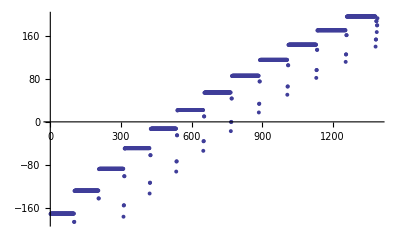

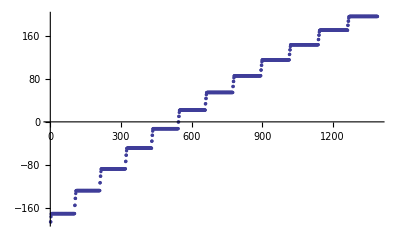

```mathematica
(*Find minimal Energydistance of found levels to initial levels*)

Clear[EDiff]
EDiff={};
For[i=1,i≤Length[NList],i++,EDiff=Join[EDiff,{(NList[[i,5]]-Subscript[E, 12])/10^9}]];
ListPlot[EDiff, PlotRange->{All,All},PlotStyle->PointSize[0.007]]
ListPlot[EDiff[[Ordering[EDiff]]], PlotRange->{All,All},PlotStyle->PointSize[0.006]]
```

```mathematica
NListTemp=NList[[Ordering[NList[[All,{5}]]]]] ;

(*Ordering NList beginning with highest Energy
LabelList is organized by energy also; it's an index for the NListTemp *)

LabelList={};
For[i=1,i≤Length[NList],i++,LabelList=Join[LabelList,{NListTemp[[i,1]]|NListTemp[[i,2]]|NListTemp[[i,3]]|NListTemp[[i,4]]}]]

(*Make List of Hilbert Space Basis level names for Plot of Energies*)

NList ;
LabelList

Clear[n,l,m,j,mj,np,lp,mp,jp,mjp,lj,ljp,Ξ,Ω,Ex,Ey,Ez,EField]
Clear[I0,E0,EFieldpi,EFieldsp,EFieldsm]

(*Calculation of r-Vector-Matrixelement <n,l,j,m|{x,y,z}|np,lp,jp,mp>(Vector) = RDip*ADip(Vector) for Angular and Radial Part (in atomic unit [Subscript[a, 0]]), ADip is a 3x1 Vector! *)
ADip[{n_,l_,j_,m_},{np_,lp_,jp_,mp_}]:=(√2)/2*(-1.)^(jp+l-1/2)*√(2.*jp+1)*SixJSymbol[{lp,1/2,jp},{j,1,l}]*(-1)^l*√((2*l+1)*(2*lp+1))*ThreeJSymbol[{l,0},{1,0},{lp,0}]*{ClebschGordan[{jp,mp},{1,-1},{j,m}]-ClebschGordan[{jp,mp},{1,1},{j,m}],I*ClebschGordan[{jp,mp},{1,-1},{j,m}]+I*ClebschGordan[{jp,mp},{1,1},{j,m}],√2*ClebschGordan[{jp,mp},{1,0},{j,m}]};
RDip[{n_,l_,lj_},{np_,lp_,ljp_}]:=RadIntE[ERadinte[lj,n],ERadinte[ljp,np],l,lp,1];

(*  Definition of Matrix Element Subscript[H, dipole]= RDip*ADip(Vector)(*.EField*) in unit [Subscript[a, 0]*Subscript[e, SI](*V/m*)]  *)
EMatrixelement[{n_,l_,j_,m_},{np_,lp_,jp_,mp_}]:=RDip[{n,l,Chooselj[l,j]},{np,lp,Chooselj[lp,jp]}]*ADip[{n,l,j,m},{np,lp,jp,mp}](*.EField*);




(*Fill up Matrix VMatrix with Sandwiched Efield Interaction <A|E*d|A'>*)
Clear[AI]
EMatrix=Array[E,{Length[NList],Length[NList]}];
EMatrix[[1,1]]
Timing[For[i=1,i≤Length[NList],i++,
		For[k=1,k≤Length[NList],k++,
If[((Abs[NList[[i,4]]-NList[[k,4]]]==1 ∨ Abs[NList[[i,4]]-NList[[k,4]]]==0))∧(Abs[NList[[i,2]]-NList[[k,2]]]==1),EMatrix[[i,k]]=EMatrixelement[{NList[[i,1]],NList[[i,2]],NList[[i,3]],NList[[i,4]]},{NList[[k,1]],NList[[k,2]],NList[[k,3]],NList[[k,4]]}],EMatrix[[i,k]]={0,0,0}] (*If m and l-parity*)
] 
] 
]
Clear[i,k,AI]

EMatrix[[1,1]]
```

{54|2|3/2|-1/2,54|2|5/2|-1/2,56|0|1/2|-1/2,53|3|7/2|-1/2,53|3|5/2|-1/2,53|4|7/2|-1/2,53|4|9/2|-1/2,53|5|9/2|-1/2,53|5|11/2|-1/2,53|6|11/2|-1/2,53|6|13/2|-1/2,53|7|13/2|-1/2,53|7|15/2|-1/2,53|8|15/2|-1/2,53|8|17/2|-1/2,53|9|17/2|-1/2,53|9|19/2|-1/2,53|10|19/2|-1/2,53|10|21/2|-1/2,53|11|21/2|-1/2,53|11|23/2|-1/2,53|12|23/2|-1/2,53|12|25/2|-1/2,53|13|25/2|-1/2,53|13|27/2|-1/2,53|14|27/2|-1/2,53|14|29/2|-1/2,53|15|29/2|-1/2,53|15|31/2|-1/2,53|16|31/2|-1/2,53|16|33/2|-1/2,53|17|33/2|-1/2,53|17|35/2|-1/2,«1324»,64|47|95/2|-1/2,64|48|95/2|-1/2,64|48|97/2|-1/2,64|49|97/2|-1/2,64|49|99/2|-1/2,64|50|99/2|-1/2,64|50|101/2|-1/2,64|51|101/2|-1/2,64|51|103/2|-1/2,64|52|103/2|-1/2,64|52|105/2|-1/2,64|53|105/2|-1/2,64|53|107/2|-1/2,64|54|107/2|-1/2,64|54|109/2|-1/2,64|55|109/2|-1/2,64|55|111/2|-1/2,64|56|111/2|-1/2,64|56|113/2|-1/2,64|57|113/2|-1/2,64|57|115/2|-1/2,64|58|115/2|-1/2,64|58|117/2|-1/2,64|59|117/2|-1/2,64|59|119/2|-1/2,64|60|119/2|-1/2,64|60|121/2|-1/2,64|61|121/2|-1/2,64|61|123/2|-1/2,64|62|123/2|-1/2,64|62|125/2|-1/2,64|63|125/2|-1/2,64|63|127/2|-1/2}

ⅇ[1,1]

ClebschGordan::phy: ThreeJSymbol[{7/2, -1/2}, {1, -1}, {5/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{7/2, -1/2}, {1, 1}, {5/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{7/2, -1/2}, {1, -1}, {5/2, 1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{4, 1/2, 9/2}, {5/2, 1, 3}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, -1/2}, {1, -1}, {5/2, 1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, -1/2}, {1, 1}, {5/2, 1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, -1/2}, {1, -1}, {5/2, 1/2}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{4, 1/2, 9/2}, {5/2, 1, 3}] is not triangular.

General::stop: Further output of SixJSymbol :: tri will be suppressed during this calculation.

{265.748,Null}

{0,0,0}

```mathematica
Subscript[e, SI]*Subscript[a, 0]/h/10^9
Max[EMatrix]
Max[EMatrix]*Subscript[e, SI]*Subscript[a, 0]/h/10^9

EMatrixelement[{60,1,3/2,-1/2},{56,2,3/2,-1/2}]
EMatrixelement[{60,1,3/2,-1/2},{57,2,3/2,-1/2}]
EMatrixelement[{60,1,3/2,-1/2},{58,2,3/2,-1/2}]
EMatrixelement[{60,1,3/2,-1/2},{59,2,3/2,-1/2}]
EMatrixelement[{60,1,3/2,-1/2},{60,2,3/2,-1/2}]
EMatrixelement[{60,1,3/2,-1/2},{61,2,3/2,-1/2}]
EMatrixelement[{60,1,3/2,-1/2},{62,2,3/2,-1/2}]
EMatrixelement[{60,1,3/2,-1/2},{63,2,3/2,-1/2}]
EMatrixelement[{60,1,3/2,-1/2},{64,2,3/2,-1/2}]



EMatrixelement[{60,1,3/2,-1/2},{48,2,3/2,-1/2}]
EMatrixelement[{60,1,3/2,-1/2},{72,2,3/2,-1/2}]

EMatrixelement[{60,1,3/2,-1/2},{48,2,5/2,-1/2}]
EMatrixelement[{60,1,3/2,-1/2},{72,2,5/2,-1/2}]

EMatrixelement[{60,2,3/2,-1/2},{48,3,5/2,-1/2}]
EMatrixelement[{60,2,3/2,-1/2},{72,3,5/2,-1/2}]
```

0.0000127954

3049.5

0.0390197

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, 1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{0.,0.,16.8449}

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, 1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{0.,0.,-37.0171}

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, 1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{0.,0.,166.282}

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, 1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{0.,0.,301.086}

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, 1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{0.,0.,-2.47158}

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, 1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{0.,0.,-0.892444}

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, 1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{0.,0.,0.984553}

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, 1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{0.,0.,-0.836015}

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, 1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{0.,0.,0.69239}

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, 1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{0.,0.,1.44342}

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, 1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{0.,0.,0.22645}

ClebschGordan::phy: ThreeJSymbol[{5/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{5/2, -1/2}, {1, 1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{5/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{0.,0.,10.5946}

ClebschGordan::phy: ThreeJSymbol[{5/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{5/2, -1/2}, {1, 1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{5/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{0.,0.,1.59835}

ClebschGordan::phy: ThreeJSymbol[{5/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{5/2, -1/2}, {1, 1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{5/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{0.,0.,10.6448}

ClebschGordan::phy: ThreeJSymbol[{5/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{5/2, -1/2}, {1, 1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{5/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{0.,0.,0.607452}

```mathematica
0.0354454654653733214976533
```

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, 1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{0.,0.,16.8449}

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, 1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{0.,0.,-37.0171}

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, 1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{0.,0.,166.282}

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, 1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{0.,0.,301.086}

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, 1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{0.,0.,-2.47158}

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, 1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{0.,0.,-0.892444}

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, 1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{0.,0.,0.984553}

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, 1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{0.,0.,-0.836015}

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, 1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{0.,0.,0.69239}

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, 1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{0.,0.,1.44342}

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, 1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{0.,0.,0.22645}

ClebschGordan::phy: ThreeJSymbol[{5/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{5/2, -1/2}, {1, 1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{5/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{0.,0.,10.5946}

ClebschGordan::phy: ThreeJSymbol[{5/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{5/2, -1/2}, {1, 1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{5/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{0.,0.,1.59835}

ClebschGordan::phy: ThreeJSymbol[{5/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{5/2, -1/2}, {1, 1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{5/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{0.,0.,10.6448}

ClebschGordan::phy: ThreeJSymbol[{5/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{5/2, -1/2}, {1, 1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{5/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{0.,0.,0.607452}

```mathematica
(*Absolute Energies of disturbed levels:*)

Clear[i,f,R]
EI={};
EI
NList;
For[i=1,i≤Length[NList],i++,EI=Join[EI,{NList[[i,5]]} ] ] ;
EIList = {} ;
EI
EIList=EI;
EI;
EI=DiagonalMatrix[EI];
MatrixPlot[EI]
```

{}

{-1.1719×10^12,-1.1719×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.1867×10^12,-1.18662×10^12,-1.12889×10^12,-1.12889×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.14287×10^12,-1.1428×10^12,-1.0882×10^12,-1.0882×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.17699×10^12,-1.15607×10^12,-1.1555×10^12,-1.10143×10^12,-1.10137×10^12,-1.04967×10^12,-1.04967×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.1337×10^12,-1.11392×10^12,-1.11338×10^12,-1.06221×10^12,-1.06214×10^12,-1.01315×10^12,-1.01315×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.09275×10^12,-1.07403×10^12,-1.07351×10^12,-1.02504×10^12,-1.02498×10^12,-9.78506×10^11,-9.78506×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-1.05398×10^12,-1.03624×10^12,-1.03576×10^12,-9.89787×10^11,-9.89731×10^11,-9.45608×10^11,-9.45609×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-1.01724×10^12,-1.00042×10^12,-9.99955×10^11,-9.56324×10^11,-9.56271×10^11,-9.14342×10^11,-9.14343×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.82389×10^11,-9.66416×10^11,-9.65979×10^11,-9.2453×10^11,-9.24479×10^11,-8.84601×10^11,-8.84602×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-9.49297×10^11,-9.34121×10^11,-9.33706×10^11,-8.94295×10^11,-8.94247×10^11,-8.56288×10^11,-8.56289×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-9.17849×10^11,-9.03418×10^11,-9.03023×10^11,-8.65519×10^11,-8.65473×10^11,-8.29313×10^11,-8.29314×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.87938×10^11,-8.74204×10^11,-8.73828×10^11,-8.3811×10^11,-8.38067×10^11,-8.03593×10^11,-8.03594×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.03179×10^11,-8.59466×10^11,-8.46385×10^11,-8.46027×10^11,-8.11983×10^11,-8.11942×10^11,-8.32342×10^11,-8.19873×10^11,-8.19532×10^11,-8.06482×10^11}

-Graphics-

```mathematica
EField={0,0,1} ;
MatrixPlot[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]
MatrixPlot[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]
Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]
```

-Graphics-

-Graphics-

{-1186.7,-1186.62,-1176.99,-1171.9,-1171.9,-1171.22,-1171.22,-1171.22,-1171.22,-1171.22,-1171.22,-1171.22,-1171.22,-1171.21,-1171.21,-1171.21,-1171.21,-1171.21,-1171.21,-1171.21,-1171.21,-1171.21,-1171.21,-1171.2,-1171.2,-1171.2,-1171.2,-1171.2,-1171.2,-1171.2,-1171.2,-1171.2,-1171.2,-1171.19,-1171.19,-1171.19,-1171.19,-1171.19,-1171.19,-1171.19,-1171.19,-1171.18,-1171.18,-1171.18,-1171.18,-1171.18,-1171.18,-1171.18,-1171.18,-1171.18,-1171.18,-1171.17,-1171.17,-1171.17,-1171.17,-1171.17,-1171.17,-1171.17,-1171.17,-1171.17,-1171.17,-1171.16,-1171.16,-1171.16,-1171.16,-1171.16,-1171.16,-1171.16,-1171.16,-1171.15,-1171.15,-1171.15,-1171.15,-1171.15,-1171.15,-1171.15,-1171.15,-1171.15,-1171.15,-1171.14,-1171.14,-1171.14,-1171.14,-1171.14,-1171.14,-1171.14,-1171.14,-1171.14,-1171.14,-1171.13,-1171.13,-1171.13,-1171.13,-1171.13,-1171.13,-1171.13,-1171.13,-1171.12,-1171.12,-1171.12,-1171.12,-1171.12,-1171.12,-1156.07,-1155.5,-1142.87,-1142.8,-1133.7,-1128.89,-1128.89,-1128.25,-1128.25,-1128.25,-1128.25,-1128.25,-1128.25,-1128.24,-1128.24,-1128.24,-1128.24,-1128.24,-1128.24,-1128.24,-1128.24,-1128.23,-1128.23,-1128.23,-1128.23,-1128.23,-1128.23,-1128.23,-1128.23,-1128.23,-1128.23,-1128.22,-1128.22,-1128.22,-1128.22,-1128.22,-1128.22,-1128.22,-1128.22,-1128.21,-1128.21,-1128.21,-1128.21,-1128.21,-1128.21,-1128.21,-1128.21,-1128.21,-1128.21,-1128.2,-1128.2,-1128.2,-1128.2,-1128.2,-1128.2,-1128.2,-1128.2,-1128.2,-1128.2,-1128.19,-1128.19,-1128.19,-1128.19,-1128.19,-1128.19,-1128.19,-1128.19,-1128.18,-1128.18,-1128.18,-1128.18,-1128.18,-1128.18,-1128.18,-1128.18,-1128.18,-1128.18,-1128.17,-1128.17,-1128.17,-1128.17,-1128.17,-1128.17,-1128.17,-1128.17,-1128.17,-1128.17,-1128.16,-1128.16,-1128.16,-1128.16,-1128.16,-1128.16,-1128.16,-1128.16,-1128.15,-1128.15,-1128.15,-1128.15,-1128.15,-1128.15,-1128.15,-1128.15,-1128.15,-1128.15,-1128.14,-1128.14,-1113.92,-1113.38,-1101.43,-1101.37,-1092.75,-1088.2,-1088.2,-1087.6,-1087.6,-1087.6,-1087.6,-1087.6,-1087.6,-1087.59,-1087.59,-1087.59,-1087.59,-1087.59,-1087.59,-1087.59,-1087.59,-1087.58,-1087.58,-1087.58,-1087.58,-1087.58,-1087.58,-1087.58,-1087.58,-1087.58,-1087.58,-1087.57,-1087.57,-1087.57,-1087.57,-1087.57,-1087.57,-1087.57,-1087.57,-1087.56,-1087.56,-1087.56,-1087.56,-1087.56,-1087.56,-1087.56,-1087.56,-1087.56,-1087.56,-1087.55,-1087.55,-1087.55,-1087.55,-1087.55,-1087.55,-1087.55,-1087.55,-1087.54,-1087.54,-1087.54,-1087.54,-1087.54,-1087.54,-1087.54,-1087.54,-1087.54,-1087.54,-1087.53,-1087.53,-1087.53,-1087.53,-1087.53,-1087.53,-1087.53,-1087.53,-1087.52,-1087.52,-1087.52,-1087.52,-1087.52,-1087.52,-1087.52,-1087.52,-1087.52,-1087.52,-1087.51,-1087.51,-1087.51,-1087.51,-1087.51,-1087.51,-1087.51,-1087.51,-1087.5,-1087.5,-1087.5,-1087.5,-1087.5,-1087.5,-1087.5,-1087.5,-1087.5,-1087.5,-1087.49,-1087.49,-1087.49,-1087.49,-1087.49,-1087.49,-1074.03,-1073.51,-1062.21,-1062.14,-1053.98,-1049.67,-1049.67,-1049.11,-1049.11,-1049.11,-1049.11,-1049.1,-1049.1,-1049.1,-1049.1,-1049.1,-1049.1,-1049.1,-1049.1,-1049.09,-1049.09,-1049.09,-1049.09,-1049.09,-1049.09,-1049.09,-1049.09,-1049.08,-1049.08,-1049.08,-1049.08,-1049.08,-1049.08,-1049.08,-1049.08,-1049.08,-1049.08,-1049.07,-1049.07,-1049.07,-1049.07,-1049.07,-1049.07,-1049.07,-1049.07,-1049.06,-1049.06,-1049.06,-1049.06,-1049.06,-1049.06,-1049.06,-1049.06,-1049.06,-1049.06,-1049.05,-1049.05,-1049.05,-1049.05,-1049.05,-1049.05,-1049.05,-1049.05,-1049.04,-1049.04,-1049.04,-1049.04,-1049.04,-1049.04,-1049.04,-1049.04,-1049.04,-1049.04,-1049.03,-1049.03,-1049.03,-1049.03,-1049.03,-1049.03,-1049.03,-1049.03,-1049.02,-1049.02,-1049.02,-1049.02,-1049.02,-1049.02,-1049.02,-1049.02,-1049.02,-1049.02,-1049.01,-1049.01,-1049.01,-1049.01,-1049.01,-1049.01,-1049.01,-1049.01,-1049.,-1049.,-1049.,-1049.,-1049.,-1049.,-1049.,-1049.,-1048.99,-1048.99,-1048.99,-1048.99,-1036.24,-1035.76,-1025.04,-1024.98,-1017.24,-1013.15,-1013.15,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.6,-1012.6,-1012.6,-1012.6,-1012.6,-1012.6,-1012.6,-1012.6,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.5,-1012.5,-1000.42,-999.955,-989.787,-989.731,-982.389,-978.508,-978.507,-978.012,-978.011,-978.009,-978.009,-978.007,-978.006,-978.004,-978.004,-978.002,-978.002,-977.999,-977.999,-977.997,-977.997,-977.995,-977.994,-977.992,-977.992,-977.99,-977.99,-977.988,-977.987,-977.985,-977.985,-977.983,-977.983,-977.981,-977.98,-977.978,-977.978,-977.976,-977.976,-977.974,-977.973,-977.971,-977.971,-977.969,-977.969,-977.967,-977.967,-977.964,-977.964,-977.962,-977.962,-977.96,-977.96,-977.957,-977.957,-977.955,-977.955,-977.953,-977.953,-977.95,-977.95,-977.948,-977.948,-977.946,-977.946,-977.943,-977.943,-977.941,-977.941,-977.939,-977.939,-977.936,-977.936,-977.934,-977.934,-977.932,-977.932,-977.93,-977.929,-977.927,-977.927,-977.925,-977.925,-977.923,-977.923,-977.92,-977.92,-977.918,-977.918,-977.916,-977.916,-977.913,-977.913,-977.911,-977.911,-977.909,-977.909,-977.906,-977.906,-977.904,-977.904,-977.902,-977.901,-977.899,-977.899,-977.897,-977.897,-977.894,-977.894,-977.892,-977.892,-977.89,-977.889,-977.887,-977.887,-966.416,-965.979,-956.324,-956.271,-949.297,-945.611,-945.61,-945.144,-945.144,-945.141,-945.141,-945.139,-945.139,-945.136,-945.136,-945.134,-945.134,-945.131,-945.131,-945.129,-945.129,-945.127,-945.127,-945.124,-945.124,-945.122,-945.122,-945.119,-945.119,-945.117,-945.117,-945.115,-945.115,-945.112,-945.112,-945.11,-945.11,-945.108,-945.108,-945.105,-945.105,-945.103,-945.103,-945.101,-945.1,-945.098,-945.098,-945.096,-945.096,-945.093,-945.093,-945.091,-945.091,-945.089,-945.089,-945.086,-945.086,-945.084,-945.084,-945.082,-945.082,-945.079,-945.079,-945.077,-945.077,-945.075,-945.075,-945.072,-945.072,-945.07,-945.07,-945.068,-945.068,-945.065,-945.065,-945.063,-945.063,-945.06,-945.06,-945.058,-945.058,-945.056,-945.056,-945.053,-945.053,-945.051,-945.051,-945.049,-945.049,-945.046,-945.046,-945.044,-945.044,-945.042,-945.042,-945.039,-945.039,-945.037,-945.037,-945.034,-945.034,-945.032,-945.032,-945.03,-945.03,-945.027,-945.027,-945.025,-945.025,-945.023,-945.022,-945.02,-945.02,-945.018,-945.017,-945.015,-945.015,-934.121,-933.706,-924.53,-924.479,-917.849,-914.345,-914.344,-913.906,-913.906,-913.903,-913.903,-913.901,-913.901,-913.898,-913.898,-913.896,-913.896,-913.893,-913.893,-913.891,-913.891,-913.888,-913.888,-913.886,-913.886,-913.884,-913.884,-913.881,-913.881,-913.879,-913.879,-913.876,-913.876,-913.874,-913.874,-913.872,-913.871,-913.869,-913.869,-913.867,-913.867,-913.864,-913.864,-913.862,-913.862,-913.86,-913.859,-913.857,-913.857,-913.855,-913.855,-913.852,-913.852,-913.85,-913.85,-913.848,-913.848,-913.845,-913.845,-913.843,-913.843,-913.84,-913.84,-913.838,-913.838,-913.836,-913.836,-913.833,-913.833,-913.831,-913.831,-913.828,-913.828,-913.826,-913.826,-913.824,-913.824,-913.821,-913.821,-913.819,-913.819,-913.816,-913.816,-913.814,-913.814,-913.812,-913.812,-913.809,-913.809,-913.807,-913.807,-913.804,-913.804,-913.802,-913.802,-913.8,-913.8,-913.797,-913.797,-913.795,-913.795,-913.792,-913.792,-913.79,-913.79,-913.788,-913.787,-913.785,-913.785,-913.783,-913.783,-913.78,-913.78,-913.778,-913.778,-913.775,-913.775,-913.773,-913.772,-903.418,-903.023,-894.295,-894.247,-887.938,-884.605,-884.604,-884.192,-884.192,-884.189,-884.189,-884.187,-884.186,-884.184,-884.184,-884.182,-884.181,-884.179,-884.179,-884.177,-884.176,-884.174,-884.174,-884.172,-884.172,-884.169,-884.169,-884.167,-884.167,-884.164,-884.164,-884.162,-884.162,-884.159,-884.159,-884.157,-884.157,-884.154,-884.154,-884.152,-884.152,-884.15,-884.15,-884.147,-884.147,-884.145,-884.145,-884.142,-884.142,-884.14,-884.14,-884.137,-884.137,-884.135,-884.135,-884.133,-884.133,-884.13,-884.13,-884.128,-884.128,-884.125,-884.125,-884.123,-884.123,-884.12,-884.12,-884.118,-884.118,-884.116,-884.116,-884.113,-884.113,-884.111,-884.111,-884.108,-884.108,-884.106,-884.106,-884.103,-884.103,-884.101,-884.101,-884.099,-884.098,-884.096,-884.096,-884.094,-884.094,-884.091,-884.091,-884.089,-884.089,-884.086,-884.086,-884.084,-884.084,-884.081,-884.081,-884.079,-884.079,-884.077,-884.076,-884.074,-884.074,-884.072,-884.072,-884.069,-884.069,-884.067,-884.067,-884.064,-884.064,-884.062,-884.062,-884.059,-884.059,-884.057,-884.056,-884.054,-884.054,-874.205,-873.828,-865.519,-865.473,-859.466,-856.292,-856.291,-855.904,-855.904,-855.901,-855.901,-855.899,-855.899,-855.896,-855.896,-855.894,-855.894,-855.891,-855.891,-855.889,-855.888,-855.886,-855.886,-855.884,-855.883,-855.881,-855.881,-855.879,-855.878,-855.876,-855.876,-855.874,-855.874,-855.871,-855.871,-855.869,-855.869,-855.866,-855.866,-855.864,-855.864,-855.861,-855.861,-855.859,-855.859,-855.856,-855.856,-855.854,-855.854,-855.851,-855.851,-855.849,-855.849,-855.846,-855.846,-855.844,-855.844,-855.841,-855.841,-855.839,-855.839,-855.836,-855.836,-855.834,-855.834,-855.831,-855.831,-855.829,-855.829,-855.827,-855.827,-855.824,-855.824,-855.822,-855.822,-855.819,-855.819,-855.817,-855.817,-855.814,-855.814,-855.812,-855.812,-855.809,-855.809,-855.807,-855.807,-855.804,-855.804,-855.802,-855.802,-855.799,-855.799,-855.797,-855.797,-855.794,-855.794,-855.792,-855.792,-855.789,-855.789,-855.787,-855.787,-855.784,-855.784,-855.782,-855.782,-855.78,-855.779,-855.777,-855.777,-855.774,-855.774,-855.772,-855.772,-855.769,-855.769,-855.767,-855.767,-855.764,-855.764,-855.762,-855.761,-846.385,-846.027,-838.11,-838.067,-832.342,-829.317,-829.317,-828.953,-828.952,-828.95,-828.95,-828.947,-828.947,-828.945,-828.945,-828.942,-828.942,-828.94,-828.939,-828.937,-828.937,-828.934,-828.934,-828.932,-828.932,-828.929,-828.929,-828.927,-828.927,-828.924,-828.924,-828.922,-828.922,-828.919,-828.919,-828.917,-828.917,-828.914,-828.914,-828.912,-828.912,-828.909,-828.909,-828.907,-828.907,-828.904,-828.904,-828.902,-828.902,-828.899,-828.899,-828.897,-828.897,-828.894,-828.894,-828.892,-828.892,-828.889,-828.889,-828.887,-828.887,-828.884,-828.884,-828.882,-828.882,-828.879,-828.879,-828.877,-828.877,-828.874,-828.874,-828.872,-828.872,-828.869,-828.869,-828.867,-828.866,-828.864,-828.864,-828.862,-828.861,-828.859,-828.859,-828.856,-828.856,-828.854,-828.854,-828.851,-828.851,-828.849,-828.849,-828.846,-828.846,-828.844,-828.844,-828.841,-828.841,-828.839,-828.839,-828.836,-828.836,-828.834,-828.834,-828.831,-828.831,-828.829,-828.829,-828.826,-828.826,-828.824,-828.824,-828.821,-828.821,-828.819,-828.819,-828.816,-828.816,-828.814,-828.813,-828.811,-828.811,-828.808,-828.808,-828.806,-828.805,-819.873,-819.532,-811.983,-811.942,-806.482,-803.597,-803.597,-803.255,-803.255,-803.252,-803.252,-803.25,-803.249,-803.247,-803.247,-803.244,-803.244,-803.242,-803.242,-803.239,-803.239,-803.236,-803.236,-803.234,-803.234,-803.231,-803.231,-803.229,-803.229,-803.226,-803.226,-803.224,-803.224,-803.221,-803.221,-803.218,-803.218,-803.216,-803.216,-803.213,-803.213,-803.211,-803.211,-803.208,-803.208,-803.206,-803.206,-803.203,-803.203,-803.201,-803.201,-803.198,-803.198,-803.195,-803.195,-803.193,-803.193,-803.19,-803.19,-803.188,-803.188,-803.185,-803.185,-803.183,-803.183,-803.18,-803.18,-803.178,-803.178,-803.175,-803.175,-803.173,-803.173,-803.17,-803.17,-803.167,-803.167,-803.165,-803.165,-803.162,-803.162,-803.16,-803.16,-803.157,-803.157,-803.155,-803.155,-803.152,-803.152,-803.15,-803.15,-803.147,-803.147,-803.145,-803.144,-803.142,-803.142,-803.139,-803.139,-803.137,-803.137,-803.134,-803.134,-803.132,-803.132,-803.129,-803.129,-803.127,-803.127,-803.124,-803.124,-803.122,-803.121,-803.119,-803.119,-803.116,-803.116,-803.114,-803.114,-803.111,-803.111,-803.109,-803.108,-803.106,-803.106,-803.103,-803.103}

```mathematica
(*MultiListPlot: Generate Plot of Energies as a Function of EField*)
Clear[i,k,L,MPList,R]
MPList=Array[L,{Length[NList],2}];
Temp={};
EMIN=0;
EMAX=301;
ELabel=300;
(*Electric Field in [V/m], Efield perpend. to BEC, so E={Ex,0,Ez=0}, parasitic Fields typ. 1V/cm, Const. Field typ. 5V/cm*)
(*Subscript[EStark, 12]=2*EMatrixelement[{44,0,1/2,1/2},{44,0,1/2,1/2}]*Subscript[e, SI]*Subscript[a, 0]*)(*Calculate shift of 44s44s-44s44s for R->∞ for Offset substraction in Plot, [J]*)

E0=EMIN;
EStep=1;

For[i=1,i≤Length[NList],i++,MPList[[i]]={}];
Clear[i];
While[E0<EMAX,E0=E0+EStep;EField={0,0,E0};Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]-Subscript[E, 12]/10^9;For[i=1,i≤Length[NList],i++,MPList[[i]]=Join[MPList[[i]],{{E0,Temp[[i]]}}]  ]] ;
E0=EMIN;

Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.{0,0,ELabel}/h/10^9]-Subscript[E, 12]/10^9;(*Generate Labels for Levels*)
TempList=Array[T,Length[NList]];
For[i=1,i≤Length[NList],i++,TempList[[i]]={ELabel,Temp[[i]],LabelList[[i]]} ];
TempList

ListPlot[MPList]

Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-100,100}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

{{300,-191.125,54|2|3/2|-1/2},{300,-190.564,54|2|5/2|-1/2},{300,-187.082,56|0|1/2|-1/2},{300,-186.995,53|3|7/2|-1/2},{300,-186.393,53|3|5/2|-1/2},{300,-186.329,53|4|7/2|-1/2},{300,-185.729,53|4|9/2|-1/2},{300,-185.676,53|5|9/2|-1/2},{300,-185.077,53|5|11/2|-1/2},{300,-185.031,53|6|11/2|-1/2},{300,-184.431,53|6|13/2|-1/2},«1368»,{300,216.819,64|58|117/2|-1/2},{300,217.489,64|59|117/2|-1/2},{300,217.577,64|59|119/2|-1/2},{300,218.244,64|60|119/2|-1/2},{300,218.339,64|60|121/2|-1/2},{300,219.,64|61|121/2|-1/2},{300,219.106,64|61|123/2|-1/2},{300,219.759,64|62|123/2|-1/2},{300,219.882,64|62|125/2|-1/2},{300,220.523,64|63|125/2|-1/2},{300,220.675,64|63|127/2|-1/2}}

-Graphics-

-Graphics-

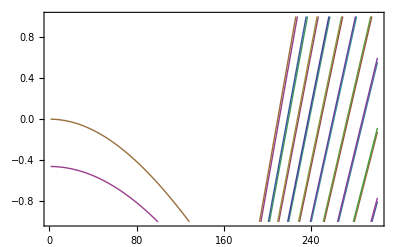

```mathematica
Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-1,1}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

```mathematica
LabelList[[545]]

MPList[[545]]
```

60|1|3/2|-1/2

{{1,-0.0000676513},{2,-0.000270599},{3,-0.000608825},{4,-0.0010823},{5,-0.00169097},{6,-0.0024348},{7,-0.0033137},{8,-0.0043276},{9,-0.00547641},{10,-0.00676002},{11,-0.00817831},{12,-0.00973115},{13,-0.0114184},{14,-0.0132399},{15,-0.0151955},{16,-0.0172851},{17,-0.0195083},{18,-0.0218651},{19,-0.0243552},{20,-0.0269784},{21,-0.0297344},{22,-0.032623},{23,-0.035644},{24,-0.038797},{25,-0.0420819},{26,-0.0454982},{27,-0.0490457},{28,-0.0527241},{29,-0.0565331},{30,-0.0604723},{31,-0.0645413},{32,-0.0687399},{33,-0.0730676},{34,-0.0775241},{35,-0.082109},{36,-0.0868218},{37,-0.0916623},{38,-0.0966299},{39,-0.101724},{40,-0.106945},{41,-0.112291},{42,-0.117763},{43,-0.12336},{44,-0.129082},{45,-0.134927},{46,-0.140896},{47,-0.146988},{48,-0.153202},{49,-0.159539},{50,-0.165997},{51,-0.172575},{52,-0.179275},{53,-0.186094},{54,-0.193033},{55,-0.20009},{56,-0.207266},{57,-0.214559},{58,-0.22197},{59,-0.229497},{60,-0.23714},{61,-0.244898},{62,-0.252771},{63,-0.260758},{64,-0.268859},{65,-0.277073},{66,-0.285399},{67,-0.293837},{68,-0.302387},{69,-0.311046},{70,-0.319816},{71,-0.328695},{72,-0.337682},{73,-0.346778},{74,-0.355981},{75,-0.36529},{76,-0.374706},{77,-0.384227},{78,-0.393853},{79,-0.403583},{80,-0.413417},{81,-0.423353},{82,-0.433392},{83,-0.443532},{84,-0.453773},{85,-0.464115},{86,-0.474556},{87,-0.485096},{88,-0.495734},{89,-0.50647},{90,-0.517303},{91,-0.528232},{92,-0.539257},{93,-0.550377},{94,-0.561592},{95,-0.5729},{96,-0.584301},{97,-0.595795},{98,-0.607381},{99,-0.619058},{100,-0.630825},{101,-0.642682},{102,-0.654629},{103,-0.666664},{104,-0.678787},{105,-0.690997},{106,-0.703294},{107,-0.715678},{108,-0.728146},{109,-0.7407},{110,-0.753338},{111,-0.766059},{112,-0.778864},{113,-0.791751},{114,-0.80472},{115,-0.817769},{116,-0.8309},{117,-0.84411},{118,-0.8574},{119,-0.870769},{120,-0.884215},{121,-0.89774},{122,-0.911341},{123,-0.925018},{124,-0.938772},{125,-0.9526},{126,-0.966503},{127,-0.98048},{128,-0.994531},{129,-1.00865},{130,-1.02285},{131,-1.03712},{132,-1.05145},{133,-1.06586},{134,-1.08034},{135,-1.09489},{136,-1.1095},{137,-1.12419},{138,-1.13894},{139,-1.15375},{140,-1.16864},{141,-1.18359},{142,-1.1986},{143,-1.21367},{144,-1.22881},{145,-1.24402},{146,-1.25928},{147,-1.2746},{148,-1.28999},{149,-1.30543},{150,-1.32093},{151,-1.33649},{152,-1.3521},{153,-1.36777},{154,-1.3835},{155,-1.39927},{156,-1.4151},{157,-1.43098},{158,-1.4469},{159,-1.46288},{160,-1.47889},{161,-1.49495},{162,-1.51105},{163,-1.52719},{164,-1.54336},{165,-1.55956},{166,-1.57578},{167,-1.59203},{168,-1.60829},{169,-1.62455},{170,-1.6408},{171,-1.65704},{172,-1.67323},{173,-1.68934},{174,-1.70533},{175,-1.72111},{176,-1.73652},{177,-1.75121},{178,-1.76415},{179,-1.77083},{180,-1.75026},{181,-1.69982},{182,-1.64273},{183,-1.58409},{184,-1.52487},{185,-1.46536},{186,-1.4057},{187,-1.34593},{188,-1.28609},{189,-1.22621},{190,-1.16629},{191,-1.10634},{192,-1.04638},{193,-0.986404},{194,-0.926415},{195,-0.866417},{196,-0.806411},{197,-0.746399},{198,-0.686383},{199,-0.626363},{200,-0.566341},{201,-0.506316},{202,-0.446289},{203,-0.386261},{204,-0.326233},{205,-0.266204},{206,-0.206175},{207,-0.146146},{208,-0.0861171},{209,-0.0260889},{210,0.0339386},{211,0.0939652},{212,0.153991},{213,0.214015},{214,0.274039},{215,0.334061},{216,0.394081},{217,0.4541},{218,0.514118},{219,0.574133},{220,0.634147},{221,0.694159},{222,0.754169},{223,0.814177},{224,0.874183},{225,0.934187},{226,0.994189},{227,1.05419},{228,1.11419},{229,1.17418},{230,1.23417},{231,1.29416},{232,1.35415},{233,1.41414},{234,1.47412},{235,1.5341},{236,1.59407},{237,1.65405},{238,1.71402},{239,1.77399},{240,1.83395},{241,1.89391},{242,1.95387},{243,2.01383},{244,2.07378},{245,2.13373},{246,2.19367},{247,2.25362},{248,2.31355},{249,2.37349},{250,2.43342},{251,2.49334},{252,2.55326},{253,2.61318},{254,2.67309},{255,2.733},{256,2.7929},{257,2.8528},{258,2.91269},{259,2.97258},{260,3.03246},{261,3.09233},{262,3.1522},{263,3.21206},{264,3.27191},{265,3.33176},{266,3.39159},{267,3.45142},{268,3.51123},{269,3.57103},{270,3.63082},{271,3.6906},{272,3.75035},{273,3.81008},{274,3.86979},{275,3.92946},{276,3.98908},{277,4.04863},{278,4.10805},{279,4.16723},{280,4.22568},{281,4.27905},{282,4.26328},{283,4.29569},{284,4.26077},{285,4.19973},{286,4.1381},{287,4.07658},{288,4.01626},{289,4.06795},{290,4.12358},{291,4.17889},{292,4.23169},{293,4.26002},{294,4.26103},{295,4.24913},{296,4.19365},{297,4.13554},{298,4.07719},{299,4.0196},{300,3.99808},{301,4.04876}}

```mathematica
(*MPListExport: Generate list to be read by Origin *)

Efieldlist = {};

E0=EMIN;


While[E0<EMAX,E0=E0+EStep;Efieldlist=Join[Efieldlist,{E0}]] ;
E0=EMIN;

Efieldlist


Clear[i,k,L,MPListExport,R]
NE0=(EMAX-EMIN)/EStep;
MPListExport=Array[0,{Length[NList],NE0}];
(*Electric Field in [V/m], Efield perpend. to BEC, so E={Ex,0,Ez=0}, parasitic Fields typ. 1V/cm, Const. Field typ. 5V/cm*)
(*Subscript[EStark, 12]=2*EMatrixelement[{44,0,1/2,1/2},{44,0,1/2,1/2}]*Subscript[e, SI]*Subscript[a, 0]*)(*Calculate shift of 44s44s-44s44s for R->∞ for Offset substraction in Plot, [J]*)



Clear[i];
j=0;
While[j<NE0,
j++;
For[i=1,i≤Length[NList],i++,
MPListExport[[i,j]]=MPList[[i,j,2]] 
 ]
] ;

MPListExport


(*
Export["Stark_Shifts_around_60s.dat",MPListExport]
Export["Electric_fields_for_Stark_Shifts_around_60s.dat",Efieldlist]
*)
Export["60p_j3_2_mj-1_2_stark_Shift-200GHz.dat",MPList[[545]]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301}

{«1»}

60p_j3_2_mj-1_2_stark_Shift-200GHz.dat

## Old data

```mathematica
Export[FileNameJoin[{Directory[],"Starkbase3.dat"}],TempList]
```

C:\Documents and Settings\R14\Mes documents\Starkbase3.dat

-Graphics-

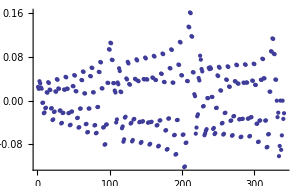

-0.0160281

-3.39745

{-72.2181,-66.8629,-62.1743,-61.9304,-61.0162,-60.796,-59.8912,-59.6823,-58.7823,-58.5808,-57.6836,-57.4878,-56.5921,-56.4014,-55.5061,-55.3205,-54.4245,-54.2442,-53.3464,-53.1721,-52.2711,-52.1037,-51.1979,-51.0385,-50.1264,-49.9762,-49.0562,-48.9161,-47.9868,-47.8576,-46.918,-46.8002,-45.8496,-45.7431,-44.7822,-44.6857,-43.7193,-43.6279,-42.7485,-42.5742,-42.468,-41.5433,-41.5007,-40.4774,-40.4383,-39.4051,-39.3725,-38.3302,-38.3041,-37.2535,-37.2332,-36.1751,-36.1599,-35.0955,-35.0842,-34.0149,-34.0059,-32.9342,-32.9248,-31.8536,-31.8414,-30.7739,-30.7565,-29.7012,-29.6709,-28.7635,-28.5863,-28.4451,-27.5145,-27.4773,-26.9365,-26.4001,-26.369,-25.5526,-25.5234,-25.3135,-25.2867,-24.3821,-24.3593,-24.2238,-24.2002,-23.2398,-23.2249,-23.1301,-23.1082,-22.1152,-22.107,-22.0299,-22.0086,-21.0046,-21.0014,-20.9218,-20.901,-19.904,-19.9026,-19.8082,-19.7879,-18.8094,-18.8054,-18.6929,-18.6723,-17.7163,-17.7094,-17.5775,-17.5556,-16.6232,-16.6135,-16.4626,-16.4385,-15.5298,-15.5173,-15.3482,-15.321,-14.4357,-14.4205,-14.2342,-14.203,-13.341,-13.3228,-13.1205,-13.0844,-12.2455,-12.2241,-12.0067,-11.9648,-11.1494,-11.1244,-10.8928,-10.8439,-10.0533,-10.0236,-9.77823,-9.72126,-8.958,-8.92151,-8.66275,-8.59616,-7.86658,-7.81817,-7.54566,-7.4678,-6.78973,-6.7136,-6.42593,-6.33655,-5.79359,-5.60798,-5.30168,-5.25631,-5.07862,-4.50187,-4.3888,-4.16823,-3.9819,-3.39745,-3.33767,-2.32451,-2.28271,-1.24121,-1.20881,-0.152056,-0.12512,0.94199,0.965646,2.04036,2.06207,3.14252,3.16317,4.24793,4.26811,5.35603,5.37615,6.46626,6.48662,7.40325,7.57815,7.59892,8.69106,8.71212,9.38115,9.79969,9.82872,9.86972,10.4722,10.9152,10.9447,11.0655,11.5098,12.0303,12.0585,12.236,12.5344,13.146,13.1704,13.3946,13.5811,14.2623,14.2818,14.5462,14.6583,15.3792,15.394,15.6931,15.7576,16.4968,16.5073,16.8365,16.8697,17.6149,17.6218,17.977,17.9887,18.7335,18.7374,19.1108,19.1154,19.852,19.8548,20.2346,20.2511,20.9697,20.9743,21.3583,21.3848,22.0875,22.0952,22.4813,22.5164,23.2055,23.2171,23.603,23.6458,24.3237,24.3401,24.7231,24.773,25.4418,25.4642,25.8414,25.8981,26.5592,26.5897,26.9582,27.0208,27.6753,27.7168,28.0737,28.1411,28.7888,28.8457,29.1889,29.2589,29.8981,29.9769,30.3055,30.3739,31.0009,31.1108,31.4263,31.4859,32.0949,32.2483,32.5557,32.5942,33.1784,33.391,33.6952,33.7037,34.2512,34.5422,34.7913,34.8831,35.3156,35.7133,36.3702,36.7745,37.396,37.8525,38.3745,38.9405,39.3197,40.0357,40.2888,41.1363,41.3108,42.2406,42.3731,43.3473,43.4588,44.4553,44.558,45.5635,45.665,46.6706,46.7771,47.7751,47.8926,48.8745,49.0103,49.9641,50.1297,51.0352,51.2503,52.0705,52.3718,53.0481,53.4936,53.9823,54.6157,54.9448,55.7374,55.9689,56.8581,57.0365,57.977,58.128,59.0922,59.2329,60.2003,60.3461,61.2942,61.4648,62.3583,62.5877,63.3624,63.7139,64.2934,64.8432,65.2335,65.9754,66.2538,67.1106,67.3352,68.2491,68.4506,69.3915,69.588,70.539,70.7458,71.6937,71.9352}

0.

```mathematica
(*Admixture of 60s1/2 at 500V/m*)
EField={0,0,500};MatrixPlot[Eigenvectors[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]]
ListPlot[Eigenvectors[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[116]]]
Eigenvectors[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[152,152]]
EField={0,0,500};Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[152]]-Subscript[E, 12]/10^9
EField={0,0,500};Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]-Subscript[E, 12]/10^9
EField={0,0,0};Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[116]]-Subscript[E, 12]/10^9
```

-Graphics-

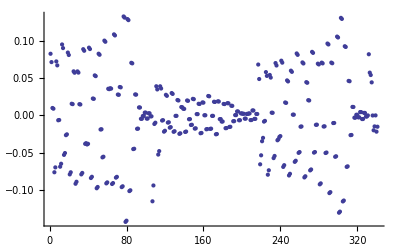

0.0478166

-13.5686

-7.79615

```mathematica
(*Admixture of 58d3/2 at 300V/m*)
EField={0,0,300};MatrixPlot[Eigenvectors[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]]
ListPlot[Eigenvectors[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[114]]]
Eigenvectors[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[114,114]]
EField={0,0,300};Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[114]]-Subscript[E, 12]/10^9
EField={0,0,0};Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[114]]-Subscript[E, 12]/10^9
```

```mathematica
(*Export data for Origin*)
Clear[i,k,L,MPList,R]
MPList=Array[L,{Length[NList],2}];
Temp={};
EMIN=0;
EMAX=500;


E0=EMIN;
EStep=0.1;

TempList=Array[T,Length[NList]];
For[i=1,i≤Length[NList],i++,TempList[[i]]={i,LabelList[[i]]} ]

Clear[i,k,L,MPList,R]
E0=EMIN;;
MPList={};
MPList=Join[MPList,{Join[{E0},Array[#&,Length[NList]]] }];
MPList=Join[MPList,{Join[{E0},LabelList] }];
While[E0<EMAX,E0=E0+EStep;EField={0,0,E0};Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]-Subscript[E, 12]/10^9;MPList=Join[MPList,{Join[{E0},Temp] }] ] 
Export[FileNameJoin[{Directory[],"Starkshift3.dat"}],MPList]
Export[FileNameJoin[{Directory[],"Starkbase3.dat"}],TempList]
```

C:\Documents and Settings\R14\Mes documents\Starkshift3.dat

C:\Documents and Settings\R14\Mes documents\Starkbase3.dat

```mathematica
⁃Graphics⁃⁃Graphics⁃ n=15 -18, ninitial=15, Subscript[m, j]=1/2
```

⁃Graphics⁃

⁃Graphics⁃

⁃Graphics⁃

```mathematica
⁃Graphics⁃ n=15-17 , Subscript[m, j]=5/2, n initial=15.
```

⁃Graphics⁃

⁃Graphics⁃

```mathematica
⁃Graphics⁃Shift of 44s44s [GHz]  at R=∞, E  in  V/m, 212  level, n=42 to 46, all M, l=s,p, EField =(0,0,E0)
```

```mathematica
⁃Graphics⁃Shift of 44s44s [GHz]  at R=∞, E  in  V/m, 212  level, n=42 to 46, all M, l=s,p
```

```mathematica
⁃Graphics⁃ Stark-Shift of 44s44s [GHz]  at R=∞, E  in  V/m, 350 level, n=41 to 47, M=1
```

```mathematica
⁃Graphics⁃ Stark-Shift of 44s44s [GHz]  at R=∞, E in V/m, 147 level, n=42 to 46, M=1
```